# 三角非構造格子から滑らかな表面を作る方法について

## 形状関数（既に決まっている重み）とサンプル点で補間

```mathematica
(*過去の計算結果などの情報を全て消去する*)
ClearAll["Global`*"];
```

### 形状関数

形状関数 （よくNと表記されれる） とは何か理解する．

まずは，解析対象の物体を用意する．
有限要素法FEMや境界要素法BEMなどは，まず，解析対象の物体を有限の数の節点をつなぎ合わせ表現する．
節点は，物体の形を表現するための座標を持つだけでなく，同時にその座標における物体の温度や速度，圧力，色，など様々な情報を持たせておく．

次に，節点同士をつなぎ合わせた物体の変形を計算することを考えよう．
当然，物体表面の節点において，何らかの情報が与えられている必要がある．
与えられた既知変数を手がかりに，物体のまだわかっていない未知変数を計算することを，境界値問題を解くという．
境界値問題を解くためには，変数間の関係を表す微分方程式を満足するように未知変数を決めればいい．

しかし，微分演算子d/dtや積分を含むような，紙に書くような微分方程式そのままを，計算機（コンピュータ）が扱うことはできない．
計算機が扱えるのは，微分方程式を行列に書き換えたものだけだ．これを離散化という．

微分方程式→行列，この離散化を行うために，形状関数が必要なる．

### 1次のラグランジュ補間（線形補間）

```mathematica
shape1[t0_,t1_]:=Module[{t2},
t2=1-t0-t1;
Return@{t0,t1,t2}
];
shape1FixedRange[t0_,t1_]:=Module[{t2},
(*t1=t1IN*(1-t0);
t2=1-t0-t1;
*)
Return@{t0, t1*(1-t0),(-1+t0) (-1+t1)}
];
D[shape1FixedRange[x,t1],x]/.x->t0
D[shape1FixedRange[t0,x],x]/.x->t1
```

{1,-t1,-1+t1}

{0,1-t0,-1+t0}

### 2次のラグランジュ補間

```mathematica
shape2[t0_,t1_]:=Module[{t2},
t2=1-t0-t1;
Return@{t0*(2*t0-1),
t1*(2*t1-1),
t2*(2*t2-1),
4*t0*t1,
4*t1*t2,
4*t0*t2}];
shape2FixedRange[t0_,t1_]:=Module[{t2},
Return@{t0 (-1+2 t0),(-1+t0) t1 (1+2 (-1+t0) t1),(-1+t0) (1+2 t0 (-1+t1)-2 t1) (-1+t1),-4 (-1+t0) t0 t1,-4 (-1+t0)^2 (-1+t1) t1,4 (-1+t0) t0 (-1+t1)}];
Simplify[D[shape2FixedRange[x,t1],x]/.x->t0]
CForm[%]
```

{-1+4 t0,t1 (1+4 (-1+t0) t1),(3+4 t0 (-1+t1)-4 t1) (-1+t1),(4-8 t0) t1,-8 (-1+t0) (-1+t1) t1,4 (-1+2 t0) (-1+t1)}

List(-1 + 4*t0,t1*(1 + 4*(-1 + t0)*t1),(3 + 4*t0*(-1 + t1) - 4*t1)*(-1 + t1),(4 - 8*t0)*t1,-8*(-1 + t0)*(-1 + t1)*t1,4*(-1 + 2*t0)*(-1 + t1))

```mathematica
Simplify[D[shape2FixedRange[t0,x],x]/.x->t1]
CForm[%]
```

{0,(-1+t0) (1+4 (-1+t0) t1),(-1+t0) (3+4 t0 (-1+t1)-4 t1),-4 (-1+t0) t0,4 (-1+t0)^2 (1-2 t1),4 (-1+t0) t0}

List(0,(-1 + t0)*(1 + 4*(-1 + t0)*t1),(-1 + t0)*(3 + 4*t0*(-1 + t1) - 4*t1),-4*(-1 + t0)*t0,4*Power(-1 + t0,2)*(1 - 2*t1),4*(-1 + t0)*t0)

### 3次のラグランジュ補間

```mathematica
N012[t_]:=t/2*(3*t-1)*(3*t-2);
N345678[t0_,t1_]:=9/2*t0*t1*(3*t0-1);
shape3[t0_,t1_]:=Module[{t2},
t2=1-t0-t1;
Return@{
N012[t0],
N012[t1],
N012[t2],
N345678[t0,t1],
N345678[t1,t0],
N345678[t1,t2],
N345678[t2,t1],
N345678[t2,t0],
N345678[t0,t2],
27*t0*t1*t2}];

shape3FixedRange[t0_,t1_]:={1/2 t0 (-2+3 t0) (-1+3 t0),-1/2 (-1+t0) t1 (1+3 (-1+t0) t1) (2+3 (-1+t0) t1),1/2 (-1+t0) (1+3 t0 (-1+t1)-3 t1) (2+3 t0 (-1+t1)-3 t1) (-1+t1),-9/2 (-1+t0) t0 (-1+3 t0) t1,9/2 (-1+t0) t0 t1 (1+3 (-1+t0) t1),9/2 (-1+t0)^2 (-1+t1) t1 (1+3 (-1+t0) t1),-9/2 (-1+t0)^2 (2+3 t0 (-1+t1)-3 t1) (-1+t1) t1,9/2 (-1+t0) t0 (2+3 t0 (-1+t1)-3 t1) (-1+t1),9/2 (-1+t0) t0 (-1+3 t0) (-1+t1),-27 (-1+t0)^2 t0 (-1+t1) t1};
```

## 6 点の補間

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
```

```mathematica
(*Linear．線形の場合６点必要ない３点あればいい*)　
interpLin[points3_,t0_,t1_]:=Module[{t2,s0,s1,s2},t2=1-t0-t1;
{s0,s1,s2}=shape1[t0,t1];
Return[s0*points3[[1]]+s1*points3[[2]]+s2*points3[[3]]];
]
interpLinHalf[points3_,t0_,t1_]:=Module[{t2,s0,s1,s2},t2=1-t0-t1;
{s0,s1,s2}=shape1[1-2t0,1-2t1];
Return[s0*points3[[1]]+s1*points3[[2]]+s2*points3[[3]]];
]
interpLinRangeChanged[points3_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t0=t0IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN);
Dot[shape1[t0,t1],points3]
]
interpLinRangeChanged0to1[points3_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t0=t0IN;
t1=(1-t0IN+t0IN*t1IN);
Dot[shape1[t0,t1],points3]
]
take[ps,{i_,j_,k_}]:=Module[{},{ps[[i+1]],ps[[j+1]],ps[[k+1]]}];
Show[
ParametricPlot3D[interpLin[take[ps,{0,3,5}],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Blue,Opacity[0.5]}],
ParametricPlot3D[interpLin[take[ps,{3,1,4}],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Blue,Opacity[0.5]}],
ParametricPlot3D[interpLin[take[ps,{4,5,3}],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Blue,Opacity[0.5]}],
ParametricPlot3D[interpLin[take[ps,{4,2,5}],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Blue,Opacity[0.5]}]
]


normalVec[p_]:=Module[{ps,cross},
cross=Cross[p[[2]]-p[[1]],p[[3]]-p[[1]]];
cross/Norm[cross]
];
n035=normalVec[take[ps,{0,3,5}]];
n345=normalVec[take[ps,{3,4,5}]];
n314=normalVec[take[ps,{3,1,4}]];
n381=normalVec[take[ps,{3,8,1}]];
n425=normalVec[take[ps,{4,2,5}]];
n194=normalVec[take[ps,{1,9,4}]];
n4102=normalVec[take[ps,{4,10,2}]];
n5211=normalVec[take[ps,{5,2,11}]];
n056=normalVec[take[ps,{0,5,6}]];
n730=normalVec[take[ps,{7,3,0}]];

n0=(n730+n056)/2;
n3=(n035+n730+n345+n314+n381)/5;
n1=(n345+n314+n381)/3;
n4=(n314+n194+n345+n4102+n425)/5;
n5=(n056+n5211+n035+n345+n425)/5;
n2=(n5211+n4102+n425)/3;
```

-Graphics3D-

```mathematica
(*Manipulate[
Show[
Flatten@Table[
{ListPointPlot3D[Table[interpLin[take[ps,{0,3,5}]+{n0,n3,n5}*dx,t0,t1],{t0,0,1,0.1},{t1,0,1-t0,0.1}],PlotStyle->{Blue,Opacity[0.5]}],
ListPointPlot3D[Table[interpLin[take[ps,{3,1,4}]+{n3,n1,n4}*dx,t0,t1],{t0,0,1,0.1},{t1,0,1-t0,0.1}],PlotStyle->{Blue,Opacity[0.5]}],
ListPointPlot3D[Table[interpLin[take[ps,{4,5,3}]+{n4,n5,n3}*dx,t0,t1],{t0,0,1,0.1},{t1,0,1-t0,0.1}],PlotStyle->{Blue,Opacity[0.5]}],
ListPointPlot3D[Table[interpLin[take[ps,{4,2,5}]+{n4,n3,n5}*dx,t0,t1],{t0,0,1,0.1},{t1,0,1-t0,0.1}],PlotStyle->{Blue,Opacity[0.5]}]}
,{dx,0,max,1}],PlotRange->All
],{max,1,5,1}]*)
```

```mathematica
(*Quad*)
interpQuad[points6_,t0_,t1_]:=Module[{t2},t2=1-t0-t1;Dot[shape2[t0,t1],points6]]
interpQuadRangeChanged[points6_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t0=t0IN/2;
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN)/2;
Dot[shape2[t0,t1],points6]
]
interpQuadRangeChanged0to1[points6_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t0=t0IN/2;
t1=(1-t0IN+t0IN*t1IN)/2;
Dot[shape2[t0,t1],points6]
]
Show[
ParametricPlot3D[interpQuad[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1},PlotStyle->{Opacity[0.5]}],
ParametricPlot3D[interpQuadRangeChanged[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1-t0},PlotStyle->{Red,Opacity[0.5]}],
ParametricPlot3D[interpQuadRangeChanged0to1[ps[[1;;6]],t0,t1],{t0,0,1},{t1,0,1},PlotStyle->{Blue,Opacity[0.5]}]
]
```

-Graphics3D-

```mathematica
(*Ps=Table[P[i],{i,0,5}];
tmp=Simplify@Coefficient[interpQuadRangeChanged0to1[Ps,t0,t1],Ps]
Map[CForm,Simplify@tmp]/.Power->pow*)
```

```mathematica
(*tmp=Simplify@Coefficient[D[interpQuadRangeChanged0to1[Ps,a,b],a]/.{a->t0,b->t1},Ps]
Map[CForm,Simplify@tmp]/.Power->pow*)
```

```mathematica
(*tmp=Simplify@Coefficient[D[interpQuadRangeChanged0to1[Ps,a,b],b]/.{a->t0,b->t1},Ps]
Map[CForm,Simplify@tmp]/.Power->pow*)
```

## 6 x4の補間をIDWで滑らかに接続し補間→サンプル値の系数でまとめて，形状関数を抽出する（１２点版も書いている）

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
```

```mathematica
interpLin[points3_,t0_,t1_]:=Dot[shape1[t0,t1],points3];
interpLinFixedRange[points3_,t0_,t1_]:=Dot[shape1FixedRange[t0,t1],points3];
interpQuad[points6_,t0_,t1_]:=Dot[shape2[t0,t1],points6];
interpQuadFixedRange[points6_,t0_,t1_]:=Dot[shape2FixedRange[t0,t1],points6];
interpCubic[points10_,t0_,t1_]:=Dot[shape3[t0,t1],points10];
interpCubicFixedRange[points10_,t0_,t1_]:=Dot[shape3FixedRange[t0,t1],points10];
```

#### １次の補間の場合

```mathematica
(*12点として与えられた場合*)
Show[
{ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
ListPointPlot3D[Table[interpLin[{ps[[4]],ps[[5]],ps[[6]]},t0,t1],{t0,0,1,0.04},{t1,0,1-t0,0.04}]],
ListPointPlot3D[Table[interpLinFixedRange[{ps[[4]],ps[[5]],ps[[6]]},t0,t1],{t0,0,1,0.04},{t1,0,1,0.04}]]}
]
```

-Graphics3D-

#### ２次の補間の場合

```mathematica
(*12点として与えられた場合*)
tab=Table[ps[[i]],{i,1,6,1}]
{Show[
{ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
ListPointPlot3D[Table[interpQuad[tab,t0,t1],{t0,0,1,0.04},{t1,0,1-t0,0.04}]]}
],
Show[
{ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
ListPointPlot3D[Table[interpQuadFixedRange[tab,t0,t1],{t0,0,1,0.04},{t1,0,1,0.04}]]}
,PlotLabel->"t1はt1*(1-t0)に変更したが，間隔は一定のままなので，点の間隔は不均一になる"
]}
Show[
{ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
(*ListPointPlot3D[Table[interpQuadFixedRange[tab,t0,t1],{t0,0,1/2,0.04},{t1,1/2-t0,1/2+t0,0.04}]]*)
ListPointPlot3D[Table[interpQuad[tab,t0/2,(t1*t0+1-t0)/2],{t0,0,1,0.1},{t1,0,1,0.1}]]}
,PlotLabel->"このことから，中央の三角形を補間するための形状関数がわかる．"
]
Simplify@shape2[t0/2,(t1*t0+1-t0)/2]
```

{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.}}

{-Graphics3D-,-Graphics3D-}

-Graphics3D-

{1/2 (-1+t0) t0,1/2 t0 (1+t0 (-1+t1)) (-1+t1),1/2 t0 t1 (-1+t0 t1),t0 (1+t0 (-1+t1)),-(1+t0 (-1+t1)) (-1+t0 t1),t0-t0^2 t1}

```mathematica
shape2FixedRangeCenter[t0_,t1_]:={1/2 (-1+t0) t0,1/2 t0 (1+t0 (-1+t1)) (-1+t1),1/2 t0 t1 (-1+t0 t1),t0 (1+t0 (-1+t1)),-(1+t0 (-1+t1)) (-1+t0 t1),t0-t0^2 t1}

(*中央の三角形を補間するための形状関数*)
interpQuadFixedRangeCenter[points6_,t0_,t1_]:=Dot[shape2FixedRangeCenter[t0,t1],points6];
Show[
{ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
(*ListPointPlot3D[Table[interpQuadFixedRange[tab,t0,t1],{t0,0,1/2,0.04},{t1,1/2-t0,1/2+t0,0.04}]]*)
ListPointPlot3D[Table[interpQuadFixedRangeCenter[tab,t0,t1],{t0,0,1,0.1},{t1,0,1,0.1}]]}
,PlotLabel->"このことから，中央の三角形を補間するための形状関数がわかる．"
]
CForm[FullSimplify[shape2FixedRangeCenter[t0,t1]]]
```

-Graphics3D-

List(((-1 + t0)*t0)/2.,(t0*(1 + t0*(-1 + t1))*(-1 + t1))/2.,(t0*t1*(-1 + t0*t1))/2.,t0*(1 + t0*(-1 + t1)),-((1 + t0*(-1 + t1))*(-1 + t0*t1)),t0 - Power(t0,2)*t1)

```mathematica
CForm[FullSimplify[D[shape2FixedRangeCenter[x,t1],x]/.x->t0]]
```

List(-0.5 + t0,((1 + 2*t0*(-1 + t1))*(-1 + t1))/2.,(t1*(-1 + 2*t0*t1))/2.,1 + 2*t0*(-1 + t1),-1 - 2*t0*(-1 + t1)*t1,1 - 2*t0*t1)

```mathematica
CForm[Simplify[D[shape2FixedRangeCenter[t0,x],x]/.x->t1]]
```

List(0,(t0*(1 + 2*t0*(-1 + t1)))/2.,(t0*(-1 + 2*t0*t1))/2.,Power(t0,2),Power(t0,2)*(1 - 2*t1),-Power(t0,2))

#### ３次の補間の場合

```mathematica
(*12点として与えられた場合*)
(*interpCubic12[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpCubic[{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]}(*６点を選ぶ*),t0,t1]];
];*)
interpCubic12[u_(*12点*),t0_,t1_]:=Module[{V,X,tab,x},
Do[x[i-1]=u[[i]],{i,1,12,1}];
X[0]=x[0];
X[1]=x[1];
X[2]=x[2];
X[3]=1/81 (30 x[0]-5 x[1]+80 x[3]-16 x[4]-8 x[6]-8 x[7]+4 x[10]+4 x[11]);X[4]=1/81 (-21 x[0]+14 x[1]+64 x[3]+16 x[4]+8 x[6]+8 x[7]-4 x[10]-4 x[11]);X[5]=1/81 (-8 x[0]+14 x[1]+3 x[2]+16 x[3]+64 x[4]-16 x[5]+4 x[6]+4 x[7]);X[6]=1/81 (8 x[0]-5 x[1]+6 x[2]-16 x[3]+80 x[4]+16 x[5]-4 x[6]-4 x[7]);X[7]=1/81 (-13 x[0]+30 x[2]+64 x[5]+4 x[6]+4 x[7]-4 x[10]-4 x[11]);X[8]=1/81 (22 x[0]-21 x[2]+80 x[5]-4 x[6]-4 x[7]+4 x[10]+4 x[11]);X[9]=1/81 (-5 x[0]-5 x[1]+3 x[2]+32 x[3]+32 x[4]+32 x[5]-4 x[10]-4 x[11]);
Return[interpCubic[Table[X[i-1],{i,1,10,1}],t0,t1]];
];
interpCubic12RangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpCubic12[ps,t0,t1]
];
Show[
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}]],
ListPointPlot3D[Table[interpCubic12[ps,t0,t1],{t0,0,1,0.04},{t1,0,1-t0,0.04}]]
]
```

-Graphics3D-

#### １次の補間面をIDWで接合した場合

```mathematica
Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

(*12点として与えられた場合*)
(*interpLinIDW[x_,t0_,t1_]:=Module[{W,D035,D314,D345,D543},
X035={1/4,3/4};
X314={3/4,1/4};
X345={1/3,1/3};
X543={1/4,1/4};
D035=(X035[[1]]-t0)^2+(X035[[2]]-t1)^2;
D314=(X314[[1]]-t0)^2+(X314[[2]]-t1)^2;
D345=(X345[[1]]-t0)^2+(X345[[2]]-t1)^2;
D543=(X543[[1]]-t0)^2+(X543[[2]]-t1)^2;
W=D035+D314+D345+D543;
Dot[{D345/W,D035/W,D314/W,D543/W},
{{x[[3+1]],x[[4+1]],x[[5+1]]},
{x[[0+1]],x[[3+1]],x[[5+1]]},
{x[[3+1]],x[[1+1]],x[[4+1]]},
{x[[5+1]],x[[4+1]],x[[2+1]]}}]
]*)

ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};


interpLin[x_,t0_,t1_,k_]:=Module[{W,D035,D314,D345,D543,tmp},
If[k==0,tmp={0,3,5}];
If[k==1,tmp={3,1,4}];
If[k==2,tmp={5,4,2}];
If[k==3,tmp={3,4,5}];
If[k==4,tmp={7,3,0}];
If[k==5,tmp={8,1,3}];
If[k==6,tmp={1,9,4}];
If[k==7,tmp={4,10,2}];
If[k==8,tmp={5,2,11}];
If[k==9,tmp={0,5,6}];
tmp+=1;
Dot[{t0,t1,1-t0-t1},Part[x,tmp]]
]

Show[
Table[ListPlot3D[Flatten[Table[interpLin[ps,t0,t1,k],{t0,0,1,0.1},{t1,0,1-t0,0.1}],1]],{k,0,9,1}],
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}],PlotStyle->Red]]


interpLin[x_,t0_,t1_,k_]:=Module[{W,D035,D314,D345,D543,tmp,t,t1m,t0m,t2},
t1m=t1;
t0m=t0;
If[k==0,tmp={0,3,5};t1m-=0;t0m-=1;t={t0m,t1m,1-t0m-t1m}];
If[k==1,tmp={3,1,4};t1m-=1;t={t0,t1m,1-t0-t1m}];
If[k==2,tmp={5,4,2};t={t0,t1m,1-t0-t1}];
If[k==3,tmp={3,4,5};t={t0,t1,t2}];(*ok*)
If[k==4,tmp={7,3,0};t={t0,t1,1-t0-t1}];
If[k==5,tmp={8,1,3};t={t0,t1,1-t0-t1}];
If[k==6,tmp={1,9,4};t={t0,t1,1-t0-t1}];
If[k==7,tmp={4,10,2};t={t0,t1,1-t0-t1}];
If[k==8,tmp={5,2,11};t={t0,t1,1-t0-t1}];
If[k==9,tmp={0,5,6};t={t0,t1,1-t0-t1}];
tmp+=1;
Dot[t,Part[x,tmp]]
]


f[ps_,t0_,t1_]:=Module[{part},
part[ps,{i_,j_,k_}]:=Part[ps,{i+1,j+1,k+1}];
Total@{Dot[shape1[t0,t1],part[ps,{5,3,4}]],
Dot[shape1[t0-1,t1],part[ps,{6,0,5}]],
Dot[shape1[t0,t1-1],part[ps,{0,7,3}]],
Dot[shape1[t0+1,t1-1],part[ps,{3,8,1}]],
Dot[shape1[t0+1,t1],part[ps,{4,1,9}]],
Dot[shape1[t0,t1+1],part[ps,{2,4,10}]],
Dot[shape1[t0-1,t1+1],part[ps,{11,5,2}]],
Dot[shape1[1-t0,1-t1],part[ps,{3,5,0}]],
Dot[shape1[-t0,1-t1],part[ps,{1,4,3}]],
Dot[shape1[1-t0,-t1],part[ps,{4,2,5}]]}
]



F[ps_,t0_,t1_]:=Module[{w53,w34,w45,VAt53,VAt34,VAt45,tAt53,tAt34,tAt45,part,W,tAt5,tAt3,tAt4,t0t1,w5,w3,w4,V605,V350,V534,V425,V1152,V073,V381,V419,V2410,V143,VAt5,VAt3,VAt4},
tAt5={1,0,0};
tAt3={0,1,0};
tAt4={0,0,1};

tAt53=(tAt5+tAt3)/2;
tAt34=(tAt3+tAt4)/2;
tAt45=(tAt4+tAt5)/2;

t0t1={t0,t1,1-t0-t1};
w5=(#1^2+#2^2+#3^2)&@@(tAt5-t0t1);
w3=(#1^2+#2^2+#3^2)&@@(tAt3-t0t1);
w4=(#1^2+#2^2+#3^2)&@@(tAt4-t0t1);
w53=(#1^2+#2^2+#3^2)&@@(tAt53-t0t1);
w34=(#1^2+#2^2+#3^2)&@@(tAt34-t0t1);
w45=(#1^2+#2^2+#3^2)&@@(tAt45-t0t1);

W=1/w5+1/w3+1/w4(*+1/w53+1/w34+1/w45*);
(**)
part[ps,{i_,j_,k_}]:=Part[ps,{i+1,j+1,k+1}];
V534=Dot[shape1[t0,t1],part[ps,{5,3,4}]];
V605=Dot[shape1[t0-1,t1],part[ps,{6,0,5}]];
V073=Dot[shape1[t0,t1-1],part[ps,{0,7,3}]];
V381=Dot[shape1[t0+1,t1-1],part[ps,{3,8,1}]];
V419=Dot[shape1[t0+1,t1],part[ps,{4,1,9}]];
V2410=Dot[shape1[t0,t1+1],part[ps,{2,4,10}]];
V1152=Dot[shape1[t0-1,t1+1],part[ps,{11,5,2}]];
V350=Dot[shape1[1-t0,1-t1],part[ps,{3,5,0}]];
V143=Dot[shape1[-t0,1-t1],part[ps,{1,4,3}]];
V425=Dot[shape1[1-t0,-t1],part[ps,{4,2,5}]];
(**)
VAt5=(V605+V350+V534+V425+V1152)/5;
VAt3=(V381+V143+V534+V350+V073)/5;
VAt4=(V2410+V425+V534+V143+V419)/5;

VAt53=(V350+V534)/2;
VAt34=(V143+V534)/2;
VAt45=(V425+V534)/2;

Return[1/w5/W*VAt5
+1/w3/W*VAt3
+1/w4/W*VAt4(*
+1/w53/W*VAt53
+1/w34/W*VAt34
+1/w45/W*VAt45*)
];
]


Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

(*12点として与えられた場合*)
interpLinIDW[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[F[ps,t0,t1]];
];
interpLinIDWRangeChanged[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w},
interpLinIDW[ps,t0,(1-t0)t1]
];
Show[
ListPlot3D[Flatten[Table[interpLinIDW[ps,t0,(1-t0)t1],{t0,0,1,0.05},{t1,0,1,0.05}],1]],
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}],PlotStyle->Red]]
Power::infy: "無限式\!\(\*FractionBox[\"1\", \"0.`\"]\)が見付かりました．"
Power::infy: "無限式\!\(\*FractionBox[\"1\", \"0.`\"]\)が見付かりました．"
```

-Graphics3D-

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

-Graphics3D-

Power::infy

Power::infy

```mathematica
Y=Table[y[i],{i,0,11,1}]
(*Simplify[Coefficient[interpLinIDW[Y,t0,t1],Y]]
FullSimplify[D[Coefficient[interpLinIDW[Y,t0,t1],Y],t0]]
FullSimplify[D[Coefficient[interpLinIDW[Y,t0,t1],Y],t1]]*)
```

{y[0],y[1],y[2],y[3],y[4],y[5],y[6],y[7],y[8],y[9],y[10],y[11]}

```mathematica
Show[
ListPlot3D[Flatten[Table[interpLinIDWRangeChanged[ps,t0,t1],{t0,0,1,0.05},{t1,0,1,0.05}],1]],
ListPointPlot3D[Table[Labeled[ps[[i]],i-1],{i,1,Length[ps],1}],PlotStyle->Red]]
```

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

-Graphics3D-

```mathematica
(*FullSimplify@F[Table[y[i],{i,0,11,1}],t0,t1]*)
```

$Aborted

```mathematica
(#1^2+#2^2)&@@({b,e}-{r,g})
```

(e-g)^2+(b-r)^2

#### ２次の補間面をさらに２次の補間で接合した場合

```mathematica
(*ClearAll["Global`*"];*)

Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};

(*12点として与えられた場合*)
interpQuadQuad[ps_(*12点を入力*),t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[Dot[shapeQuadQuad[t0,t1],ps]];
];
interpQuadQuadRangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadQuad[ps,t0,t1]
];


ps=Table[p[i],{i,0,11,1}];
Column@Coefficient[interpQuadQuadRangeChanged[ps,t0,t1],ps]
CForm[#]&@@Column@FullSimplify@Coefficient[interpQuadQuadRangeChanged[ps,t0,t1],ps]/.Power->pow
```

0
0
0
0
0
0
0
0
0
0
0
0

List(0,0,0,0,0,0,0,0,0,0,0,0)

```mathematica
CForm[#/.Power->pow]&@@Column[Simplify@Coefficient[D[interpQuadQuadRangeChanged[ps,t0,t1],t0],ps]]
```

List(0,0,0,0,0,0,0,0,0,0,0,0)

```mathematica
CForm[#/.Power->pow]&@@Column[Simplify@Coefficient[D[interpQuadQuadRangeChanged[ps,t0,t1],t1],ps]]
```

List(0,0,0,0,0,0,0,0,0,0,0,0)

#### ２次の補間を辺に対してIDWで接合した場合

```mathematica
(*(*ClearAll["Global`*"];*)

Xs={x[0],x[1],x[2],x[3],x[4],x[5]};
As={a[0]=x[4],a[1],a[2],a[3]=x[5],a[4]=x[0],a[5]=x[3]};
Bs={b[0]=x[5],b[1],b[2],b[3]=x[3],b[4]=x[1],b[5]=x[4]};
Cs={c[0]=x[3],c[1],c[2],c[3]=x[4],c[4]=x[2],c[5]=x[5]};

{a[1],a[2]}={x[6],x[7]};
{b[1],b[2]}={x[8],x[9]};
{c[1],c[2]}={x[10],x[11]};*)

(*6x4の点として与えられた場合*)
interpQuadIDW64[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{t0t1,tAt53,tAt34,tAt45,wAt53,wAt34,wAt45,W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Table[1/(1/2-t[k]),{k,{0,1,2}}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[Table[1/(1/2-t[k]),{k,{0,1,2}}]/W,{s[0]+sc,s[1]+sc,s[2]+sc}]/2];
];
(*12点として与えられた場合*)
interpQuadIDW12[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
(*t2=1-t0-t1;
{w[0],w[1],w[2]}={1/(1/2-t0),1/(1/2-t1),1/(1/2-t2)}/(1/(1/2-t0)+1/(1/2-t1)+1/(1/2-t2));
Dot[{t0 (-1+2 t0)-(-1+2 t1) (-1+2 t0+2 t1) w[0],t1 (-1+2 t1)-(-1+2 t0) (-1+2 t0+2 t1) w[1],(-1+t0+t1) (-1+2 t0+2 t1)+(-1+2 t0) (-1+2 t1) w[2],4 t0 t1-2 (-1+t0) (-1+2 t0+2 t1) w[0]-2 (-1+t1) (-1+2 t0+2 t1) w[1]+(t0+t1) (-1+2 t0+2 t1) w[2],-4 t1 (-1+t0+t1)+(-1+t0) (-1+2 t0) w[0]+2 (-1+2 t0) (-1+t1) w[1]-2 (-1+2 t0) (t0+t1) w[2],-4 t0 (-1+t0+t1)+2 (-1+t0) (-1+2 t1) w[0]+(-1+t1) (-1+2 t1) w[1]-2 (t0+t1) (-1+2 t1) w[2],t1 (-1+2 t1) w[0],(-1+t0+t1) (-1+2 t0+2 t1) w[0],(-1+t0+t1) (-1+2 t0+2 t1) w[1],t0 (-1+2 t0) w[1],t0 (-1+2 t0) w[2],t1 (-1+2 t1) w[2]},ps]*)
Return[interpQuadIDW64[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1]];
];
```

```mathematica
(*12点として与えられた場合を形状関数との積としてプログラム*)
interpQuadIDW12Simplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
Return[1/common*Dot[
{(4 t0^2-(1-2 t1)^2-4 t0 t1) (2 t0^2+(1-2 t1)^2+t0 (-3+4 t1)),-((1-2 t0)^2+4 t0 t1-4 t1^2) ((1-2 t0)^2+(-3+4 t0) t1+2 t1^2),(t0 (-1+2 t0)+t1 (-1+2 t1)) (3-8 t1+4 ((-2+t0) t0+3 t0 t1+t1^2)),4 t0^3 (7-6 t1)+(1-2 t1)^2 (-4+7 t1)-4 t0^2 (11+2 t1 (-13+8 t1))+t0 (23-4 t1 (23-26 t1+6 t1^2)),3-8 t1+4 t0^3 (-7+6 t1)-8 t1^2 (1+2 (-2+t1) t1)+t0^2 (40-52 t1+8 t1^2)+t0 (-19+4 t1 (9+t1-8 t1^2)),3-19 t1+4 (-2 t0 (1+t0+2 (-2+t0) t0^2)+t0 (9+t0-8 t0^2) t1+(10+t0 (-13+2 t0)) t1^2+(-7+6 t0) t1^3),(1-2 t1)^2 t1 (-1+2 t0+2 t1),(-1+t0+t1) (-1+2 t1) (-1+2 t0+2 t1)^2,(-1+2 t0) (-1+t0+t1) (-1+2 t0+2 t1)^2,(1-2 t0)^2 t0 (-1+2 t0+2 t1),-(1-2 t0)^2 t0 (-1+2 t1),-(-1+2 t0) (1-2 t1)^2 t1},
ps]];
];
(*中央の三角形がt0=[0,1],t1=[0,1-t0]となる様に変換*)
interpQuadIDW12RangeChanged[ps_,t0IN_,t1IN_]:=Module[{t0,t1,ps0,ps1,ps2,w,t2,common},
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN)/2;
t0=t0IN/2;
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
Return[1/common*Dot[
{(4 t0^2-(1-2 t1)^2-4 t0 t1) (2 t0^2+(1-2 t1)^2+t0 (-3+4 t1)),-((1-2 t0)^2+4 t0 t1-4 t1^2) ((1-2 t0)^2+(-3+4 t0) t1+2 t1^2),(t0 (-1+2 t0)+t1 (-1+2 t1)) (3-8 t1+4 ((-2+t0) t0+3 t0 t1+t1^2)),4 t0^3 (7-6 t1)+(1-2 t1)^2 (-4+7 t1)-4 t0^2 (11+2 t1 (-13+8 t1))+t0 (23-4 t1 (23-26 t1+6 t1^2)),3-8 t1+4 t0^3 (-7+6 t1)-8 t1^2 (1+2 (-2+t1) t1)+t0^2 (40-52 t1+8 t1^2)+t0 (-19+4 t1 (9+t1-8 t1^2)),3-19 t1+4 (-2 t0 (1+t0+2 (-2+t0) t0^2)+t0 (9+t0-8 t0^2) t1+(10+t0 (-13+2 t0)) t1^2+(-7+6 t0) t1^3),(1-2 t1)^2 t1 (-1+2 t0+2 t1),(-1+t0+t1) (-1+2 t1) (-1+2 t0+2 t1)^2,(-1+2 t0) (-1+t0+t1) (-1+2 t0+2 t1)^2,(1-2 t0)^2 t0 (-1+2 t0+2 t1),-(1-2 t0)^2 t0 (-1+2 t1),-(-1+2 t0) (1-2 t1)^2 t1},
ps]];
];
interpQuadIDW12RangeChangedSimplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
Return[1/common*Dot[
{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))},
ps]];
];
(*中央の三角形がt0=[0,1],t1=(1-t0)*t1old=[0,1]として，両方のパラメタの範囲が[0,1]で中央三角形が得られる様に変更*)
interpQuadIDW12RangeChangedSimplifidChangeRange[ps_,t0_,t1IN_]:=Module[{t1,ps0,ps1,ps2,w,t2,common},
t1=(1-t0)t1IN;
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
Return[1/common*Dot[
{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))},
ps]];
];
(*上を簡単化*)
interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0+t0 (-1+t1) t1);
Return[1/common*Dot[
{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2},
ps]];
];
```

```mathematica
(*6x4の点として与えられた場合*)
interpQuadIDW64Extra[psCenter_,ps0_,ps1_,ps2_,t0_,t1_,p_]:=Module[{W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Sum[Power[(1/(1/2-t[j])),p],{j,{0,1,2}}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[Table[(1/(1/2-t[k]))^p,{k,{0,1,2}}]/W,{s[0]+sc,s[1]+sc,s[2]+sc}]/2];
];
(*12点として与えられた場合*)
interpQuadIDW12Extra[ps_,t0_,t1_,p_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpQuadIDW64Extra[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1,p]];
];
interpQuadIDW12RangeChangedExtra[ps_,t0IN_,t1IN_,p_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN+t0IN/(1-t0IN)*t1IN)/2;
t0=t0IN/2;
interpQuadIDW12Extra[ps,t0,t1,p]
];
interpQuadIDW12RangeChanged01Extra[ps_,t0IN_,t1IN_,p_]:=Module[{t1,t0},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadIDW64Extra[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1,p]
];

ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0+t0 (-1+t1) t1);
(*FullSimplify[Coefficient[interpQuadIDW12RangeChanged01Extra[ps,t0,t1,q],ps]*common,Simplify]
FullSimplify[Coefficient[interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[ps,t0,t1],ps]*common,Simplify]*)
```

#### ２次の補間を線形（重ね合わせ）で接合した場合

```mathematica
(*6x4の点として与えられた場合*)
interpQuadLinear64[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[{1/2-t[0],1/2-t[1],1/2-t[2]}*2,{s[1]+s[2]+sc,s[0]+s[2]+sc,s[0]+s[1]+sc}/3]];
];
(*12点として与えられた場合*)
interpQuadLinear12[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpQuadLinear64[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1]];
];
interpQuadLinear12RangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadLinear12[ps,t0,t1]
];
ps=Table[p[i],{i,0,11,1}];
(*FullSimplify[Coefficient[interpQuadLinear12RangeChanged[ps,t0,t1],ps],Simplify]*)
```

```mathematica
interpQuadLinear12RangeChangedSimplified[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
Return[Dot[
{1/6 t0 (-1+t0-2 t0^2 (-1+t1) t1),-1/6 t0 (1+t0 (-1+t1)) (1+(-3+2 t0) t1),-1/6 t0 (2+2 t0 (-1+t1)-3 t1) (-1+t0 t1),1/6 t0 (2+3 t1+t0 (-2+t1 (6+t0 (-4+(4-3 t1) t1)))),1+1/6 t0 (-4+t0 (-5-6 (-1+t1) t1+t0 (3+4 (-1+t1) t1))),1/6 t0 (5-3 t1+t0 (4-6 t1+t0 (-1+t1) (3+t1 (-2+3 t1)))),1/6 t0^2 (1+t0 (-1+t1)) (-1+t1),1/6 t0^2 t1 (-1+t0 t1),1/6 t0 t1 (-1+t0+t0^2 (-1+t1) t1),1/6 (-1+t0) t0 (1+t0 (-1+t1)),-1/6 (-1+t0) t0 (-1+t0 t1),-1/6 t0 (-1+t1) (-1+t0+t0^2 (-1+t1) t1)},
ps]];
];
ps=Table[p[i],{i,0,11,1}];
QuadLineardNdt0=FullSimplify[
Coefficient[
D[interpQuadLinear12RangeChangedSimplified[ps,a,b],a]/.{a->t0,b->t1},
ps]]
QuadLineardNdt1=FullSimplify[
Coefficient[
D[interpQuadLinear12RangeChangedSimplified[ps,a,b],b]/.{a->t0,b->t1},
ps]]
```

{-1/6+t0/3-t0^2 (-1+t1) t1,1/6 (-1+2 t0+3 t1+6 t0 t1 (-2+t0+t1-t0 t1)),1/6 (2-4 t0-3 t1+6 t0 t1 (t0+t1-t0 t1)),1/6 (2+3 t1+t0 (-4+3 t1 (4+t0 (-4+(4-3 t1) t1)))),1/6 (-4+3 t0^2 (3+4 (-1+t1) t1)-2 t0 (5+6 (-1+t1) t1)),1/6 (5-3 t1+t0 (8-12 t1+3 t0 (-1+t1) (3+t1 (-2+3 t1)))),1/6 t0 (2+3 t0 (-1+t1)) (-1+t1),1/6 t0 t1 (-2+3 t0 t1),1/6 t1 (-1+t0 (2+3 t0 (-1+t1) t1)),1/6 (-1+t0 (4+3 t0 (-1+t1)-2 t1)),1/6 (-1+t0 (2+(2-3 t0) t1)),-1/6 (-1+t1) (-1+t0 (2+3 t0 (-1+t1) t1))}

{1/3 t0^3 (1-2 t1),1/6 t0 (3+2 t0 (-3+t0+3 t1-2 t0 t1)),1/6 t0 (-3+2 t0 (t0+3 t1-2 t0 t1)),1/6 t0 (3+t0 (6+t0 (-4+(8-9 t1) t1))),1/3 t0^2 (-3+2 t0) (-1+2 t1),1/6 t0 (-3+t0 (-6+t0 (5+t1 (-10+9 t1)))),1/6 t0^2 (1+2 t0 (-1+t1)),1/6 t0^2 (-1+2 t0 t1),1/6 t0 (-1+t0+t0^2 t1 (-2+3 t1)),1/6 (-1+t0) t0^2,-1/6 (-1+t0) t0^2,-1/6 t0 (-1+t0+t0^2 (-1+t1) (-1+3 t1))}

#### ２次の補間を辺と点に対してIDWで接合した場合

```mathematica
(*6x4の点として与えられた場合*)
(*interpQuadIDW64New[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{W,w,t,s,t2,sc,w0,w1,w2},
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Sum[Power[(1/t[j]),1],{j,{0,1,2}}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];
Return[Dot[{1/t[0],1/t[1],1/t[2]}/W,{s[1]+s[2]+sc,s[0]+s[2]+sc,s[0]+s[1]+sc}/3]];
];*)
interpQuadIDW64New[psCenter_,ps0_,ps1_,ps2_,t0_,t1_]:=Module[{tmp,tmp2,tmpW,W,w,t,s,t2,sc,w0,w1,w2,Cs,RW,Csc,dist0,dist1,dist2},
(*t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Total[Power[#,1]&@{1/t[0],1/t[1],1/t[2],1/(1/2-t[0]),1/(1/2-t[1]),1/(1/2-t[2])}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];

Return[Dot[(Power[#,1]&@{1/t[0],1/t[1],1/t[2],1/(1/2-t[0]),1/(1/2-t[1]),1/(1/2-t[2])})/W,{(s[1]+s[2]+sc)/3,(s[0]+s[2]+sc)/3,(s[0]+s[1]+sc)/3,(s[0]+sc)/2,(s[1]+sc)/2,(s[2]+sc)/2}]];
*)
t2=1-(t0+t1);
t[0]=t0;
t[1]=t1;
t[2]=1-t0-t1;
W=Total[{1/(1/2-t[0]),1/(1/2-t[1]),1/(1/2-t[2])}];
sc=interpQuad[psCenter,t0,t1];
s[0]=interpQuad[ps0,1-t0,1/2-t1];
s[1]=interpQuad[ps1,1-t1,1/2-t2];
s[2]=interpQuad[ps2,1-t2,1/2-t0];

Csc=(psCenter[[1]]+psCenter[[2]]+psCenter[[3]])/3;
Cs[0]=(ps0[[1]]+ps0[[2]]+ps0[[3]])/3;
Cs[1]=(ps1[[1]]+ps1[[2]]+ps1[[3]])/3;
Cs[2]=(ps2[[1]]+ps2[[2]]+ps2[[3]])/3;
dist0=Norm[Cs[0]-Csc];
dist1=Norm[Cs[1]-Csc];
dist2=Norm[Cs[2]-Csc];
RW=1/dist0+1/dist1+1/dist2;
tmp={1/(1/2-t[0]),1/(1/2-t[1]),1/(1/2-t[2])}/W;
tmp2={1,1,1};
tmpW={tmp [[1]]*tmp2[[1]],tmp [[2]]*tmp2[[2]],tmp [[3]]*tmp2[[3]]};
Return[Dot[tmpW,{(s[0]+sc)/2,(s[1]+sc)/2,(s[2]+sc)/2}]];

];
(*12点として与えられた場合*)
interpQuadIDW12New[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2},
Return[interpQuadIDW64New[
{ps[[0+1]],ps[[1+1]],ps[[2+1]],ps[[3+1]],ps[[4+1]],ps[[5+1]]},
{ps[[4+1]],ps[[6+1]],ps[[7+1]],ps[[5+1]],ps[[0+1]],ps[[3+1]]},
{ps[[5+1]],ps[[8+1]],ps[[9+1]],ps[[3+1]],ps[[1+1]],ps[[4+1]]},
{ps[[3+1]],ps[[10+1]],ps[[11+1]],ps[[4+1]],ps[[2+1]],ps[[5+1]]},
t0,t1]];
];
interpQuadIDW12NewRangeChanged[ps_,t0IN_,t1IN_]:=Module[{ps0,ps1,ps2,w,t2,t0,t1},
t1=(1-t0IN)t1IN;
t1=(1-t0IN+t0IN/(1-t0IN)*t1)/2;
t0=t0IN/2;
interpQuadIDW12New[ps,t0,t1]
];
```

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=12 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2));
FullSimplify[Coefficient[interpQuadIDW12NewRangeChanged[ps,t0,t1],ps]*common,Simplify]
```

{-(3 t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)) (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1),(3 t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2) (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1),(3 t0 (-2+t1+t0 (2+(-2+t1) t1)) (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)) (1-2 t1+t0 (-1+t1+t1^2)))/(-1+t0+t0 (-1+t1) t1),-(3 t0 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)) (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))))/(-1+t0+t0 (-1+t1) t1),-(3 (4-8 t0 (1+(-1+t1) t1)+t0^3 (-1+t1) t1 (-3+2 (-1+t1) t1)+t0^2 (4+11 (-1+t1) t1)) (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1),(3 t0 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)) (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))))/(-1+t0+t0 (-1+t1) t1),(3 t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1),(3 t0^2 (-1+t1) t1^2 (-1+t0 t1) (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1),(3 (-1+t0) t0 t1^2 (-1+t0 t1) (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1),(3 (-1+t0)^2 t0 t1 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1),-(3 (-1+t0)^2 t0 (-1+t1) (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1),-(3 (-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2)))/(-1+t0+t0 (-1+t1) t1)}

```mathematica
(*FullSimplify[interpQuadIDW12NewRangeChanged[ps,t0,t1],Simplify]*)
```

```mathematica
ps=Table[p[i],{i,0,11,1}];
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[interpQuadIDW12NewRangeChanged[ps,t0,t1],ps]*common]/.Power->pow]
```

{-3*t0*(-1 + t0 + 2*t0*(-1 + t1)*t1)*(1 + t0*(-1 + (-1 + t1)*t1))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),3*t0*(-1 + t0 + 2*t1 + t0*(-3 + t1)*t1)*(-1 + t0 - t1 + t0*pow(t1,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),3*t0*(-2 + t1 + t0*(2 + (-2 + t1)*t1))*(1 - 2*t1 + t0*(-1 + t1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),-3*t0*(2 + t1 + t0*(-4 + t1*(3 + (4 - 7*t1)*t1)) + (-1 + t1)*(-2 + t1*(2 + 3*t1))*pow(t0,2) + pow(t1,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),-3*(4 - 8*t0*(1 + (-1 + t1)*t1) + (4 + 11*(-1 + t1)*t1)*pow(t0,2) + (-1 + t1)*t1*(-3 + 2*(-1 + t1)*t1)*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),3*t0*(-4 - (-3 + t1)*t1 + t0*(4 - (-1 + t1)*t1*(-10 + 7*t1)) + t1*(3 + t1*(-8 + 3*t1))*pow(t0,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),3*(1 + t0*(-1 + t1))*t1*pow(t0,2)*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),3*(-1 + t1)*(-1 + t0*t1)*pow(t0,2)*pow(t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),3*(-1 + t0)*t0*(-1 + t0*t1)*pow(t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),3*t0*t1*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),-3*t0*(-1 + t1)*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2)),-3*(-1 + t0)*t0*(1 + t0*(-1 + t1))*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))}

12*(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2))

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=(12 (1+t1-t1^2+(t0+t0 (-1+t1) t1)^2+t0 (-2+t1-t1^2))^2);
tmp=FullSimplify[
common*Coefficient[
D[interpQuadIDW12NewRangeChanged[ps,a,b],a]/.{a->t0,b->t1},
ps]]
CForm[common]/.Power->pow
Map[CForm,tmp/.Power->pow]

tmp=FullSimplify[
common*Coefficient[
D[interpQuadIDW12NewRangeChanged[ps,a,b],b]/.{a->t0,b->t1},
ps]]

CForm[common]/.Power->pow
Map[CForm,tmp/.Power->pow]
```

{-3-2 t0 (-1+(-1+t1) t1) (9+(-1+t1) t1)-3 t0^6 (-1+t1) t1 (-1+(-1+t1) t1) (1+(-1+t1) t1)^2 (1+6 (-1+t1) t1)+t1 (-5+t1 (3-2 (-2+t1) t1))+2 t0^3 (24+(-1+t1) t1 (-1+2 (-1+t1) t1) (-23+11 (-1+t1) t1))+t0^2 (-42-(-1+t1) t1 (1+(-1+t1) t1 (-55+38 (-1+t1) t1)))-2 t0^5 (-3+(-1+t1) t1 (-5+(-1+t1) t1 (30+(-1+t1) t1 (17+5 (-1+t1) t1))))+t0^4 (-27+(-1+t1) t1 (-47+(-1+t1) t1 (102+(-1+t1) t1 (13+42 (-1+t1) t1)))),3 t0^6 t1 (1+(-1+t1) t1)^2 (-1+t1^2 (11-11 t1+t1^3))+(-1+(-1+t1) t1) (3+t1 (-1+2 t1 (-7+3 t1)))+2 t0 (9+t1 (-4+t1 (-45+t1+t1^2 (32+t1 (-13+2 t1)))))+t0^2 (-42+t1 (67+t1 (93+t1 (5-t1 (-1+4 t1) (28+3 (-6+t1) t1)))))+2 t0^3 (24+t1 (-65+t1 (53+t1 (-149+t1 (56+t1 (100+t1 (-91-4 (-7+t1) t1)))))))+t0^4 (-27+t1 (98+t1 (-215+t1 (578+t1 (-665+t1 (478+t1 (-310+t1 (161-50 t1+6 t1^2))))))))+2 t0^5 (3+t1 (-11+t1 (41+t1 (-159+t1 (288+t1 (-354+t1 (317+t1 (-197+t1 (83+t1 (-19+2 t1)))))))))),6-5 t1+3 t0^6 (-1+t1) t1 (6+(-6+t1) t1) (1+(-1+t1) t1)^2 (-1+t1+t1^2)+t1^2 (-21+t1 (13+2 (5-3 t1) t1))+2 t0 (-1+(-1+t1) t1) (18+t1 (-34+t1 (2+t1 (3+2 t1))))+t0^2 (84+t1 (-96+t1 (-151+t1 (103+t1 (83+t1 (-68+3 t1 (-3+4 t1)))))))-2 t0^3 (48+t1 (-64+t1 (-53+t1 (11+t1 (109+t1 (-82+t1 (7+4 (-1+t1) t1)))))))+t0^4 (54+t1 (-53+t1 (-144+t1 (163+t1 (-34+t1 (45+t1 (-79+t1 (23+4 t1-6 t1^2))))))))+2 t0^5 (-6+t1 (-12+t1 (100+t1 (-190+t1 (214+t1 (-169+t1 (86+t1 (-23+t1 (2+t1 (-1+2 t1)))))))))),6+13 t1+3 t0^6 (-1+t1) t1 (1+(-1+t1) t1)^2 (-2+t1 (4+(-1+t1) t1 (-23+2 t1)))+t1^2 (6+t1 (-8+t1 (-11+6 t1)))-2 t0 (-1+(-1+t1) t1) (-18+t1 (2+t1 (31+t1 (-41+2 t1))))+t0^2 (84+t1 (-32+t1 (-312+t1 (265+t1 (214+t1 (-179+4 (11-3 t1) t1))))))+2 t0^3 (-48+t1 (76+t1 (119+t1 (-147+t1 (10+t1 (-163+t1 (201+4 (-19+t1) t1)))))))-2 t0^5 (-1+t1) (-6+t1 (10+t1 (12+t1 (94+t1 (-177+t1 (214+t1 (-185+t1 (100+t1 (-35+2 t1)))))))))+t0^4 (54+t1 (-139+t1 (-8+t1 (-100+t1 (266+t1 (128+t1 (-324+t1 (160+t1 (-31+6 t1))))))))),4 (-1+(-1+t1) t1) (3+(-1+t1) t1)-3 t0^6 (-1+t1) t1 (1+(-1+t1) t1)^2 (-2+(-1+t1) t1 (-25+2 (-1+t1) t1))-2 t0 (-1+(-1+t1) t1) (24+(-1+t1) t1 (57+4 (-1+t1) t1))+4 t0^3 (12+(-1+t1) t1 (79+2 (-1+t1) t1 (-27+(-1+t1) t1 (23+2 (-1+t1) t1))))-2 t0^5 (-1+t1) t1 (-1+(-1+t1) t1 (145+(-1+t1) t1 (155+(-1+t1) t1 (63+4 (-1+t1) t1))))+2 t0^4 (-6+(-1+t1) t1 (-66+(-1+t1) t1 (160+(-1+t1) t1 (19+20 (-1+t1) t1))))+t0^2 (-72+t1 (266+t1 (-65+3 t1 (-116+t1 (13-18 (-3+t1) t1))))),-(-1+(-1+t1) t1) (12+t1-13 t1^2+6 t1^3)+3 t0^6 (-1+t1) t1 (1+(-1+t1) t1)^2 (2+t1 (17+t1 (-40+t1 (17+2 t1))))-2 t0 (-1+(-1+t1) t1) (-24+t1 (51+t1 (-80+t1 (33+2 t1))))+t0^2 (72+t1 (-280+t1 (385+t1 (209+t1 (-441+t1 (167+4 t1 (-10+3 t1)))))))+t0^3 (-48+2 t1 (196+t1 (-361+t1 (153+t1 (-170+t1 (329+t1 (-219+4 t1 (11+t1))))))))+t0^4 (12+t1 (-231+t1 (416+t1 (-132+t1 (232+t1 (-564+t1 (432+t1 (-128+(23-6 t1) t1))))))))-2 t0^5 t1 (-29+t1 (6+t1 (211+t1 (-466+t1 (580+t1 (-504+t1 (297+t1 (-108+t1 (17+2 t1))))))))),t0 (-1+t1)^2 t1 (14 (-1+(-1+t1) t1)+3 t0^5 (1+(-1+t1) t1)^2 (2+t1+3 (-2+t1) t1^2)+t0 (62+t1 (20+t1 (-62+21 t1)))+2 t0^2 (-54+t1 (20+t1 (17+t1-6 t1^2)))+t0^3 (92+t1 (-93+2 t1 (30+t1 (-41-11 (-3+t1) t1))))+2 t0^4 (-19+t1 (28+t1 (-20+t1 (8+t1 (4+3 (-2+t1) t1)))))),t0 (-1+t1) t1^2 (3 t0^5 t1 (1+(-1+t1) t1)^2 (-2+3 (-1+t1) t1)+14 (1+t1-t1^2)+t0 (-41+t1 (-41+t1 (-1+21 t1)))+2 t0^2 (22+t1 (33+t1 (16+t1 (-23+6 t1))))-t0^3 (21+t1 (65+2 t1 (-5+t1 (19+11 (-2+t1) t1))))+t0^4 (4+2 t1 (16+t1 (-13+t1 (24+t1 (-19-3 (-4+t1) t1)))))),-t1^2 (5+(-3+t1) t1 (-1+2 t1)+3 t0^6 (-1+t1) t1 (1+(-1+t1) t1)^2 (2+t1 (-7+2 t1))-2 t0 (-1+(-1+t1) t1) (-8+t1 (-3+2 t1))+t0^2 (14+t1 (64-t1 (3+t1 (57+4 (-7+t1) t1))))+t0^3 (4+2 t1 (-49+t1 (14+(-2+t1) t1 (-1+4 (-3+t1) t1))))+t0^4 (-11+t1 (71+t1 (-43+t1 (71+t1 (-117+t1 (73+t1 (-19+2 t1)))))))-2 t0^5 (-2+t1 (6+t1 (14+t1 (-31+t1 (38+t1 (-37+t1 (24+t1 (-11+2 t1))))))))),-(-1+t0) t1 (-5+t1 (-3+(7-2 t1) t1)+3 t0^5 (-1+t1) (1+(-1+t1) t1)^2 (2+t1 (-7+2 t1))+t0^2 (-27+4 (-3+t1) (-1+t1) t1 (-2+(-2+t1) t1))+3 t0 (7+t1 (5+t1 (-9+2 t1)))+t0^3 (5-2 t1 (-27+t1 (10+(-2+t1) t1 (-13+4 t1))))+t0^4 (12+t1 (-81+t1 (131+t1 (-127+t1 (89+t1 (-41+(13-2 t1) t1))))))),-(-1+t0) (-1+t1) (3+3 t0 (5+2 t1) (-1+(-1+t1) t1)-t1 (-5+t1+2 t1^2)+3 t0^5 t1 (1+(-1+t1) t1)^2 (-3+t1 (3+2 t1))+t0^2 (27+4 (-1+t1) t1 (2+t1) (-3+t1^2))-t0^3 (21+2 t1 (7+t1 (-2+(-2+t1) t1 (9+4 t1))))+t0^4 (6+t1 (15+t1 (-27+t1 (9+t1 (-9+t1 (-5+t1-2 t1^2))))))),-(-1+t1)^2 (-3 (-1+t0)^4 (-1+2 t0)+(-1+t0)^3 (-5+t0 (5+9 t0 (1+t0))) t1-(-1+t0)^2 (1+9 t0 (-2+t0+4 t0^3)) t1^2+(-1+t0) (2+t0 (-4+t0 (11+t0 (-41+6 t0 (-3+11 t0))))) t1^3+t0 (-4+t0 (8+t0 (-34+t0 (33+8 (8-9 t0) t0)))) t1^4+t0^2 (4+t0 (-8+t0 (-1+6 t0 (-4+7 t0)))) t1^5-t0^3 (-8+t0 (5+6 t0 (1+t0))) t1^6+t0^4 (-2+(10-9 t0) t0) t1^7+2 t0^5 (-2+3 t0) t1^8)}

{-3 - 2*t0*(-1 + (-1 + t1)*t1)*(9 + (-1 + t1)*t1) + t1*(-5 + t1*(3 - 2*(-2 + t1)*t1)) + (-42 - (-1 + t1)*t1*(1 + (-1 + t1)*t1*(-55 + 38*(-1 + t1)*t1)))*pow(t0,2) + 2*(24 + (-1 + t1)*t1*(-1 + 2*(-1 + t1)*t1)*(-23 + 11*(-1 + t1)*t1))*pow(t0,3) + (-27 + (-1 + t1)*t1*(-47 + (-1 + t1)*t1*(102 + (-1 + t1)*t1*(13 + 42*(-1 + t1)*t1))))*pow(t0,4) - 2*(-3 + (-1 + t1)*t1*(-5 + (-1 + t1)*t1*(30 + (-1 + t1)*t1*(17 + 5*(-1 + t1)*t1))))*pow(t0,5) - 3*(-1 + t1)*t1*(-1 + (-1 + t1)*t1)*(1 + 6*(-1 + t1)*t1)*pow(t0,6)*pow(1 + (-1 + t1)*t1,2),(-1 + (-1 + t1)*t1)*(3 + t1*(-1 + 2*t1*(-7 + 3*t1))) + (-42 + t1*(67 + t1*(93 + t1*(5 - t1*(-1 + 4*t1)*(28 + 3*(-6 + t1)*t1)))))*pow(t0,2) + 2*(24 + t1*(-65 + t1*(53 + t1*(-149 + t1*(56 + t1*(100 + t1*(-91 - 4*(-7 + t1)*t1)))))))*pow(t0,3) + 2*(3 + t1*(-11 + t1*(41 + t1*(-159 + t1*(288 + t1*(-354 + t1*(317 + t1*(-197 + t1*(83 + t1*(-19 + 2*t1))))))))))*pow(t0,5) + 2*t0*(9 + t1*(-4 + t1*(-45 + t1 + (32 + t1*(-13 + 2*t1))*pow(t1,2)))) + pow(t0,4)*(-27 + t1*(98 + t1*(-215 + t1*(578 + t1*(-665 + t1*(478 + t1*(-310 + t1*(161 - 50*t1 + 6*pow(t1,2))))))))) + 3*t1*pow(t0,6)*(-1 + pow(t1,2)*(11 - 11*t1 + pow(t1,3)))*pow(1 + (-1 + t1)*t1,2),6 - 5*t1 + 2*t0*(-1 + (-1 + t1)*t1)*(18 + t1*(-34 + t1*(2 + t1*(3 + 2*t1)))) + (84 + t1*(-96 + t1*(-151 + t1*(103 + t1*(83 + t1*(-68 + 3*t1*(-3 + 4*t1)))))))*pow(t0,2) - 2*(48 + t1*(-64 + t1*(-53 + t1*(11 + t1*(109 + t1*(-82 + t1*(7 + 4*(-1 + t1)*t1)))))))*pow(t0,3) + 2*(-6 + t1*(-12 + t1*(100 + t1*(-190 + t1*(214 + t1*(-169 + t1*(86 + t1*(-23 + t1*(2 + t1*(-1 + 2*t1))))))))))*pow(t0,5) + pow(t0,4)*(54 + t1*(-53 + t1*(-144 + t1*(163 + t1*(-34 + t1*(45 + t1*(-79 + t1*(23 + 4*t1 - 6*pow(t1,2))))))))) + (-21 + t1*(13 + 2*(5 - 3*t1)*t1))*pow(t1,2) + 3*(-1 + t1)*t1*(6 + (-6 + t1)*t1)*pow(t0,6)*(-1 + t1 + pow(t1,2))*pow(1 + (-1 + t1)*t1,2),6 + 13*t1 - 2*t0*(-1 + (-1 + t1)*t1)*(-18 + t1*(2 + t1*(31 + t1*(-41 + 2*t1)))) + (84 + t1*(-32 + t1*(-312 + t1*(265 + t1*(214 + t1*(-179 + 4*(11 - 3*t1)*t1))))))*pow(t0,2) + 2*(-48 + t1*(76 + t1*(119 + t1*(-147 + t1*(10 + t1*(-163 + t1*(201 + 4*(-19 + t1)*t1)))))))*pow(t0,3) + (54 + t1*(-139 + t1*(-8 + t1*(-100 + t1*(266 + t1*(128 + t1*(-324 + t1*(160 + t1*(-31 + 6*t1)))))))))*pow(t0,4) - 2*(-1 + t1)*(-6 + t1*(10 + t1*(12 + t1*(94 + t1*(-177 + t1*(214 + t1*(-185 + t1*(100 + t1*(-35 + 2*t1)))))))))*pow(t0,5) + (6 + t1*(-8 + t1*(-11 + 6*t1)))*pow(t1,2) + 3*(-1 + t1)*t1*(-2 + t1*(4 + (-1 + t1)*t1*(-23 + 2*t1)))*pow(t0,6)*pow(1 + (-1 + t1)*t1,2),4*(-1 + (-1 + t1)*t1)*(3 + (-1 + t1)*t1) - 2*t0*(-1 + (-1 + t1)*t1)*(24 + (-1 + t1)*t1*(57 + 4*(-1 + t1)*t1)) + (-72 + t1*(266 + t1*(-65 + 3*t1*(-116 + t1*(13 - 18*(-3 + t1)*t1)))))*pow(t0,2) + 4*(12 + (-1 + t1)*t1*(79 + 2*(-1 + t1)*t1*(-27 + (-1 + t1)*t1*(23 + 2*(-1 + t1)*t1))))*pow(t0,3) + 2*(-6 + (-1 + t1)*t1*(-66 + (-1 + t1)*t1*(160 + (-1 + t1)*t1*(19 + 20*(-1 + t1)*t1))))*pow(t0,4) - 2*(-1 + t1)*t1*(-1 + (-1 + t1)*t1*(145 + (-1 + t1)*t1*(155 + (-1 + t1)*t1*(63 + 4*(-1 + t1)*t1))))*pow(t0,5) - 3*(-1 + t1)*t1*(-2 + (-1 + t1)*t1*(-25 + 2*(-1 + t1)*t1))*pow(t0,6)*pow(1 + (-1 + t1)*t1,2),-2*t0*(-1 + (-1 + t1)*t1)*(-24 + t1*(51 + t1*(-80 + t1*(33 + 2*t1)))) + (72 + t1*(-280 + t1*(385 + t1*(209 + t1*(-441 + t1*(167 + 4*t1*(-10 + 3*t1)))))))*pow(t0,2) + (-48 + 2*t1*(196 + t1*(-361 + t1*(153 + t1*(-170 + t1*(329 + t1*(-219 + 4*t1*(11 + t1))))))))*pow(t0,3) + (12 + t1*(-231 + t1*(416 + t1*(-132 + t1*(232 + t1*(-564 + t1*(432 + t1*(-128 + (23 - 6*t1)*t1))))))))*pow(t0,4) - 2*t1*(-29 + t1*(6 + t1*(211 + t1*(-466 + t1*(580 + t1*(-504 + t1*(297 + t1*(-108 + t1*(17 + 2*t1)))))))))*pow(t0,5) - (-1 + (-1 + t1)*t1)*(12 + t1 - 13*pow(t1,2) + 6*pow(t1,3)) + 3*(-1 + t1)*t1*(2 + t1*(17 + t1*(-40 + t1*(17 + 2*t1))))*pow(t0,6)*pow(1 + (-1 + t1)*t1,2),t0*t1*pow(-1 + t1,2)*(14*(-1 + (-1 + t1)*t1) + t0*(62 + t1*(20 + t1*(-62 + 21*t1))) + (92 + t1*(-93 + 2*t1*(30 + t1*(-41 - 11*(-3 + t1)*t1))))*pow(t0,3) + 2*(-19 + t1*(28 + t1*(-20 + t1*(8 + t1*(4 + 3*(-2 + t1)*t1)))))*pow(t0,4) + 2*pow(t0,2)*(-54 + t1*(20 + t1*(17 + t1 - 6*pow(t1,2)))) + 3*pow(t0,5)*(2 + t1 + 3*(-2 + t1)*pow(t1,2))*pow(1 + (-1 + t1)*t1,2)),t0*(-1 + t1)*pow(t1,2)*(t0*(-41 + t1*(-41 + t1*(-1 + 21*t1))) + 2*(22 + t1*(33 + t1*(16 + t1*(-23 + 6*t1))))*pow(t0,2) - (21 + t1*(65 + 2*t1*(-5 + t1*(19 + 11*(-2 + t1)*t1))))*pow(t0,3) + (4 + 2*t1*(16 + t1*(-13 + t1*(24 + t1*(-19 - 3*(-4 + t1)*t1)))))*pow(t0,4) + 14*(1 + t1 - pow(t1,2)) + 3*t1*(-2 + 3*(-1 + t1)*t1)*pow(t0,5)*pow(1 + (-1 + t1)*t1,2)),-(pow(t1,2)*(5 + (-3 + t1)*t1*(-1 + 2*t1) - 2*t0*(-1 + (-1 + t1)*t1)*(-8 + t1*(-3 + 2*t1)) + (14 + t1*(64 - t1*(3 + t1*(57 + 4*(-7 + t1)*t1))))*pow(t0,2) + (4 + 2*t1*(-49 + t1*(14 + (-2 + t1)*t1*(-1 + 4*(-3 + t1)*t1))))*pow(t0,3) + (-11 + t1*(71 + t1*(-43 + t1*(71 + t1*(-117 + t1*(73 + t1*(-19 + 2*t1)))))))*pow(t0,4) - 2*(-2 + t1*(6 + t1*(14 + t1*(-31 + t1*(38 + t1*(-37 + t1*(24 + t1*(-11 + 2*t1))))))))*pow(t0,5) + 3*(-1 + t1)*t1*(2 + t1*(-7 + 2*t1))*pow(t0,6)*pow(1 + (-1 + t1)*t1,2))),-((-1 + t0)*t1*(-5 + t1*(-3 + (7 - 2*t1)*t1) + 3*t0*(7 + t1*(5 + t1*(-9 + 2*t1))) + (-27 + 4*(-3 + t1)*(-1 + t1)*t1*(-2 + (-2 + t1)*t1))*pow(t0,2) + (5 - 2*t1*(-27 + t1*(10 + (-2 + t1)*t1*(-13 + 4*t1))))*pow(t0,3) + (12 + t1*(-81 + t1*(131 + t1*(-127 + t1*(89 + t1*(-41 + (13 - 2*t1)*t1))))))*pow(t0,4) + 3*(-1 + t1)*(2 + t1*(-7 + 2*t1))*pow(t0,5)*pow(1 + (-1 + t1)*t1,2))),-((-1 + t0)*(-1 + t1)*(3 + 3*t0*(5 + 2*t1)*(-1 + (-1 + t1)*t1) - (21 + 2*t1*(7 + t1*(-2 + (-2 + t1)*t1*(9 + 4*t1))))*pow(t0,3) + pow(t0,4)*(6 + t1*(15 + t1*(-27 + t1*(9 + t1*(-9 + t1*(-5 + t1 - 2*pow(t1,2))))))) + pow(t0,2)*(27 + 4*(-1 + t1)*t1*(2 + t1)*(-3 + pow(t1,2))) - t1*(-5 + t1 + 2*pow(t1,2)) + 3*t1*(-3 + t1*(3 + 2*t1))*pow(t0,5)*pow(1 + (-1 + t1)*t1,2))),-(pow(-1 + t1,2)*((-5 + t0*(5 + 9*t0*(1 + t0)))*t1*pow(-1 + t0,3) - 3*(-1 + 2*t0)*pow(-1 + t0,4) - pow(-1 + t0,2)*(1 + 9*t0*(-2 + t0 + 4*pow(t0,3)))*pow(t1,2) + (-1 + t0)*(2 + t0*(-4 + t0*(11 + t0*(-41 + 6*t0*(-3 + 11*t0)))))*pow(t1,3) + t0*(-4 + t0*(8 + t0*(-34 + t0*(33 + 8*(8 - 9*t0)*t0))))*pow(t1,4) + (4 + t0*(-8 + t0*(-1 + 6*t0*(-4 + 7*t0))))*pow(t0,2)*pow(t1,5) - (-8 + t0*(5 + 6*t0*(1 + t0)))*pow(t0,3)*pow(t1,6) + (-2 + (10 - 9*t0)*t0)*pow(t0,4)*pow(t1,7) + 2*(-2 + 3*t0)*pow(t0,5)*pow(t1,8)))}

{-t0 (-1+2 t1) (1+t0 (-3+t0+2 t0 (-1+t1) t1 (-15+7 (-1+t1) t1)+t0^2 (6-4 (-1+t1) t1 (-25+(-1+t1) t1))+t0^4 (5-6 t1 (10-11 t1+t1^3 (5+2 (-3+t1) t1)))+t0^5 (1+(-1+t1) t1) (-1+3 (-1+t1) t1 (-3+2 (-1+t1) t1 (3+(-1+t1) t1)))+t0^3 (-9-(-1+t1) t1 (120+(-1+t1) t1 (25+12 (-1+t1) t1))))),t0 (-(-1+t0)^4 (-4+t0 (5+t0))+2 (-1+t0)^3 (-11+t0 (12+7 t0)) t1+(-1+t0)^2 (-3+2 t0 (21+t0 (16+3 t0 (-23+6 t0)))) t1^2-2 (-1+t0) (-6+t0 (-5+t0 (13+t0 (130+t0 (-187+46 t0))))) t1^3+(6+t0 (-11+2 t0 (-47+3 t0 (-2+t0 (86+17 (-5+t0) t0))))) t1^4+2 t0 (2+t0 (27-t0 (17+t0 (175-202 t0+30 t0^2)))) t1^5+t0^2 (-12+t0 (30+t0 (135+(-196+t0) t0))) t1^6+4 t0^3 (-2+t0 (-9+t0 (20+3 t0))) t1^7-3 t0^4 (-2+t0 (9+2 t0)) t1^8+2 t0^5 (2+t0) t1^9),t0 ((-1+t0)^4 (-17+6 t0^2)-4 (-1+t0)^3 (1+t0^2 (-17+9 t0)) t1+(-1+t0)^2 (3+t0 (-22+t0 (104+t0 (-182+57 t0)))) t1^2-2 (-1+t0) (6+t0 (5+t0 (-1+2 t0) (15+t0 (-38+3 t0)))) t1^3+(-6+t0 (-9+t0 (4+t0 (12+t0 (49+(16-69 t0) t0))))) t1^4+2 t0 (2+t0 (-9+t0 (-11+t0 (20+t0 (-50+57 t0))))) t1^5+t0^2 (12+t0 (26+t0 (-51+(56-85 t0) t0))) t1^6+4 t0^3 (-2+t0 (3+t0 (2+9 t0))) t1^7-3 t0^4 (2+t0 (3+4 t0)) t1^8+2 t0^5 (2+t0) t1^9),t0 ((-1+t0)^4 (1+2 t0 (2+t0))-2 (-1+t0)^3 (11+2 t0 (21+t0 (-14+3 t0))) t1-(-1+t0)^2 (6+t0 (54+t0 (-311+78 t0+51 t0^2))) t1^2+2 (-1+t0) (6+t0 (49+t0 (42+t0 (-104+t0 (-167+138 t0))))) t1^3+(6-t0 (-53+t0 (69+2 t0 (137+t0 (86+3 t0 (-161+83 t0)))))) t1^4+2 t0 (-2+t0 (20+t0 (121+t0 (18+t0 (-445+264 t0))))) t1^5-2 t0^2 (6+t0 (45+t0 (3+10 t0 (-26+17 t0)))) t1^6+4 t0^3 (2+t0 (-6+t0 (-41+33 t0))) t1^7+3 t0^4 (2+(15-13 t0) t0) t1^8+4 (-1+t0) t0^5 t1^9),-t0 (-1+2 t1) (16+t0 (-77+4 (-2+t1) (-1+t1) t1 (1+t1)+2 t0 (73+(-1+t1) t1 (-22+9 (-1+t1) t1))+2 t0^5 (1+(-1+t1) t1) (-1+(-1+t1) t1 (-24+(-1+t1) t1 (3+(-1+t1) t1)))-2 t0^2 (67+(-1+t1) t1 (-115+2 (-1+t1) t1 (-5+2 (-1+t1) t1)))+2 t0^3 (28-(-1+t1) t1 (173+2 (-1+t1) t1 (38+3 (-1+t1) t1)))+t0^4 (-5+2 (-1+t1) t1 (109+2 (-1+t1) t1 (38+(-1+t1) t1 (3+(-1+t1) t1)))))),t0 (-(-1+t0)^4 (11+t0 (-17+2 t0))-2 (-1+t0)^3 (-1+t0 (-69+5 t0 (7+3 t0))) t1+(-1+t0)^2 (1+9 t0) (6+t0 (-20+t0 (-19+23 t0))) t1^2-2 (-1+t0) (6+t0 (49+t0 (-2+t0 (46+t0 (-367+232 t0))))) t1^3+(-6+t0 (-33+t0 (49+2 t0 (67+t0 (251+47 t0 (-13+6 t0)))))) t1^4-2 t0 (2+t0 (16+t0 (65+t0 (84+t0 (-401+210 t0))))) t1^5+2 t0^2 (6+t0 (17+t0 (3+2 t0 (-74+43 t0)))) t1^6+4 t0^3 (2+t0 (6+(13-9 t0) t0)) t1^7+3 t0^4 (-2+(-3+t0) t0) t1^8+4 (-1+t0) t0^5 t1^9),t0^2 (-1+t1) (7+7 t1 (-3+(-1+t1) t1)+2 t0^5 (-1+t1) (1+(-1+t1) t1) (1+t1^2 (-13+3 t1 (4+(-2+t1) t1)))-2 t0^3 (20+t1 (-78+t1 (41+5 t1-7 t1^3+6 t1^4)))+2 t0 (-15+t1 (52+t1 (-6+t1 (-15+7 t1))))-2 t0^2 (-25+t1 (95+t1 (-42+t1 (-4+t1 (2+t1)))))+t0^4 (15+t1 (-53+t1 (-5+t1 (99+t1 (-119+t1 (77+3 (-7+t1) t1))))))),t0^2 t1 (-7 (2+t1 (-2+(-2+t1) t1))+2 t0^5 t1 (1+(-1+t1) t1) (3+t1+t1^2 (-17+3 t1 (6+(-3+t1) t1)))+2 t0 (23+t1 (-23+t1 (-9+t1 (-13+7 t1))))+2 t0^2 (-27+t1 (12+t1 (32+t1 (14+(-7+t1) t1))))+2 t0^3 (13+t1 (20+t1 (-76+t1 (55+t1 (-55+(29-6 t1) t1)))))-t0^4 (4+t1 (38+t1 (-96+t1 (78+t1 (-56+14 t1+3 t1^3)))))),-(-1+t0) t0 t1 (-10+t1-2 (-2+t1) t1^2+t0 (26+t1+t1^2 (6+t1 (-13+4 t1)))+t0^2 (-18+t1 (-45+2 t1 (1+t1) (15+2 (-4+t1) t1)))+t0^5 t1 (1+(-1+t1) t1) (-6+(-2+t1) t1 (-19+t1 (21+t1 (-9+4 t1))))+t0^4 (4+t1 (-28+t1 (8+t1 (23+t1 (-12+13 t1-2 t1^3)))))+t0^3 (-2+t1 (77-2 t1 (46+t1 (-38+t1 (43+t1 (-21+4 t1))))))),-(-1+t0)^2 t0 (5+t1 (-4+3 t1)+t0 (-13+8 t1)+t0^2 (9+2 t1 (7+t1 (-17+(5-2 t1) t1)))+t0^4 (1+(-1+t1) t1) (-2+t1 (16+t1 (-21+t1 (-1+5 t1))))+t0^3 (1-2 t1 (18+t1 (-35+t1 (23+2 (-6+t1) t1))))),(-1+t0)^2 t0 (4+t1 (-2+3 t1)-t0 (5+8 t1)+t0^2 (-5+2 t1 (20+t1 (-14+(3-2 t1) t1)))+t0^4 (1+(-1+t1) t1) (-3+t1 (9+t1 (6+t1 (-19+5 t1))))+t0^3 (9+2 t1 (-21+t1 (18+t1 (-5+2 t1 (1+t1)))))),-(-1+t0) t0 (-1+t1) (-7+t1 (-3+2 (-1+t1) t1)+t0 (24+t1 (10+t1 (-9+t1 (-3+4 t1))))-t0^2 (27+t1 (29+2 t1 (-20+t1 (3+2 (-2+t1) t1))))+t0^5 (-1+t1) (1+(-1+t1) t1) (3+t1 (-15+t1 (6+t1 (11+t1 (-3+4 t1)))))+t0^3 (7+t1 (61+2 t1 (-40+t1 (4+t1 (2+(3-4 t1) t1)))))+t0^4 (6+t1 (-60+t1 (93+t1 (-35+(-1+t1) t1 (17+2 (-6+t1) t1))))))}

{-(t0*(-1 + 2*t1)*(1 + t0*(-3 + t0 + 2*t0*(-1 + t1)*t1*(-15 + 7*(-1 + t1)*t1) + (6 - 4*(-1 + t1)*t1*(-25 + (-1 + t1)*t1))*pow(t0,2) + (-9 - (-1 + t1)*t1*(120 + (-1 + t1)*t1*(25 + 12*(-1 + t1)*t1)))*pow(t0,3) + (1 + (-1 + t1)*t1)*(-1 + 3*(-1 + t1)*t1*(-3 + 2*(-1 + t1)*t1*(3 + (-1 + t1)*t1)))*pow(t0,5) + pow(t0,4)*(5 - 6*t1*(10 - 11*t1 + (5 + 2*(-3 + t1)*t1)*pow(t1,3)))))),t0*(2*(-11 + t0*(12 + 7*t0))*t1*pow(-1 + t0,3) - (-4 + t0*(5 + t0))*pow(-1 + t0,4) + (-3 + 2*t0*(21 + t0*(16 + 3*t0*(-23 + 6*t0))))*pow(-1 + t0,2)*pow(t1,2) - 2*(-1 + t0)*(-6 + t0*(-5 + t0*(13 + t0*(130 + t0*(-187 + 46*t0)))))*pow(t1,3) + (6 + t0*(-11 + 2*t0*(-47 + 3*t0*(-2 + t0*(86 + 17*(-5 + t0)*t0)))))*pow(t1,4) + 2*t0*(2 + t0*(27 - t0*(17 + t0*(175 - 202*t0 + 30*pow(t0,2)))))*pow(t1,5) + (-12 + t0*(30 + t0*(135 + (-196 + t0)*t0)))*pow(t0,2)*pow(t1,6) + 4*(-2 + t0*(-9 + t0*(20 + 3*t0)))*pow(t0,3)*pow(t1,7) - 3*(-2 + t0*(9 + 2*t0))*pow(t0,4)*pow(t1,8) + 2*(2 + t0)*pow(t0,5)*pow(t1,9)),t0*(pow(-1 + t0,4)*(-17 + 6*pow(t0,2)) - 4*t1*pow(-1 + t0,3)*(1 + (-17 + 9*t0)*pow(t0,2)) + (3 + t0*(-22 + t0*(104 + t0*(-182 + 57*t0))))*pow(-1 + t0,2)*pow(t1,2) - 2*(-1 + t0)*(6 + t0*(5 + t0*(-1 + 2*t0)*(15 + t0*(-38 + 3*t0))))*pow(t1,3) + (-6 + t0*(-9 + t0*(4 + t0*(12 + t0*(49 + (16 - 69*t0)*t0)))))*pow(t1,4) + 2*t0*(2 + t0*(-9 + t0*(-11 + t0*(20 + t0*(-50 + 57*t0)))))*pow(t1,5) + (12 + t0*(26 + t0*(-51 + (56 - 85*t0)*t0)))*pow(t0,2)*pow(t1,6) + 4*(-2 + t0*(3 + t0*(2 + 9*t0)))*pow(t0,3)*pow(t1,7) - 3*(2 + t0*(3 + 4*t0))*pow(t0,4)*pow(t1,8) + 2*(2 + t0)*pow(t0,5)*pow(t1,9)),t0*(-2*(11 + 2*t0*(21 + t0*(-14 + 3*t0)))*t1*pow(-1 + t0,3) + (1 + 2*t0*(2 + t0))*pow(-1 + t0,4) - pow(-1 + t0,2)*(6 + t0*(54 + t0*(-311 + 78*t0 + 51*pow(t0,2))))*pow(t1,2) + 2*(-1 + t0)*(6 + t0*(49 + t0*(42 + t0*(-104 + t0*(-167 + 138*t0)))))*pow(t1,3) + (6 - t0*(-53 + t0*(69 + 2*t0*(137 + t0*(86 + 3*t0*(-161 + 83*t0))))))*pow(t1,4) + 2*t0*(-2 + t0*(20 + t0*(121 + t0*(18 + t0*(-445 + 264*t0)))))*pow(t1,5) - 2*(6 + t0*(45 + t0*(3 + 10*t0*(-26 + 17*t0))))*pow(t0,2)*pow(t1,6) + 4*(2 + t0*(-6 + t0*(-41 + 33*t0)))*pow(t0,3)*pow(t1,7) + 3*(2 + (15 - 13*t0)*t0)*pow(t0,4)*pow(t1,8) + 4*(-1 + t0)*pow(t0,5)*pow(t1,9)),-(t0*(-1 + 2*t1)*(16 + t0*(-77 + 4*(-2 + t1)*(-1 + t1)*t1*(1 + t1) + 2*t0*(73 + (-1 + t1)*t1*(-22 + 9*(-1 + t1)*t1)) - 2*(67 + (-1 + t1)*t1*(-115 + 2*(-1 + t1)*t1*(-5 + 2*(-1 + t1)*t1)))*pow(t0,2) + 2*(28 - (-1 + t1)*t1*(173 + 2*(-1 + t1)*t1*(38 + 3*(-1 + t1)*t1)))*pow(t0,3) + (-5 + 2*(-1 + t1)*t1*(109 + 2*(-1 + t1)*t1*(38 + (-1 + t1)*t1*(3 + (-1 + t1)*t1))))*pow(t0,4) + 2*(1 + (-1 + t1)*t1)*(-1 + (-1 + t1)*t1*(-24 + (-1 + t1)*t1*(3 + (-1 + t1)*t1)))*pow(t0,5)))),t0*(-2*(-1 + t0*(-69 + 5*t0*(7 + 3*t0)))*t1*pow(-1 + t0,3) - (11 + t0*(-17 + 2*t0))*pow(-1 + t0,4) + (1 + 9*t0)*(6 + t0*(-20 + t0*(-19 + 23*t0)))*pow(-1 + t0,2)*pow(t1,2) - 2*(-1 + t0)*(6 + t0*(49 + t0*(-2 + t0*(46 + t0*(-367 + 232*t0)))))*pow(t1,3) + (-6 + t0*(-33 + t0*(49 + 2*t0*(67 + t0*(251 + 47*t0*(-13 + 6*t0))))))*pow(t1,4) - 2*t0*(2 + t0*(16 + t0*(65 + t0*(84 + t0*(-401 + 210*t0)))))*pow(t1,5) + 2*(6 + t0*(17 + t0*(3 + 2*t0*(-74 + 43*t0))))*pow(t0,2)*pow(t1,6) + 4*(2 + t0*(6 + (13 - 9*t0)*t0))*pow(t0,3)*pow(t1,7) + 3*(-2 + (-3 + t0)*t0)*pow(t0,4)*pow(t1,8) + 4*(-1 + t0)*pow(t0,5)*pow(t1,9)),(-1 + t1)*pow(t0,2)*(7 + 7*t1*(-3 + (-1 + t1)*t1) + 2*t0*(-15 + t1*(52 + t1*(-6 + t1*(-15 + 7*t1)))) - 2*(-25 + t1*(95 + t1*(-42 + t1*(-4 + t1*(2 + t1)))))*pow(t0,2) + (15 + t1*(-53 + t1*(-5 + t1*(99 + t1*(-119 + t1*(77 + 3*(-7 + t1)*t1))))))*pow(t0,4) + 2*(-1 + t1)*(1 + (-1 + t1)*t1)*pow(t0,5)*(1 + (-13 + 3*t1*(4 + (-2 + t1)*t1))*pow(t1,2)) - 2*pow(t0,3)*(20 + t1*(-78 + t1*(41 + 5*t1 - 7*pow(t1,3) + 6*pow(t1,4))))),t1*pow(t0,2)*(-7*(2 + t1*(-2 + (-2 + t1)*t1)) + 2*t0*(23 + t1*(-23 + t1*(-9 + t1*(-13 + 7*t1)))) + 2*(-27 + t1*(12 + t1*(32 + t1*(14 + (-7 + t1)*t1))))*pow(t0,2) + 2*(13 + t1*(20 + t1*(-76 + t1*(55 + t1*(-55 + (29 - 6*t1)*t1)))))*pow(t0,3) + 2*t1*(1 + (-1 + t1)*t1)*pow(t0,5)*(3 + t1 + (-17 + 3*t1*(6 + (-3 + t1)*t1))*pow(t1,2)) - pow(t0,4)*(4 + t1*(38 + t1*(-96 + t1*(78 + t1*(-56 + 14*t1 + 3*pow(t1,3))))))),-((-1 + t0)*t0*t1*(-10 + t1 + (-18 + t1*(-45 + 2*t1*(1 + t1)*(15 + 2*(-4 + t1)*t1)))*pow(t0,2) + (-2 + t1*(77 - 2*t1*(46 + t1*(-38 + t1*(43 + t1*(-21 + 4*t1))))))*pow(t0,3) + t1*(1 + (-1 + t1)*t1)*(-6 + (-2 + t1)*t1*(-19 + t1*(21 + t1*(-9 + 4*t1))))*pow(t0,5) - 2*(-2 + t1)*pow(t1,2) + t0*(26 + t1 + (6 + t1*(-13 + 4*t1))*pow(t1,2)) + pow(t0,4)*(4 + t1*(-28 + t1*(8 + t1*(23 + t1*(-12 + 13*t1 - 2*pow(t1,3)))))))),-(t0*pow(-1 + t0,2)*(5 + t1*(-4 + 3*t1) + t0*(-13 + 8*t1) + (9 + 2*t1*(7 + t1*(-17 + (5 - 2*t1)*t1)))*pow(t0,2) + (1 - 2*t1*(18 + t1*(-35 + t1*(23 + 2*(-6 + t1)*t1))))*pow(t0,3) + (1 + (-1 + t1)*t1)*(-2 + t1*(16 + t1*(-21 + t1*(-1 + 5*t1))))*pow(t0,4))),t0*pow(-1 + t0,2)*(4 + t1*(-2 + 3*t1) - t0*(5 + 8*t1) + (-5 + 2*t1*(20 + t1*(-14 + (3 - 2*t1)*t1)))*pow(t0,2) + (9 + 2*t1*(-21 + t1*(18 + t1*(-5 + 2*t1*(1 + t1)))))*pow(t0,3) + (1 + (-1 + t1)*t1)*(-3 + t1*(9 + t1*(6 + t1*(-19 + 5*t1))))*pow(t0,4)),-((-1 + t0)*t0*(-1 + t1)*(-7 + t1*(-3 + 2*(-1 + t1)*t1) + t0*(24 + t1*(10 + t1*(-9 + t1*(-3 + 4*t1)))) - (27 + t1*(29 + 2*t1*(-20 + t1*(3 + 2*(-2 + t1)*t1))))*pow(t0,2) + (7 + t1*(61 + 2*t1*(-40 + t1*(4 + t1*(2 + (3 - 4*t1)*t1)))))*pow(t0,3) + (6 + t1*(-60 + t1*(93 + t1*(-35 + (-1 + t1)*t1*(17 + 2*(-6 + t1)*t1)))))*pow(t0,4) + (-1 + t1)*(1 + (-1 + t1)*t1)*(3 + t1*(-15 + t1*(6 + t1*(11 + t1*(-3 + 4*t1)))))*pow(t0,5)))}

72*pow(1 + t1 + t0*(-2 + t1 - pow(t1,2)) - pow(t1,2) + pow(t0 + t0*(-1 + t1)*t1,2),2)

## 得られた形状関数をSimplify

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=2-8 t1+8 (t0^2+t0 (-1+t1)+t1^2);
FullSimplify[Coefficient[interpQuadIDW12[ps,t0,t1],ps]*common]
```

{(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) (-1+t0 (-1+6 t0)+4 t1-4 t0 t1-4 t1^2),-(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) (1+4 (-1+t0) t0+t1+4 t0 t1-6 t1^2),(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) (4+6 t0^2+t1 (-11+6 t1)+t0 (-11+16 t1)),-(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) (4+t0 (-9+2 t0)-9 t1-8 t0 t1+2 t1^2),-(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) (-3+2 t0^2+12 (-1+t1) t1+t0 (5+12 t1)),-(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) (-3+5 t1+2 (6 (-1+t0) t0+6 t0 t1+t1^2)),(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) t1 (-1+2 t1),(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) (-1+t0+t1) (-1+2 t0+2 t1),(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) (-1+t0+t1) (-1+2 t0+2 t1),t0 (-1+2 t0) (4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)),t0 (-1+2 t0) (4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)),(4 t0^2+(1-2 t1)^2+4 t0 (-1+t1)) t1 (-1+2 t1)}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0)^2 ((-1+t0)^3+(-1+t0) t0 t1+t0 t1^2);
FullSimplify[Coefficient[interpQuadIDW12RangeChanged[ps,t0,t1],ps]*common]
```

{t0 ((-1+t0)^3-(-1+t0) t0 t1-t0 t1^2) ((-1+t0)^3+2 (-1+t0) t0 t1+2 t0 t1^2),t0 ((-1+t0)^3+(-1+t0) t1+t0 t1^2) ((-1+t0)^3+(-1+t0) (-2+3 t0) t1+t0 t1^2),-t0 ((-1+t0)^3+(-2+t0) (-1+t0) t1-t0 t1^2) (2 (-1+t0)^3+(-1+t0) (-1+2 t0) t1+t0 t1^2),(-1+t0) t0 (-2 (-1+t0)^5-(-1+t0)^3 (1+4 t0) t1+(-1+t0) (-1+(-4+t0) t0) t1^2+t0 (-7+3 t0) t1^3),-4 (-1+t0)^6+(-1+t0)^4 t0 (-8+3 t0) t1+(-1+t0)^2 t0 (8+(-11+t0) t0) t1^2-4 (-1+t0) t0^3 t1^3-2 t0^3 t1^4,(-1+t0) t0 (4 (-1+t0)^4-(-3+t0) (-1+t0)^2 (-1+3 t0) t1-(-1+t0) (1+t0 (-17+8 t0)) t1^2+(7-3 t0) t0 t1^3),t0^2 t1 (-1+t0+t1)^2 (1+t0 (-2+t0+t1)),t0^2 t1^2 (-1+t0+t1) (-1+t0+t0 t1),-(-1+t0)^2 t0 t1^2 (-1+t0+t0 t1),-(-1+t0)^5 t0 t1,(-1+t0)^5 t0 (-1+t0+t1),(-1+t0)^2 t0 (-1+t0+t1)^2 (1+t0 (-2+t0+t1))}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0+t0 (-1+t1) t1);
FullSimplify[Coefficient[interpQuadIDW12RangeChangedSimplifidChangeRange[ps,t0,t1],ps]*common]
```

{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2}

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0 (1-t1+t1^2))^2;
Simplify[
Coefficient[
D[interpQuadIDW12RangeChangedSimplifidChangeRange[ps,a,b],a]/.{a->t0,b->t1},
ps]*common]
```

{-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6),-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5),-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5),4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5),t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)),t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)),t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)),(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3))}

## 形状関数を使った新たな補間関数を定義（12点をそのまま引数psとする）

```mathematica
MyinterpQuadIDW12[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0+t0 (-1+t1) t1);
Return[1/common*Dot[
{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2},
ps]];
];
MyinterpQuadIDW12Dt0[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0 (1-t1+t1^2))^2;
Return[1/common*Dot[
{-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6),-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5),-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5),4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5),t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)),t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)),t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)),(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3))},
ps]];
];
MyinterpQuadIDW12Dt1[ps_,t0_,t1_]:=Module[{ps0,ps1,ps2,w,t2,common},
common=4 (-1+t0 (1-t1+t1^2))^2;
Return[1/common*Dot[
{-2 t0^3 t1 (1-3 t1+2 t1^2) (-2+t0 (2-t1+t1^2)),t0 (1+4 t1-4 t0 (1+2 t1)+t0^2 (5+2 t1+7 t1^2-6 t1^3+t1^4)+2 t0^3 (-1+t1-4 t1^2+5 t1^3-3 t1^4+t1^5)),t0 (-5+t0 (12-8 t1)+4 t1-t0^2 (9-2 t1-5 t1^2+2 t1^3+t1^4)+2 t0^3 (1+t1-3 t1^2+3 t1^3-2 t1^4+t1^5)),t0 (1+2 t1+t0 (10-19 t1) t1+t0^3 (2+6 t1-14 t1^2+6 t1^3-3 t1^4)+t0^2 (-3-18 t1+37 t1^2-14 t1^3+7 t1^4)),-t0 (-1+2 t1) (4-11 t0+t0^2 (10+4 t1-4 t1^2)+t0^3 (-3-4 t1+6 t1^2-4 t1^3+2 t1^4)),t0 (-3+2 t1+t0 (9-28 t1+19 t1^2)+t0^2 (-9+42 t1-37 t1^2+14 t1^3-7 t1^4)+t0^3 (3-16 t1+14 t1^2-6 t1^3+3 t1^4)),t0^2 (-1+t1) (1-3 t1+t0 (-2+8 t1-5 t1^2+t1^3)+t0^2 (1-5 t1+6 t1^2-4 t1^3+2 t1^4)),t0^2 t1 (-2+3 t1-t0 (-2+t1+2 t1^2+t1^3)+t0^2 t1 (-3+6 t1-4 t1^2+2 t1^3)),(-1+t0) t0 t1 (2-2 t0 (1+t1)+t0^2 t1 (3-2 t1+t1^2)),-(-1+t0)^2 t0 (1+t0 (-1+t1^2)),(-1+t0)^2 t0 (1+t0 (-2+t1) t1),-t0 (-1+t1) (2+2 t0 (-3+t1)+t0^2 (6-4 t1+t1^2-t1^3)+t0^3 (-2+2 t1-t1^2+t1^3))},
ps]];
];
```

```mathematica
shape[t0_,t1_]:=Module[{common},
common=4 (-1+t0+t0 (-1+t1) t1);
1/common*{-t0 (-1+t0+2 t0 (-1+t1) t1) (1+t0 (-1+(-1+t1) t1)),t0 (-1+t0+2 t1+t0 (-3+t1) t1) (-1+t0-t1+t0 t1^2),t0 (-2+t1+t0 (2+(-2+t1) t1)) (1-2 t1+t0 (-1+t1+t1^2)),-t0 (2+t1+t1^2+t0^2 (-1+t1) (-2+t1 (2+3 t1))+t0 (-4+t1 (3+(4-7 t1) t1))),-4+t0 (8+8 (-1+t1) t1+t0 (-4-11 (-1+t1) t1)+t0^2 t1 (-3+t1+4 t1^2-2 t1^3)),t0 (-4-(-3+t1) t1+t0^2 t1 (3+t1 (-8+3 t1))+t0 (4-(-1+t1) t1 (-10+7 t1))),t0^2 (1+t0 (-1+t1)) (-1+t1)^2 t1,t0^2 (-1+t1) t1^2 (-1+t0 t1),(-1+t0) t0 t1^2 (-1+t0 t1),(-1+t0)^2 t0 t1,-(-1+t0)^2 t0 (-1+t1),-(-1+t0) t0 (1+t0 (-1+t1)) (-1+t1)^2}
]
shapeDt0[t0_,t1_]:=Module[{common},
common=4 (-1+t0 (1-t1+t1^2))^2;
1/common*{-1+2 t0 (2-t1+t1^2)+t0^2 (-5+6 t1-t1^2-10 t1^3+5 t1^4)+2 t0^3 (1-2 t1+t1^2+4 t1^3-7 t1^4+6 t1^5-2 t1^6),-1+t1+2 t1^2-2 t0 (-2+4 t1+t1^2+t1^3)+t0^2 (-5+15 t1-11 t1^2+13 t1^3-3 t1^4+t1^5)+2 t0^3 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-5 t1+2 t1^2+2 t0 (-4+9 t1-4 t1^2+t1^3)-t0^2 (-10+25 t1-20 t1^2+11 t1^3-2 t1^4+t1^5)+2 t0^3 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),2+t1+t1^2+t0 (-8+6 t1+8 t1^2-14 t1^3)-2 t0^3 (2-6 t1+5 t1^2-4 t1^4+3 t1^5)+t0^2 (10-19 t1+17 t1^3-11 t1^4+7 t1^5),-4 (1-t1+t1^2)+t0 (8-22 t1+22 t1^2)+t0^2 (-4+24 t1-29 t1^2+10 t1^3-5 t1^4)-2 t0^3 t1 (3-4 t1+5 t1^3-6 t1^4+2 t1^5),4-3 t1+t1^2+2 t0 (-4+10 t1-17 t1^2+7 t1^3)+2 t0^3 t1 (3-11 t1+14 t1^2-11 t1^3+3 t1^4)+t0^2 (4-23 t1+55 t1^2-43 t1^3+24 t1^4-7 t1^5),t0 (-1+t1)^2 t1 (-2+t0 (-2+t1)^2+2 t0^2 (-1+2 t1-2 t1^2+t1^3)),t0 (-1+t1) t1^2 (2-t0 (1+t1)^2+2 t0^2 t1 (1-t1+t1^2)),t1^2 (-1+2 t0 (1+t1)+2 t0^3 t1 (1-t1+t1^2)-t0^2 (1+3 t1+t1^3)),(-1+t0) t1 (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t0) (-1+t1) (1-3 t0+2 t0^2 (1-t1+t1^2)),-(-1+t1)^2 (1+2 t0 (-2+t1)-t0^2 (-5+6 t1-3 t1^2+t1^3)+2 t0^3 (-1+2 t1-2 t1^2+t1^3))}
]

shapeDt1[t0_,t1_]:=Module[{common},
common=4 (-1+t0 (1-t1+t1^2))^2;
1/common*{-2 t0^3 t1 (1-3 t1+2 t1^2) (-2+t0 (2-t1+t1^2)),t0 (1+4 t1-4 t0 (1+2 t1)+t0^2 (5+2 t1+7 t1^2-6 t1^3+t1^4)+2 t0^3 (-1+t1-4 t1^2+5 t1^3-3 t1^4+t1^5)),t0 (-5+t0 (12-8 t1)+4 t1-t0^2 (9-2 t1-5 t1^2+2 t1^3+t1^4)+2 t0^3 (1+t1-3 t1^2+3 t1^3-2 t1^4+t1^5)),t0 (1+2 t1+t0 (10-19 t1) t1+t0^3 (2+6 t1-14 t1^2+6 t1^3-3 t1^4)+t0^2 (-3-18 t1+37 t1^2-14 t1^3+7 t1^4)),-t0 (-1+2 t1) (4-11 t0+t0^2 (10+4 t1-4 t1^2)+t0^3 (-3-4 t1+6 t1^2-4 t1^3+2 t1^4)),t0 (-3+2 t1+t0 (9-28 t1+19 t1^2)+t0^2 (-9+42 t1-37 t1^2+14 t1^3-7 t1^4)+t0^3 (3-16 t1+14 t1^2-6 t1^3+3 t1^4)),t0^2 (-1+t1) (1-3 t1+t0 (-2+8 t1-5 t1^2+t1^3)+t0^2 (1-5 t1+6 t1^2-4 t1^3+2 t1^4)),t0^2 t1 (-2+3 t1-t0 (-2+t1+2 t1^2+t1^3)+t0^2 t1 (-3+6 t1-4 t1^2+2 t1^3)),(-1+t0) t0 t1 (2-2 t0 (1+t1)+t0^2 t1 (3-2 t1+t1^2)),-(-1+t0)^2 t0 (1+t0 (-1+t1^2)),(-1+t0)^2 t0 (1+t0 (-2+t1) t1),-(-1+t0) t0 (-1+t1) (-2-2 t0 (-2+t1)+t0^2 (-2+2 t1-t1^2+t1^3))}
]
shapeDt1t1[t0_,t1_]:=Module[{common},
common=2 (-1+t0+t0 (-1+t1) t1)^3;
1/common*{-2 t0^3 (1+6 (-1+t1) t1+t0 (-2-3 (-1+t1) t1 (4+(-1+t1) t1))+t0^2 (1+(-1+t1) t1 (6+(-1+t1) t1 (3+(-1+t1) t1)))),t0 (-2+t0 (7-6 t1^2-t0 (9+t1 (3+t1 (-21+2 t1)))+t0^2 (5+t1 (6+t1 (-27+(10-3 t1) t1)))+t0^3 (-1+t1 (-3+t1 (12+t1 (-9+t1 (6+(-3+t1) t1))))))),t0 (-2+t0-6 t0 (-2+t1) t1+t0^2 (7+t1 (-33+t1 (15+2 t1)))+t0^3 (-9+t1 (30+t1 (-15+(2-3 t1) t1)))+t0^4 (3+t1 (-9+t1 (6+t1 (-5+t1 (6+(-3+t1) t1)))))),(-1+t0)^2 t0 (-1+t0 (-5-3 (-6+t1) t1+5 t0 (1-3 t1+t1^3))),t0 (4+t0 (-11+12 (-1+t1) t1+t0 (8-45 (-1+t1) t1)+t0^2 (1+6 (-1+t1) t1 (9+(-1+t1) t1))+t0^3 (-2-(-1+t1) t1 (21+2 (-1+t1) t1 (3+(-1+t1) t1))))),-(-1+t0)^2 t0 (1+t0 (-10+3 t1 (4+t1)+5 t0 (1+(-3+t1) t1^2))),t0^2 (-2+3 t1+t0 (6+t1 (-12+t1 (3+t1))+t0 (-6+t1 (15+t1 (-9+(4-3 t1) t1)))+t0^2 (-1+t1) (-2+t1 (4+t1 (-2+t1 (4+(-2+t1) t1)))))),t0^2 (1-3 t1+t0 (-2+t0+t1 (3-(-6+t1) t1)+t0 t1 (3+t1 (-15+(8-3 t1) t1))+t0^2 t1 (-3+t1 (9+(-2+t1) t1 (4+(-1+t1) t1))))),-(-1+t0)^3 t0 (1+3 t0 (-1+t1) t1),(-1+t0)^2 t0^2 (-1+3 t1+t0 (1-3 t1+t1^3)),-(-1+t0)^2 t0^2 (-2+t0+3 t1+t0 (-3+t1) t1^2),-(-1+t0)^3 t0 (1+3 t0 (-1+t1) t1)}
]
shapeDt1t0[t0_,t1_]:=Module[{common},
common=4 (-1+t0+t0 (-1+t1) t1)^3;
1/common*{-4 t0^2 (-1+t1) t1 (-1+2 t1) (3+t0 (-5-3 (-1+t1) t1+t0 (1+(-1+t1) t1) (2+(-1+t1) t1))),-1-4 t1+t0 (7+t1 (13+(3-4 t1) t1)-3 t0 (5+t1 (2+t1 (7+(-6+t1) t1)))+4 t0^3 (1+(-1+t1) t1) (-1+(-1+t1) t1 (-1+t1 (3+(-2+t1) t1)))+t0^2 (13+t1 (-11+t1 (42+t1 (-51+t1 (38+(-15+t1) t1)))))),5-4 t1+t0 (-19+t1 (7+(9-4 t1) t1)+4 t0^3 (1+(-1+t1) t1) (1+(-1+t1) t1 (-1+t1 (2+(-1+t1) t1)))+3 t0 (9+t1 (-2+t1 (-5+t1 (2+t1))))-t0^2 (17+t1 (-3+t1 (-18+t1 (29+(-2+t1) t1 (11+t1)))))),-1-2 t1+t0 (-1+t1 (-21+(39-2 t1) t1)+3 t0 (3+t1 (18+t1 (-37-7 (-2+t1) t1)))-2 t0^3 (1+(-1+t1) t1) (-2+t1 (-6+t1 (14+3 (-2+t1) t1)))+t0^2 (-11+t1 (-39+t1 (108+t1 (-93+7 t1 (10+(-3+t1) t1)))))),-2 (-1+2 t1) (-2+t0 (9-2 (-1+t1) t1+3 t0 (-5+2 (-1+t1) t1)-t0^2 (-1+(-1+t1) t1) (11+6 (-1+t1) t1)+t0^3 (1+(-1+t1) t1) (-3+2 (-1+t1) t1 (2+(-1+t1) t1)))),3-2 t1+t0 (-15+t1 (51-t1 (33+2 t1))+2 t0^3 (1+(-1+t1) t1) (3+t1 (-16+t1 (14+3 (-2+t1) t1)))+3 t0 (9+t1 (-42+t1 (37+7 (-2+t1) t1)))+t0^2 (-21+t1 (115+t1 (-144+t1 (117-7 t1 (10+(-3+t1) t1)))))),t0 (-1+t1) (-2+6 t1+t0 (6-3 t1 (8+(-5+t1) t1)+2 t0^2 (-1+t1) (1+(-1+t1) t1) (-1+2 t1 (2+(-1+t1) t1))+t0 (-6+t1 (30+t1 (-39+t1 (30+(-14+t1) t1)))))),t0 t1 (4-6 t1+3 t0 (-2+t1 (1+t1)^2)+2 t0^3 t1 (1+(-1+t1) t1) (-3+2 t1 (3+(-2+t1) t1))-t0^2 (-2+t1 (-9+t1 (23+t1 (-16+t1 (9+t1)))))),t1 (2+t0 (-6+2 (-3+t1) t1+2 t0^3 t1 (3+(-2+t1) t1) (1+(-1+t1) t1)+3 t0 (2+t1 (5+(-2+t1) t1))-t0^2 (2+t1 (15+t1 (-13+t1 (12+(-3+t1) t1)))))),(-1+t0) (-1+t0 (4+t1-3 t1^2+t0 (-5+t1+3 t1^2)-2 t0^2 (-1+t1-t1^3+t1^4))),(-1+t0) (1+t0 (t0+t0 (7-3 t1) t1+(-2+t1) (1+3 t1)+2 t0^2 (-2+t1) t1 (1+(-1+t1) t1))),2 (-1+t1)-2 t0^4 (-1+t1)^2 (1+(-1+t1) t1) (2+t1^2)+2 t0 (5-6 t1+t1^3)-3 t0^2 (-1+t1) (-6+t1 (4+(-1+t1) t1))+t0^3 (-1+t1) (-14+t1 (18+t1 (-15+t1 (10+(-2+t1) t1))))}
]

shapeDt0t0[t0_,t1_]:=Module[{common},
common=2 (-1+t0 (1-t1+t1^2))^3;
1/common*{-1-3 t0 (-1+t1+t1^2-4 t1^3+2 t1^4)-t0^3 (1-t1+t1^2)^2 (-1+t1+t1^2-4 t1^3+2 t1^4)+3 t0^2 (-1+2 t1-t1^2-4 t1^3+7 t1^4-6 t1^5+2 t1^6),-1+2 t1+t1^2+2 t1^3-2 t1^4+3 t0 (1-3 t1+2 t1^2-3 t1^3+t1^4)+t0^3 (1-t1+t1^2)^2 (1-3 t1+2 t1^2-3 t1^3+t1^4)-3 t0^2 (1-4 t1+6 t1^2-8 t1^3+6 t1^4-4 t1^5+t1^6),2-2 t1-5 t1^2+6 t1^3-2 t1^4+3 t0 (-2+4 t1-t1^2-t1^3+t1^4)+t0^3 (1-t1+t1^2)^2 (-2+4 t1-t1^2-t1^3+t1^4)-3 t0^2 (-2+6 t1-7 t1^2+4 t1^3+t1^4-2 t1^5+t1^6),-(-1+t1) (2-6 t1^2+t1^3+t0^3 (1-t1+t1^2)^2 (-2+2 t1+3 t1^2)+t0 (-6+6 t1+9 t1^2)+3 t0^2 (2-4 t1+t1^2+t1^3-3 t1^4)),-(-1+t1) t1 (3+4 t1-4 t1^2+t0^3 (1-t1+t1^2)^2 (-3-2 t1+2 t1^2)+t0 (-9-6 t1+6 t1^2)-3 t0^2 (-3+t1+t1^2-4 t1^3+2 t1^4)),t1 (-3+9 t1-3 t1^2-t1^3+3 t0 (3-8 t1+3 t1^2)+t0^3 (1-t1+t1^2)^2 (3-8 t1+3 t1^2)+t0^2 (-9+33 t1-42 t1^2+33 t1^3-9 t1^4)),(-1+t1)^2 t1 (1+3 t0 (-1+t1)+t0^3 (-1+t1) (1-t1+t1^2)^2-3 t0^2 (-1+2 t1-2 t1^2+t1^3)),(-1+t1) t1^2 (-1+3 t0 t1-3 t0^2 t1 (1-t1+t1^2)+t0^3 t1 (1-t1+t1^2)^2),t1^3 (-2+3 t0+t1-3 t0^2 (1-t1+t1^2)+t0^3 (1-t1+t1^2)^2),t1 (-1+3 t0-t1+t1^2-3 t0^2 (1-t1+t1^2)+t0^3 (1-t1+t1^2)^2),-(-1+t1) (-1+3 t0-t1+t1^2-3 t0^2 (1-t1+t1^2)+t0^3 (1-t1+t1^2)^2),-(-1+t1)^3 (-1+3 t0-t1-3 t0^2 (1-t1+t1^2)+t0^3 (1-t1+t1^2)^2)}
]
```

```mathematica
common=2 (-1+t0+t0 (-1+t1) t1)^3;
FullSimplify[shapeDt1t1[t0,t1]*common]
```

{-2 t0^3 (1+6 (-1+t1) t1+t0 (-2-3 (-1+t1) t1 (4+(-1+t1) t1))+t0^2 (1+(-1+t1) t1 (6+(-1+t1) t1 (3+(-1+t1) t1)))),t0 (-2+t0 (7-6 t1^2-t0 (9+t1 (3+t1 (-21+2 t1)))+t0^2 (5+t1 (6+t1 (-27+(10-3 t1) t1)))+t0^3 (-1+t1 (-3+t1 (12+t1 (-9+t1 (6+(-3+t1) t1))))))),t0 (-2+t0-6 t0 (-2+t1) t1+t0^2 (7+t1 (-33+t1 (15+2 t1)))+t0^3 (-9+t1 (30+t1 (-15+(2-3 t1) t1)))+t0^4 (3+t1 (-9+t1 (6+t1 (-5+t1 (6+(-3+t1) t1)))))),(-1+t0)^2 t0 (-1+t0 (-5-3 (-6+t1) t1+5 t0 (1-3 t1+t1^3))),t0 (4+t0 (-11+12 (-1+t1) t1+t0 (8-45 (-1+t1) t1)+t0^2 (1+6 (-1+t1) t1 (9+(-1+t1) t1))+t0^3 (-2-(-1+t1) t1 (21+2 (-1+t1) t1 (3+(-1+t1) t1))))),-(-1+t0)^2 t0 (1+t0 (-10+3 t1 (4+t1)+5 t0 (1+(-3+t1) t1^2))),t0^2 (-2+3 t1+t0 (6+t1 (-12+t1 (3+t1))+t0 (-6+t1 (15+t1 (-9+(4-3 t1) t1)))+t0^2 (-1+t1) (-2+t1 (4+t1 (-2+t1 (4+(-2+t1) t1)))))),t0^2 (1-3 t1+t0 (-2+t0+t1 (3-(-6+t1) t1)+t0 t1 (3+t1 (-15+(8-3 t1) t1))+t0^2 t1 (-3+t1 (9+(-2+t1) t1 (4+(-1+t1) t1))))),-(-1+t0)^3 t0 (1+3 t0 (-1+t1) t1),(-1+t0)^2 t0^2 (-1+3 t1+t0 (1-3 t1+t1^3)),-(-1+t0)^2 t0^2 (-2+t0+3 t1+t0 (-3+t1) t1^2),-(-1+t0)^3 t0 (1+3 t0 (-1+t1) t1)}

```mathematica
common=2 (-1+t0+t0 (-1+t1) t1)^3;
CForm[common]/.Power->pow
Map[CForm,FullSimplify[common*shapeDt1t1[t0,t1]]/.Power->pow]
```

{-2*(1 + 6*(-1 + t1)*t1 + t0*(-2 - 3*(-1 + t1)*t1*(4 + (-1 + t1)*t1)) + (1 + (-1 + t1)*t1*(6 + (-1 + t1)*t1*(3 + (-1 + t1)*t1)))*pow(t0,2))*pow(t0,3),t0*(-2 + t0*(7 - t0*(9 + t1*(3 + t1*(-21 + 2*t1))) + (5 + t1*(6 + t1*(-27 + (10 - 3*t1)*t1)))*pow(t0,2) + (-1 + t1*(-3 + t1*(12 + t1*(-9 + t1*(6 + (-3 + t1)*t1)))))*pow(t0,3) - 6*pow(t1,2))),t0*(-2 + t0 - 6*t0*(-2 + t1)*t1 + (7 + t1*(-33 + t1*(15 + 2*t1)))*pow(t0,2) + (-9 + t1*(30 + t1*(-15 + (2 - 3*t1)*t1)))*pow(t0,3) + (3 + t1*(-9 + t1*(6 + t1*(-5 + t1*(6 + (-3 + t1)*t1)))))*pow(t0,4)),t0*pow(-1 + t0,2)*(-1 + t0*(-5 - 3*(-6 + t1)*t1 + 5*t0*(1 - 3*t1 + pow(t1,3)))),t0*(4 + t0*(-11 + 12*(-1 + t1)*t1 + t0*(8 - 45*(-1 + t1)*t1) + (1 + 6*(-1 + t1)*t1*(9 + (-1 + t1)*t1))*pow(t0,2) + (-2 - (-1 + t1)*t1*(21 + 2*(-1 + t1)*t1*(3 + (-1 + t1)*t1)))*pow(t0,3))),-(t0*pow(-1 + t0,2)*(1 + t0*(-10 + 3*t1*(4 + t1) + 5*t0*(1 + (-3 + t1)*pow(t1,2))))),pow(t0,2)*(-2 + 3*t1 + t0*(6 + t1*(-12 + t1*(3 + t1)) + t0*(-6 + t1*(15 + t1*(-9 + (4 - 3*t1)*t1))) + (-1 + t1)*(-2 + t1*(4 + t1*(-2 + t1*(4 + (-2 + t1)*t1))))*pow(t0,2))),pow(t0,2)*(1 - 3*t1 + t0*(-2 + t0 + t1*(3 - (-6 + t1)*t1) + t0*t1*(3 + t1*(-15 + (8 - 3*t1)*t1)) + t1*(-3 + t1*(9 + (-2 + t1)*t1*(4 + (-1 + t1)*t1)))*pow(t0,2))),-(t0*(1 + 3*t0*(-1 + t1)*t1)*pow(-1 + t0,3)),pow(-1 + t0,2)*pow(t0,2)*(-1 + 3*t1 + t0*(1 - 3*t1 + pow(t1,3))),-(pow(-1 + t0,2)*pow(t0,2)*(-2 + t0 + 3*t1 + t0*(-3 + t1)*pow(t1,2))),-(t0*(1 + 3*t0*(-1 + t1)*t1)*pow(-1 + t0,3))}

2*pow(-1 + t0 + t0*(-1 + t1)*t1,3)

```mathematica
Table[$Assumptions=p[i]∈Vectors[3,Reals],{i,0,11,1}]
ps=Table[p[i],{i,0,11,1}];
(*Simplify[D[Cross[Dot[ps,shapeDt0[t0,t1]],Dot[ps,shapeDt1[t0,t1]]],t0]-
Cross[Dot[ps,shapeDt0t0[t0,t1]],Dot[ps,shapeDt1[t0,t1]]]
-Cross[Dot[ps,shapeDt0[t0,t1]],Dot[ps,shapeDt1t0[t0,t1]]]]*)
```

{p[0]∈Vectors[3,ℝ],p[1]∈Vectors[3,ℝ],p[2]∈Vectors[3,ℝ],p[3]∈Vectors[3,ℝ],p[4]∈Vectors[3,ℝ],p[5]∈Vectors[3,ℝ],p[6]∈Vectors[3,ℝ],p[7]∈Vectors[3,ℝ],p[8]∈Vectors[3,ℝ],p[9]∈Vectors[3,ℝ],p[10]∈Vectors[3,ℝ],p[11]∈Vectors[3,ℝ]}

```mathematica
(*テスト*)
Table[$Assumptions=p[i]∈Vectors[3,Reals],{i,0,11,1}]
ps=Table[p[i],{i,0,11,1}];
(*Simplify[{D[#,t0],D[#,t1]}&@Dot[-MyinterpQuadIDW12[ps,t0,t1]/Sqrt[Power[MyinterpQuadIDW12[ps,t0,t1],2]]^3,Cross[MyinterpQuadIDW12Dt0[ps,t0,t1],MyinterpQuadIDW12Dt1[ps,t0,t1]]]]*)
```

{p[0]∈Vectors[3,ℝ],p[1]∈Vectors[3,ℝ],p[2]∈Vectors[3,ℝ],p[3]∈Vectors[3,ℝ],p[4]∈Vectors[3,ℝ],p[5]∈Vectors[3,ℝ],p[6]∈Vectors[3,ℝ],p[7]∈Vectors[3,ℝ],p[8]∈Vectors[3,ℝ],p[9]∈Vectors[3,ℝ],p[10]∈Vectors[3,ℝ],p[11]∈Vectors[3,ℝ]}

```mathematica
(*Simplify[D[Dot[-{r0[t0,t1]^2,r1[t0,t1]^2,r2[t0,t1]}/(Sqrt[r0[t0,t1]^2+r1[t0,t1]^2+r2[t0,t1]^2]^3),Cross[{f00[t0,t1],f01[t0,t1],f02[t0,t1]},{f10[t0,t1],f11[t0,t1],f12[t0,t1]}]],t0]]*)
```

```mathematica
D[Cross[F0[t0,t1],F1[t0,t1]],t0]
```

F0[t0,t1]×F1^(1,0)[t0,t1]+F0^(1,0)[t0,t1]×F1[t0,t1]

## c++ へ移植

```mathematica
ps=Table[p[i],{i,0,11,1}];
common=4 (-1+t0+t0 (-1+t1) t1);
CForm[common]
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12[ps,t0,t1],ps]*common]/.Power->pow]
```

{-(t0*(-1 + t0 + 2*t0*(-1 + t1)*t1)*(1 + t0*(-1 + (-1 + t1)*t1))),t0*(-1 + t0 + 2*t1 + t0*(-3 + t1)*t1)*(-1 + t0 - t1 + t0*pow(t1,2)),t0*(-2 + t1 + t0*(2 + (-2 + t1)*t1))*(1 - 2*t1 + t0*(-1 + t1 + pow(t1,2))),-(t0*(2 + t1 + t0*(-4 + t1*(3 + (4 - 7*t1)*t1)) + (-1 + t1)*(-2 + t1*(2 + 3*t1))*pow(t0,2) + pow(t1,2))),-4 + t0*(8 + 8*(-1 + t1)*t1 + t0*(-4 - 11*(-1 + t1)*t1) + t1*pow(t0,2)*(-3 + t1 + 4*pow(t1,2) - 2*pow(t1,3))),t0*(-4 - (-3 + t1)*t1 + t0*(4 - (-1 + t1)*t1*(-10 + 7*t1)) + t1*(3 + t1*(-8 + 3*t1))*pow(t0,2)),(1 + t0*(-1 + t1))*t1*pow(t0,2)*pow(-1 + t1,2),(-1 + t1)*(-1 + t0*t1)*pow(t0,2)*pow(t1,2),(-1 + t0)*t0*(-1 + t0*t1)*pow(t1,2),t0*t1*pow(-1 + t0,2),-(t0*(-1 + t1)*pow(-1 + t0,2)),(1 - t0)*t0*(1 + t0*(-1 + t1))*pow(-1 + t1,2)}

4*(-1 + t0 + t0*(-1 + t1)*t1)

```mathematica
common=4 (-1+t0 (1-t1+t1^2));
CForm[common/.Power->pow]
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12Dt0[ps,t0,t1],ps]*common]/.Power->pow]
```

{3 - 5*t0 - t0*(1 + 2*t0)*t1 + 2*pow(t0,2) + (1 - 2*t0)*t0*pow(t1,2) + 8*pow(t0,2)*pow(t1,3) - 4*pow(t0,2)*pow(t1,4) + 2*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t1 + (-5 + t1*(15 + (-1 + t1)*t1*(11 + (-2 + t1)*t1)))*pow(t0,2) + 2*pow(t1,2) + 2*(1 + (-3 + t1)*t1)*(1 + (-1 + t1)*t1)*pow(t0,3)*(1 + pow(t1,2)) - 2*t0*(-2 + t1*(4 + t1 + pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(2 - 5*t1 + 2*t0*(-4 + t1*(9 + (-4 + t1)*t1)) - (-10 + t1*(25 + t1*(-20 + t1*(11 + (-2 + t1)*t1))))*pow(t0,2) + 2*pow(t1,2) + 2*(2 + (-2 + t1)*t1)*(1 + (-1 + t1)*t1)*pow(t0,3)*(-1 + t1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(2 + t1 + t0*(-8 + 2*t1*(3 + (4 - 7*t1)*t1)) + pow(t1,2) + pow(t0,2)*(10 - 19*t1 + (17 + t1*(-11 + 7*t1))*pow(t1,3)) - 2*pow(t0,3)*(2 + t1*(-6 + 5*t1 - 4*pow(t1,3) + 3*pow(t1,4))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-4*(1 + (-1 + t1)*t1) + t0*(8 + 22*(-1 + t1)*t1) + (-4 - (-1 + t1)*t1*(24 + 5*(-1 + t1)*t1))*pow(t0,2) - 2*t1*pow(t0,3)*(3 + (-2 + t1)*t1*(2 + t1 + 2*(-1 + t1)*pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(4 + (-3 + t1)*t1 + 2*t0*(-4 + (-1 + t1)*t1*(-10 + 7*t1)) + (4 + t1*(-23 + t1*(55 + t1*(-43 + (24 - 7*t1)*t1))))*pow(t0,2) + 2*t1*(1 + (-1 + t1)*t1)*(3 + t1*(-8 + 3*t1))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*t1*(-2 + t0*(2*t0*(-1 + t1)*(1 + (-1 + t1)*t1) + pow(-2 + t1,2)))*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(-1 + t1)*pow(t1,2)*(2 + 2*t1*(1 + (-1 + t1)*t1)*pow(t0,2) - t0*pow(1 + t1,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),pow(t1,2)*(-1 + 2*t0*(1 + t1) + 2*t1*(1 + (-1 + t1)*t1)*pow(t0,3) - pow(t0,2)*(1 + 3*t1 + pow(t1,3)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t0)*t1*(1 + t0*(-3 + 2*t0*(1 + (-1 + t1)*t1)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-((-1 + t0)*(-1 + t1)*(1 + t0*(-3 + 2*t0*(1 + (-1 + t1)*t1)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),-((1 + t0*(2*(-2 + t1) + t0*(5 - t1*(6 + (-3 + t1)*t1) + 2*t0*(-1 + t1)*(1 + (-1 + t1)*t1))))*pow(-1 + t1,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1))}

4*(-1 + t0*(1 - t1 + pow(t1,2)))

```mathematica
common=4 (-1+t0 (1-t1+t1^2));
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12Dt1[ps,t0,t1],ps]*common]/.Power->pow]
```

{-2*(-1 + t1)*t1*(-1 + 2*t1)*(-2 + t0*(2 + (-1 + t1)*t1))*pow(t0,3)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 4*t1 + t0*(-4 - 8*t1 + t0*(5 + t1*(2 + t1*(7 + (-6 + t1)*t1)) + 2*t0*(-1 + (-1 + t1)*t1*(-1 + t1*(3 + (-2 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(-5 + 4*t1 + t0*(12 - 8*t1 + t0*(-9 - t1*(-2 + t1*(-5 + t1*(2 + t1))) + 2*t0*(1 + (-1 + t1)*t1*(-1 + t1*(2 + (-1 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 2*t1 + t0*(10 - 19*t1)*t1 + (-3 + t1*(-18 + t1*(37 + 7*(-2 + t1)*t1)))*pow(t0,2) + (2 + t1*(6 + t1*(-14 - 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*(-1 + 2*t1)*(4 + t0*(-11 + t0*(10 - 4*(-1 + t1)*t1 + t0*(-3 + 2*(-1 + t1)*t1*(2 + (-1 + t1)*t1)))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(-3 + 2*t1 + t0*(-1 + t1)*(-9 + 19*t1) + (-9 + t1*(42 + t1*(-37 - 7*(-2 + t1)*t1)))*pow(t0,2) + (3 + t1*(-16 + t1*(14 + 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t1)*(1 - 3*t1 + t0*(-2 + t1*(8 + (-5 + t1)*t1) + t0*(-1 + t1)*(-1 + 2*t1*(2 + (-1 + t1)*t1))))*pow(t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t1*pow(t0,2)*(-2 + 3*t1 + t0*(2 + t0*t1*(-3 + 2*t1*(3 + (-2 + t1)*t1)) - t1*pow(1 + t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t0)*t0*t1*(2 - 2*t0*(1 + t1) + t1*(3 + (-2 + t1)*t1)*pow(t0,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*pow(-1 + t0,2)*(1 + t0*(-1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(1 + t0*(-2 + t1)*t1)*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-((-1 + t0)*t0*(-1 + t1)*(-2 + t0*(4 - 2*t1 + t0*(-1 + t1)*(2 + pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1))}

4*(-1 + t0*(1 - t1 + pow(t1,2)))

```mathematica
common=4 (-1+t0 (1-t1+t1^2));
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[MyinterpQuadIDW12Dt1[ps,t0,t1],ps]*common]/.Power->pow]
```

{-2*(-1 + t1)*t1*(-1 + 2*t1)*(-2 + t0*(2 + (-1 + t1)*t1))*pow(t0,3)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 4*t1 + t0*(-4 - 8*t1 + t0*(5 + t1*(2 + t1*(7 + (-6 + t1)*t1)) + 2*t0*(-1 + (-1 + t1)*t1*(-1 + t1*(3 + (-2 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(-5 + 4*t1 + t0*(12 - 8*t1 + t0*(-9 - t1*(-2 + t1*(-5 + t1*(2 + t1))) + 2*t0*(1 + (-1 + t1)*t1*(-1 + t1*(2 + (-1 + t1)*t1))))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t0*(1 + 2*t1 + t0*(10 - 19*t1)*t1 + (-3 + t1*(-18 + t1*(37 + 7*(-2 + t1)*t1)))*pow(t0,2) + (2 + t1*(6 + t1*(-14 - 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*(-1 + 2*t1)*(4 + t0*(-11 + t0*(10 - 4*(-1 + t1)*t1 + t0*(-3 + 2*(-1 + t1)*t1*(2 + (-1 + t1)*t1)))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(-3 + 2*t1 + t0*(-1 + t1)*(-9 + 19*t1) + (-9 + t1*(42 + t1*(-37 - 7*(-2 + t1)*t1)))*pow(t0,2) + (3 + t1*(-16 + t1*(14 + 3*(-2 + t1)*t1)))*pow(t0,3))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t1)*(1 - 3*t1 + t0*(-2 + t1*(8 + (-5 + t1)*t1) + t0*(-1 + t1)*(-1 + 2*t1*(2 + (-1 + t1)*t1))))*pow(t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),t1*pow(t0,2)*(-2 + 3*t1 + t0*(2 + t0*t1*(-3 + 2*t1*(3 + (-2 + t1)*t1)) - t1*pow(1 + t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),(-1 + t0)*t0*t1*(2 - 2*t0*(1 + t1) + t1*(3 + (-2 + t1)*t1)*pow(t0,2))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-(t0*pow(-1 + t0,2)*(1 + t0*(-1 + pow(t1,2)))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1)),t0*(1 + t0*(-2 + t1)*t1)*pow(-1 + t0,2)*pow(-1 + t0 + t0*(-1 + t1)*t1,-1),-((-1 + t0)*t0*(-1 + t1)*(-2 + t0*(4 - 2*t1 + t0*(-1 + t1)*(2 + pow(t1,2))))*pow(-1 + t0 + t0*(-1 + t1)*t1,-1))}

4*(-1 + t0*(1 - t1 + pow(t1,2)))

```mathematica
(*新しく作った線形補間の*)
```

```mathematica
ps=Table[p[i],{i,0,11,1}];
CForm[common]/.Power->pow
Map[CForm,FullSimplify[Coefficient[interpQuadLinear12RangeChangedSimplified[ps,t0,t1],ps]]/.Power->pow]
```

{(t0*(-1 + t0 - 2*(-1 + t1)*t1*pow(t0,2)))/6.,-(t0*(1 + t0*(-1 + t1))*(1 + (-3 + 2*t0)*t1))/6.,-(t0*(2 + 2*t0*(-1 + t1) - 3*t1)*(-1 + t0*t1))/6.,(t0*(2 + 3*t1 + t0*(-2 + t1*(6 + t0*(-4 + (4 - 3*t1)*t1)))))/6.,1 + (t0*(-4 + t0*(-5 - 6*(-1 + t1)*t1 + t0*(3 + 4*(-1 + t1)*t1))))/6.,(t0*(5 - 3*t1 + t0*(4 - 6*t1 + t0*(-1 + t1)*(3 + t1*(-2 + 3*t1)))))/6.,((1 + t0*(-1 + t1))*(-1 + t1)*pow(t0,2))/6.,(t1*(-1 + t0*t1)*pow(t0,2))/6.,(t0*t1*(-1 + t0 + (-1 + t1)*t1*pow(t0,2)))/6.,((-1 + t0)*t0*(1 + t0*(-1 + t1)))/6.,-((-1 + t0)*t0*(-1 + t0*t1))/6.,-(t0*(-1 + t1)*(-1 + t0 + (-1 + t1)*t1*pow(t0,2)))/6.}

4*(-1 + t0*(1 - t1 + pow(t1,2)))

```mathematica
Map[CForm,FullSimplify[QuadLineardNdt0]/.Power->pow]
```

{-0.16666666666666666 + t0/3. - (-1 + t1)*t1*pow(t0,2),(-1 + 2*t0 + 3*t1 + 6*t0*t1*(-2 + t0 + t1 - t0*t1))/6.,(2 - 4*t0 - 3*t1 + 6*t0*t1*(t0 + t1 - t0*t1))/6.,(2 + 3*t1 + t0*(-4 + 3*t1*(4 + t0*(-4 + (4 - 3*t1)*t1))))/6.,(-4 - 2*t0*(5 + 6*(-1 + t1)*t1) + 3*(3 + 4*(-1 + t1)*t1)*pow(t0,2))/6.,(5 - 3*t1 + t0*(8 - 12*t1 + 3*t0*(-1 + t1)*(3 + t1*(-2 + 3*t1))))/6.,(t0*(2 + 3*t0*(-1 + t1))*(-1 + t1))/6.,(t0*t1*(-2 + 3*t0*t1))/6.,(t1*(-1 + t0*(2 + 3*t0*(-1 + t1)*t1)))/6.,(-1 + t0*(4 + 3*t0*(-1 + t1) - 2*t1))/6.,(-1 + t0*(2 + (2 - 3*t0)*t1))/6.,-((-1 + t1)*(-1 + t0*(2 + 3*t0*(-1 + t1)*t1)))/6.}

```mathematica
Map[CForm,FullSimplify[QuadLineardNdt1]/.Power->pow]
```

{((1 - 2*t1)*pow(t0,3))/3.,(t0*(3 + 2*t0*(-3 + t0 + 3*t1 - 2*t0*t1)))/6.,(t0*(-3 + 2*t0*(t0 + 3*t1 - 2*t0*t1)))/6.,(t0*(3 + t0*(6 + t0*(-4 + (8 - 9*t1)*t1))))/6.,((-3 + 2*t0)*(-1 + 2*t1)*pow(t0,2))/3.,(t0*(-3 + t0*(-6 + t0*(5 + t1*(-10 + 9*t1)))))/6.,((1 + 2*t0*(-1 + t1))*pow(t0,2))/6.,((-1 + 2*t0*t1)*pow(t0,2))/6.,(t0*(-1 + t0 + t1*(-2 + 3*t1)*pow(t0,2)))/6.,((-1 + t0)*pow(t0,2))/6.,-((-1 + t0)*pow(t0,2))/6.,-(t0*(-1 + t0 + (-1 + t1)*(-1 + 3*t1)*pow(t0,2)))/6.}

## サンプル点上で，曲面は滑らかに繋がってはいない．

# 新たな補間→粒子法の壁面への応用（等間隔に粒子点を配置）

粒子法では，流体粒子に加えて，壁面にも粒子を設定する必要がある．壁も粒々でないと，流体粒子の密度の計算において，壁を考慮に入れることができない．
新たな補間を使えば，三角形間に溝も生ず，壁の曲面はほぼ滑らかに接続・補間できるようになった．次に，これを応用し，滑らかにかつ等間隔に粒子点を配置する方法を考える．

## 実際の距離に応じで

```mathematica
ps={{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}};
fig=ParametricPlot3D[MyinterpQuadIDW12[ps,t0,t1],{t0,0,1},{t1,0,1},PlotStyle->{Opacity[0.5]},ViewPoint->{0, 2, 0}];

dt=0.1/2;
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,0,maxt0,dt},{t1,0,maxt1,dt}],1]]
,PlotLabel->"元のパラメタ間隔で配置すると点は等間隔ではない，t0->0に従って密になる"
]
,{maxt0,0,1,dt},{maxt1,0,1,dt}]
```

```mathematica
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[interpQuadLinear12RangeChangedSimplified[ps,t0,t1],{t0,0,maxt0,dt},{t1,0,maxt1,dt}],1]]
,PlotLabel->"元のパラメタ間隔で配置すると点は等間隔ではない，t0->0に従って密になる"
,PlotRange->All]
,{maxt0,0,1,dt},{maxt1,0,1,dt}]
```

```mathematica
(*n等分ではなく，n*t0等分するようにしてはどうか*)
```

```mathematica
n=10;(*分割数n*)
e=10^-5;(*端部0で発散するので，0ではなくe*)
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,e,maxt0,1/n},{t1,e,maxt1,1/(n*t0+1)}],1]]
,PlotLabel->"等間隔だが，三角隣に接続した際に，重複していまう"
]
,{maxt0,e,1-e,1/n},{maxt1,e,1-e,1/n}]
```

```mathematica
(*n等分ではなく，n*t0等分するようにしてはどうか．端を排除*)
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

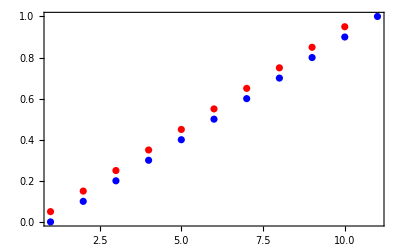

```mathematica
list=Table[i,{i,0,1,1/n}](*n+1コ*)
listM=Table[i,{i,1/n/2,1-1/n/2,1/n}](*nコ*)
opt={PlotRange->{{1,n+1},{0,1}},Frame->True};
Show[ListPlot[list,PlotStyle->Blue,opt],ListPlot[listM,PlotStyle->Red,opt]]
```

```mathematica
n=10;
Table[1/n/2+1/n*(i-1),{i,1,n,1}]

makelist[n_]:=Table[1/n/2+1/n*(i-1),{i,1,n,1}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

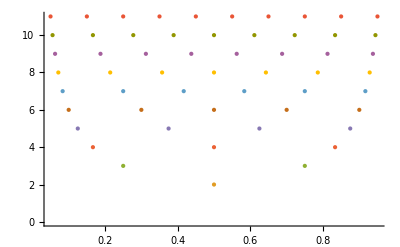

```mathematica
NumberLinePlot[Table[makelist[i],{i,0,10}]]
```

```mathematica
makelist[n]
```

{1/80,3/80,1/16,7/80,9/80,11/80,13/80,3/16,17/80,19/80,21/80,23/80,5/16,27/80,29/80,31/80,33/80,7/16,37/80,39/80,41/80,43/80,9/16,47/80,49/80,51/80,53/80,11/16,57/80,59/80,61/80,63/80,13/16,67/80,69/80,71/80,73/80,15/16,77/80,79/80}

```mathematica
n=10;
makelist[n]
Column@Table[{t0,t1},{t0,makelist[n]},{t1,makelist[n*t0(*t0は1/(2*n0)から始まるので，この時n1*t0=n1/2*n0*)]}]
Column@Table[{t0,t1},{t0,makelist[n]},{t1,makelist[n*t0(*t0は1/(2n)から始まるので，この時n*t0=1/2，そこで1/2を足して1とする*)+1/2]}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

{}
{{3/20,1/3}}
{{1/4,1/5},{1/4,3/5}}
{{7/20,1/7},{7/20,3/7},{7/20,5/7}}
{{9/20,1/9},{9/20,1/3},{9/20,5/9},{9/20,7/9}}
{{11/20,1/11},{11/20,3/11},{11/20,5/11},{11/20,7/11},{11/20,9/11}}
{{13/20,1/13},{13/20,3/13},{13/20,5/13},{13/20,7/13},{13/20,9/13},{13/20,11/13}}
{{3/4,1/15},{3/4,1/5},{3/4,1/3},{3/4,7/15},{3/4,3/5},{3/4,11/15},{3/4,13/15}}
{{17/20,1/17},{17/20,3/17},{17/20,5/17},{17/20,7/17},{17/20,9/17},{17/20,11/17},{17/20,13/17},{17/20,15/17}}
{{19/20,1/19},{19/20,3/19},{19/20,5/19},{19/20,7/19},{19/20,9/19},{19/20,11/19},{19/20,13/19},{19/20,15/19},{19/20,17/19}}

{{1/20,1/2}}
{{3/20,1/4},{3/20,3/4}}
{{1/4,1/6},{1/4,1/2},{1/4,5/6}}
{{7/20,1/8},{7/20,3/8},{7/20,5/8},{7/20,7/8}}
{{9/20,1/10},{9/20,3/10},{9/20,1/2},{9/20,7/10},{9/20,9/10}}
{{11/20,1/12},{11/20,1/4},{11/20,5/12},{11/20,7/12},{11/20,3/4},{11/20,11/12}}
{{13/20,1/14},{13/20,3/14},{13/20,5/14},{13/20,1/2},{13/20,9/14},{13/20,11/14},{13/20,13/14}}
{{3/4,1/16},{3/4,3/16},{3/4,5/16},{3/4,7/16},{3/4,9/16},{3/4,11/16},{3/4,13/16},{3/4,15/16}}
{{17/20,1/18},{17/20,1/6},{17/20,5/18},{17/20,7/18},{17/20,1/2},{17/20,11/18},{17/20,13/18},{17/20,5/6},{17/20,17/18}}
{{19/20,1/20},{19/20,3/20},{19/20,1/4},{19/20,7/20},{19/20,9/20},{19/20,11/20},{19/20,13/20},{19/20,3/4},{19/20,17/20},{19/20,19/20}}

```mathematica
n=20;
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[n]},{t1,makelist[n*t0+1/2]}],1]]
,PlotLabel->"makelist[n]とmakelist[n*t0+1/2]を使うと均等"
]
```

```mathematica
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[n]},{t1,makelist[n*t0+1/2]}],1]]
,PlotLabel->"makelist[n]とmakelist[n*t0+1/2]を使うと均等"
]
,{n,1,40,1}]
(*n0とn1を分けて調整したいが未だできていない*)
Manipulate[
Show[fig,
ListPointPlot3D[Flatten[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[n0]},{t1,makelist[1+Floor[n1*t0-n1/(2*n0)]]}],1]]
,PlotLabel->"makelist[n]とmakelist[n*t0+1/2]を使うと均等"
]
,{n1,1,40,1},{n0,1,40,1}]
```

Table::iterb: 反復演算{t0,makelist[1]}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,makelist[1.]}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[1]},{t1,makelist[FE`n$$17 t0+1/2]}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[1]},{t1,makelist[FE`n$$17 t0+1 Power[«2»]]}]],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

Table::iterb: 反復演算{t0,makelist[33]}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,makelist[33.]}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[33]},{t1,makelist[1+Floor[FE`n1$$19 t0-FE`n1$$19 Power[«2»]]]}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[33]},{t1,makelist[1+Floor[Plus[«2»]]]}]],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

Table::iterb: 反復演算{t0,makelist[1]}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,makelist[1.]}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[1]},{t1,makelist[FE`n$$20 t0+1/2]}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[1]},{t1,makelist[FE`n$$20 t0+1 Power[«2»]]}]],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

Table::iterb: 反復演算{t0,makelist[33]}は適正な範囲を持ちません．

Table::iterb: 反復演算{t0,makelist[33.]}は適正な範囲を持ちません．

General::stop: この計算中に，Table::iterbのこれ以上の出力は表示されません．

ListPointPlot3D::ldata: Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[33]},{t1,makelist[1+Floor[FE`n1$$21 t0-FE`n1$$21 Power[«2»]]]}]は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[Table[MyinterpQuadIDW12[ps,t0,t1],{t0,makelist[33]},{t1,makelist[1+Floor[Plus[«2»]]]}]],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

ListPointPlot3D::ldata: {MyinterpQuadIDW12[{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}},1/66,1/2],«49»,«607»}は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[{MyinterpQuadIDW12[{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}},1/66,1/2],«49»,«607»}],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

ListPointPlot3D::ldata: {MyinterpQuadIDW12[{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}},1/2,1/2]}は有効なデータ集合でもデータ集合のリストでもありません．

Show::gcomb: Show[fig,ListPointPlot3D[{MyinterpQuadIDW12[{{5.87785,6.88191,4.25325},{2.73267,9.61938,0.},{0.,8.50651,5.25731},{4.33889,8.62668,2.59892},{1.6246,9.51057,2.62866},{3.09017,8.09017,5.},{4.25325,5.87785,6.88191},{6.9378,7.02046,1.60622},{5.25731,8.50651,0.},{0.,10.,0.},{-1.6246,9.51057,2.62866},{1.60622,6.9378,7.02046}},1/2,1/2]}],PlotLabel→makelist[n]とmakelist[n*t0+1/2]を使うと均等]のグラフィックスオブジェクトを組み合せることができませんでした．

```mathematica
ϵ=1;
f[r_]:=(ϵ^2*r^2+1)^(1/2.);
cord={{1,1},
{-1,1},
{1,-1},
{0,1},
{0,0},
{1,0},
{2,0},
{0,2},
{-1,2},
{-1,0},
{0,-1},
{2,-1}};

mat=Table[Table[f[Norm[{#1,#2}-cord[[origin]]]&@@cord[[i]]],{i,1,12,1}],{origin,1,12,1}]

intp[ps_,t0_,t1IN_]:=Module[{t1},
t1=(1-t0)*t1IN;
wx=Dot[Inverse[mat],Transpose[ps][[1]]];
wy=Dot[Inverse[mat],Transpose[ps][[2]]];
wz=Dot[Inverse[mat],Transpose[ps][[3]]];
Return[
{Sum[wx[[i]]*f[Norm[cord[[i]]-{t0,t1}]],{i,1,12,1}],
Sum[wy[[i]]*f[Norm[cord[[i]]-{t0,t1}]],{i,1,12,1}],
Sum[wz[[i]]*f[Norm[cord[[i]]-{t0,t1}]],{i,1,12,1}]}]
];

Show[
ListPointPlot3D[ps],
ListPointPlot3D[Table[intp[ps,t0,t1],{t0,0,1,.1},{t1,0,1,.1}]]
]
```

{{1.,2.23607,2.23607,1.41421,1.73205,1.41421,1.73205,1.73205,2.44949,2.44949,2.44949,2.44949},{2.23607,1.,3.,1.41421,1.73205,2.44949,3.31662,1.73205,1.41421,1.41421,2.44949,3.74166},{2.23607,3.,1.,2.44949,1.73205,1.41421,1.73205,3.31662,3.74166,2.44949,1.41421,1.41421},{1.41421,1.41421,2.44949,1.,1.41421,1.73205,2.44949,1.41421,1.73205,1.73205,2.23607,3.},{1.73205,1.73205,1.73205,1.41421,1.,1.41421,2.23607,2.23607,2.44949,1.41421,1.41421,2.44949},{1.41421,2.44949,1.41421,1.73205,1.41421,1.,1.41421,2.44949,3.,2.23607,1.73205,1.73205},{1.73205,3.31662,1.73205,2.44949,2.23607,1.41421,1.,3.,3.74166,3.16228,2.44949,1.41421},{1.73205,1.73205,3.31662,1.41421,2.23607,2.44949,3.,1.,1.41421,2.44949,3.16228,3.74166},{2.44949,1.41421,3.74166,1.73205,2.44949,3.,3.74166,1.41421,1.,2.23607,3.31662,4.3589},{2.44949,1.41421,2.44949,1.73205,1.41421,2.23607,3.16228,2.44949,2.23607,1.,1.73205,3.31662},{2.44949,2.44949,1.41421,2.23607,1.41421,1.73205,2.44949,3.16228,3.31662,1.73205,1.,2.23607},{2.44949,3.74166,1.41421,3.,2.44949,1.73205,1.41421,3.74166,4.3589,3.31662,2.23607,1.}}

-Graphics3D-

### データ

```mathematica
tab ={{{5.877850,6.881910,4.253250},{2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{3.090170,8.090170,5.000000},{4.253250,5.877850,6.881910},{6.937800,7.020460,1.606220},{5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460}},{{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,4.253250},{-2.732670,9.619380,0.000000},{-6.937800,7.020460,1.606220},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,3.090170},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,-2.598920}},{{-8.626680,-2.598920,4.338890},{-5.257310,0.000000,8.506510},{-8.626680,2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-7.020460,1.606220,6.937800},{-8.506510,0.000000,5.257310},{-9.619380,0.000000,2.732670},{-6.881910,-4.253250,5.877850},{-5.000000,-3.090170,8.090170},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-9.619380,0.000000,2.732670}},{{-2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{2.628660,-1.624600,9.510570},{0.000000,-5.257310,8.506510},{2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{-2.628660,-1.624600,9.510570},{-1.606220,-6.937800,7.020460},{-1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000}},{{7.020460,1.606220,6.937800},{5.877850,6.881910,4.253250},{2.598920,4.338890,8.626680},{6.881910,4.253250,5.877850},{4.253250,5.877850,6.881910},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{8.626680,2.598920,4.338890},{8.090170,5.000000,3.090170},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{2.628660,1.624600,9.510570}},{{8.626680,-2.598920,4.338890},{9.510570,2.628660,1.624600},{7.020460,1.606220,6.937800},{9.619380,0.000000,2.732670},{8.626680,2.598920,4.338890},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{9.510570,-2.628660,1.624600},{10.000000,0.000000,0.000000},{8.090170,5.000000,3.090170},{6.881910,4.253250,5.877850},{7.020460,-1.606220,6.937800}},{{7.020460,-1.606220,6.937800},{9.510570,-2.628660,1.624600},{8.626680,2.598920,4.338890},{8.626680,-2.598920,4.338890},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{7.020460,1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.090170,-5.000000,3.090170},{10.000000,0.000000,0.000000},{9.510570,2.628660,1.624600},{7.020460,1.606220,6.937800}},{{2.598920,-4.338890,8.626680},{5.877850,-6.881910,4.253250},{7.020460,-1.606220,6.937800},{4.253250,-5.877850,6.881910},{6.881910,-4.253250,5.877850},{5.000000,-3.090170,8.090170},{2.628660,-1.624600,9.510570},{1.606220,-6.937800,7.020460},{3.090170,-8.090170,5.000000},{8.090170,-5.000000,3.090170},{8.626680,-2.598920,4.338890},{5.257310,0.000000,8.506510}},{{-2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{2.598920,-4.338890,8.626680},{-1.606220,-6.937800,7.020460},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{0.000000,-2.732670,9.619380},{-4.253250,-5.877850,6.881910},{-3.090170,-8.090170,5.000000},{3.090170,-8.090170,5.000000},{4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380}},{{-6.937800,-7.020460,-1.606220},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,2.598920},{-4.338890,-8.626680,-2.598920},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,-4.253250},{-3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-6.937800,-7.020460,1.606220}},{{7.020460,-1.606220,-6.937800},{5.877850,-6.881910,-4.253250},{2.598920,-4.338890,-8.626680},{6.881910,-4.253250,-5.877850},{4.253250,-5.877850,-6.881910},{5.000000,-3.090170,-8.090170},{5.257310,0.000000,-8.506510},{8.626680,-2.598920,-4.338890},{8.090170,-5.000000,-3.090170},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{2.628660,-1.624600,-9.510570}},{{-2.598920,-4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{1.606220,-6.937800,-7.020460},{0.000000,-2.732670,-9.619380},{2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{-1.606220,-6.937800,-7.020460},{-2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{5.000000,-3.090170,-8.090170},{4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460}},{{-1.606220,-6.937800,-7.020460},{-2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{-2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{0.000000,-5.257310,-8.506510},{1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{2.628660,-1.624600,-9.510570},{1.606220,-6.937800,-7.020460}},{{-9.619380,0.000000,-2.732670},{-6.881910,4.253250,-5.877850},{-7.020460,-1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.510570,2.628660,-1.624600},{-8.090170,5.000000,-3.090170},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-8.626680,-2.598920,-4.338890}},{{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{1.624600,9.510570,-2.628660},{5.257310,8.506510,0.000000},{4.338890,8.626680,-2.598920},{2.732670,9.619380,0.000000},{1.624600,9.510570,2.628660},{6.937800,7.020460,1.606220},{6.937800,7.020460,1.606220},{5.877850,6.881910,-4.253250},{3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000}},{{8.626680,2.598920,-4.338890},{4.253250,5.877850,-6.881910},{6.937800,7.020460,-1.606220},{6.881910,4.253250,-5.877850},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{3.090170,8.090170,-5.000000},{4.338890,8.626680,-2.598920},{8.506510,5.257310,0.000000}},{{-9.619380,0.000000,2.732670},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,1.624600},{-9.510570,2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,1.624600},{-8.626680,2.598920,4.338890},{-8.090170,5.000000,3.090170},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-9.510570,-2.628660,-1.624600}},{{-8.626680,2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-9.510570,-2.628660,-1.624600},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-7.020460,1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.090170,-5.000000,-3.090170},{-10.000000,0.000000,0.000000}},{{-1.606220,-6.937800,7.020460},{-6.881910,-4.253250,5.877850},{-4.338890,-8.626680,2.598920},{-4.253250,-5.877850,6.881910},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-8.090170,-5.000000,3.090170},{-6.937800,-7.020460,1.606220},{-1.624600,-9.510570,2.628660}},{{-4.338890,-8.626680,-2.598920},{-6.881910,-4.253250,-5.877850},{-1.606220,-6.937800,-7.020460},{-5.877850,-6.881910,-4.253250},{-4.253250,-5.877850,-6.881910},{-3.090170,-8.090170,-5.000000},{-1.624600,-9.510570,-2.628660},{-6.937800,-7.020460,-1.606220},{-8.090170,-5.000000,-3.090170},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310}},{{-4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-1.624600,9.510570,2.628660},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-3.090170,8.090170,5.000000},{-5.877850,6.881910,4.253250},{-2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{3.090170,8.090170,5.000000},{1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920}},{{-9.510570,2.628660,1.624600},{-7.020460,1.606220,6.937800},{-5.877850,6.881910,4.253250},{-8.626680,2.598920,4.338890},{-6.881910,4.253250,5.877850},{-8.090170,5.000000,3.090170},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,2.732670},{-8.506510,0.000000,5.257310},{-5.000000,3.090170,8.090170},{-4.253250,5.877850,6.881910},{-6.937800,7.020460,1.606220}},{{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{-2.732670,9.619380,0.000000},{-1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{-3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{2.732670,9.619380,0.000000}},{{-5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{-3.090170,8.090170,-5.000000},{-2.732670,9.619380,0.000000},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,-1.606220},{-4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660},{1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-5.877850,6.881910,-4.253250}},{{-6.937800,7.020460,1.606220},{-8.626680,2.598920,4.338890},{-4.253250,5.877850,6.881910},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-5.877850,6.881910,4.253250},{-4.338890,8.626680,2.598920},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,1.624600},{-7.020460,1.606220,6.937800},{-5.000000,3.090170,8.090170},{-3.090170,8.090170,5.000000}},{{-8.626680,-2.598920,-4.338890},{-9.510570,2.628660,-1.624600},{-7.020460,1.606220,-6.937800},{-9.619380,0.000000,-2.732670},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-7.020460,-1.606220,-6.937800},{-9.510570,-2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,-3.090170},{-6.881910,4.253250,-5.877850},{-7.020460,-1.606220,-6.937800}},{{-8.506510,5.257310,0.000000},{-4.338890,8.626680,-2.598920},{-6.881910,4.253250,-5.877850},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-6.937800,7.020460,1.606220},{-5.257310,8.506510,0.000000},{-3.090170,8.090170,-5.000000},{-4.253250,5.877850,-6.881910},{-8.626680,2.598920,-4.338890}},{{-5.257310,8.506510,0.000000},{-8.090170,5.000000,-3.090170},{-8.090170,5.000000,3.090170},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-4.338890,8.626680,2.598920},{-4.338890,8.626680,-2.598920},{-5.877850,6.881910,-4.253250},{-9.510570,2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-5.877850,6.881910,4.253250}},{{-3.090170,8.090170,-5.000000},{-5.000000,3.090170,-8.090170},{-8.090170,5.000000,-3.090170},{-4.253250,5.877850,-6.881910},{-6.881910,4.253250,-5.877850},{-5.877850,6.881910,-4.253250},{-4.338890,8.626680,-2.598920},{-1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-7.020460,1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-6.937800,7.020460,-1.606220}},{{-3.090170,8.090170,-5.000000},{3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510},{0.000000,8.506510,-5.257310},{1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-1.624600,9.510570,-2.628660},{1.624600,9.510570,-2.628660},{4.253250,5.877850,-6.881910},{2.598920,4.338890,-8.626680},{-2.598920,4.338890,-8.626680}},{{0.000000,8.506510,5.257310},{2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000},{1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{-3.090170,8.090170,5.000000},{3.090170,8.090170,5.000000},{4.338890,8.626680,2.598920},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,2.598920}},{{9.619380,0.000000,2.732670},{6.881910,4.253250,5.877850},{7.020460,-1.606220,6.937800},{8.626680,2.598920,4.338890},{7.020460,1.606220,6.937800},{8.506510,0.000000,5.257310},{8.626680,-2.598920,4.338890},{9.510570,2.628660,1.624600},{8.090170,5.000000,3.090170},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{8.626680,-2.598920,4.338890}},{{3.090170,8.090170,5.000000},{8.090170,5.000000,3.090170},{5.257310,8.506510,0.000000},{5.877850,6.881910,4.253250},{6.937800,7.020460,1.606220},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{4.253250,5.877850,6.881910},{6.881910,4.253250,5.877850},{8.506510,5.257310,0.000000},{6.937800,7.020460,-1.606220},{2.732670,9.619380,0.000000}},{{9.510570,-2.628660,-1.624600},{8.626680,2.598920,-4.338890},{9.510570,2.628660,1.624600},{9.619380,0.000000,-2.732670},{9.510570,2.628660,-1.624600},{10.000000,0.000000,0.000000},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{8.090170,5.000000,-3.090170},{8.506510,5.257310,0.000000},{9.619380,0.000000,2.732670}},{{8.090170,5.000000,3.090170},{8.090170,5.000000,-3.090170},{5.257310,8.506510,0.000000},{8.506510,5.257310,0.000000},{6.937800,7.020460,-1.606220},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{9.510570,2.628660,1.624600},{9.510570,2.628660,-1.624600},{5.877850,6.881910,-4.253250},{4.338890,8.626680,-2.598920},{4.338890,8.626680,2.598920}},{{5.257310,8.506510,0.000000},{8.090170,5.000000,-3.090170},{3.090170,8.090170,-5.000000},{6.937800,7.020460,-1.606220},{5.877850,6.881910,-4.253250},{4.338890,8.626680,-2.598920},{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{8.506510,5.257310,0.000000},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{1.624600,9.510570,-2.628660}},{{0.000000,10.000000,0.000000},{3.090170,8.090170,-5.000000},{-3.090170,8.090170,-5.000000},{1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{2.732670,9.619380,0.000000},{4.338890,8.626680,-2.598920},{1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{-4.338890,8.626680,-2.598920}},{{0.000000,5.257310,-8.506510},{3.090170,8.090170,-5.000000},{5.000000,3.090170,-8.090170},{1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{-1.606220,6.937800,-7.020460},{0.000000,8.506510,-5.257310},{5.877850,6.881910,-4.253250},{6.881910,4.253250,-5.877850},{2.628660,1.624600,-9.510570}},{{-5.877850,-6.881910,4.253250},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-4.253250,-5.877850,6.881910},{-6.937800,-7.020460,1.606220},{-5.257310,-8.506510,0.000000},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,2.628660},{-1.606220,-6.937800,7.020460}},{{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,5.000000},{-8.090170,-5.000000,3.090170},{-4.338890,-8.626680,2.598920},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,1.606220},{-6.937800,-7.020460,-1.606220},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,2.628660},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-8.506510,-5.257310,0.000000}},{{0.000000,-10.000000,0.000000},{3.090170,-8.090170,5.000000},{-3.090170,-8.090170,5.000000},{1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-1.624600,-9.510570,2.628660},{-2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{4.338890,-8.626680,2.598920},{1.606220,-6.937800,7.020460},{-1.606220,-6.937800,7.020460},{-4.338890,-8.626680,2.598920}},{{-4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{-1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460},{0.000000,-8.506510,-5.257310},{-3.090170,-8.090170,-5.000000},{-5.877850,-6.881910,-4.253250},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{3.090170,-8.090170,-5.000000},{1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920}},{{-4.338890,-8.626680,-2.598920},{-1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-1.624600,-9.510570,-2.628660},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,-4.253250},{-4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000}},{{0.000000,-5.257310,-8.506510},{-3.090170,-8.090170,-5.000000},{-5.000000,-3.090170,-8.090170},{-1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{1.606220,-6.937800,-7.020460},{0.000000,-8.506510,-5.257310},{-5.877850,-6.881910,-4.253250},{-6.881910,-4.253250,-5.877850},{-2.628660,-1.624600,-9.510570}},{{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,1.606220},{-9.510570,-2.628660,-1.624600},{-6.937800,-7.020460,-1.606220},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-4.338890,-8.626680,-2.598920},{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,-4.338890}},{{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,-3.090170},{-3.090170,-8.090170,-5.000000},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-2.732670,-9.619380,0.000000},{-6.937800,-7.020460,1.606220},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,-5.877850},{-4.253250,-5.877850,-6.881910},{-1.624600,-9.510570,-2.628660}},{{-8.090170,-5.000000,3.090170},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,-3.090170},{-9.510570,-2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,1.606220},{-8.626680,-2.598920,4.338890},{-9.619380,0.000000,2.732670},{-9.619380,0.000000,-2.732670},{-8.626680,-2.598920,-4.338890},{-6.937800,-7.020460,-1.606220}},{{-8.506510,0.000000,5.257310},{-8.090170,-5.000000,3.090170},{-5.000000,-3.090170,8.090170},{-8.626680,-2.598920,4.338890},{-6.881910,-4.253250,5.877850},{-7.020460,-1.606220,6.937800},{-7.020460,1.606220,6.937800},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,1.624600},{-5.877850,-6.881910,4.253250},{-4.253250,-5.877850,6.881910},{-5.257310,0.000000,8.506510}},{{5.877850,-6.881910,4.253250},{6.937800,-7.020460,-1.606220},{9.510570,-2.628660,1.624600},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{6.881910,-4.253250,5.877850},{4.338890,-8.626680,2.598920},{5.257310,-8.506510,0.000000},{8.090170,-5.000000,-3.090170},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,4.338890}},{{-1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{3.090170,-8.090170,5.000000},{5.000000,-3.090170,8.090170},{2.628660,-1.624600,9.510570},{-2.598920,-4.338890,8.626680}},{{8.090170,-5.000000,-3.090170},{10.000000,0.000000,0.000000},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,-1.624600},{9.510570,-2.628660,1.624600},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,-1.606220},{8.626680,-2.598920,-4.338890},{9.619380,0.000000,-2.732670},{9.619380,0.000000,2.732670},{8.626680,-2.598920,4.338890},{6.937800,-7.020460,1.606220}},{{0.000000,-2.732670,-9.619380},{4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{-2.598920,-4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{5.000000,-3.090170,-8.090170},{3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-2.598920,-4.338890,-8.626680}},{{8.090170,-5.000000,3.090170},{3.090170,-8.090170,5.000000},{5.257310,-8.506510,0.000000},{5.877850,-6.881910,4.253250},{4.338890,-8.626680,2.598920},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{1.624600,-9.510570,2.628660},{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220}},{{0.000000,-8.506510,5.257310},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,4.253250},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{0.000000,-10.000000,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,1.606220},{4.253250,-5.877850,6.881910}},{{0.000000,-10.000000,0.000000},{3.090170,-8.090170,-5.000000},{5.257310,-8.506510,0.000000},{1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,2.628660},{-1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{4.338890,-8.626680,2.598920}},{{5.257310,-8.506510,0.000000},{3.090170,-8.090170,-5.000000},{8.090170,-5.000000,-3.090170},{4.338890,-8.626680,-2.598920},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{6.937800,-7.020460,1.606220},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,-2.628660},{4.253250,-5.877850,-6.881910},{6.881910,-4.253250,-5.877850},{8.506510,-5.257310,0.000000}},{{-3.090170,8.090170,5.000000},{-5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{-4.253250,5.877850,6.881910},{-2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-5.877850,6.881910,4.253250},{-6.881910,4.253250,5.877850},{-2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{1.606220,6.937800,7.020460}},{{-4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{-5.257310,0.000000,8.506510},{-2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-5.000000,-3.090170,8.090170},{-6.881910,-4.253250,5.877850},{-1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-7.020460,-1.606220,6.937800}},{{-5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,5.257310,8.506510},{-2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-5.257310,0.000000,8.506510},{-2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460}},{{6.881910,-4.253250,5.877850},{7.020460,1.606220,6.937800},{2.628660,-1.624600,9.510570},{7.020460,-1.606220,6.937800},{5.257310,0.000000,8.506510},{5.000000,-3.090170,8.090170},{4.253250,-5.877850,6.881910},{8.626680,-2.598920,4.338890},{8.506510,0.000000,5.257310},{5.000000,3.090170,8.090170},{2.628660,1.624600,9.510570},{2.598920,-4.338890,8.626680}},{{0.000000,0.000000,10.000000},{5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,2.732670,9.619380},{-2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{5.257310,0.000000,8.506510},{4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-2.598920,4.338890,8.626680}},{{0.000000,5.257310,8.506510},{5.000000,3.090170,8.090170},{3.090170,8.090170,5.000000},{2.598920,4.338890,8.626680},{4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{-1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{2.628660,1.624600,9.510570},{6.881910,4.253250,5.877850},{5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310}},{{-2.598920,-4.338890,8.626680},{-2.628660,1.624600,9.510570},{-7.020460,-1.606220,6.937800},{-2.628660,-1.624600,9.510570},{-5.257310,0.000000,8.506510},{-5.000000,-3.090170,8.090170},{-4.253250,-5.877850,6.881910},{0.000000,-2.732670,9.619380},{0.000000,0.000000,10.000000},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-6.881910,-4.253250,5.877850}},{{0.000000,-5.257310,8.506510},{-5.000000,-3.090170,8.090170},{-3.090170,-8.090170,5.000000},{-2.598920,-4.338890,8.626680},{-4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-2.628660,-1.624600,9.510570},{-6.881910,-4.253250,5.877850},{-5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310}},{{7.020460,-1.606220,6.937800},{2.628660,1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.257310,0.000000,8.506510},{2.628660,-1.624600,9.510570},{5.000000,-3.090170,8.090170},{6.881910,-4.253250,5.877850},{7.020460,1.606220,6.937800},{5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,-2.732670,9.619380},{4.253250,-5.877850,6.881910}},{{8.506510,0.000000,5.257310},{5.000000,-3.090170,8.090170},{8.090170,-5.000000,3.090170},{7.020460,-1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.626680,-2.598920,4.338890},{9.619380,0.000000,2.732670},{7.020460,1.606220,6.937800},{5.257310,0.000000,8.506510},{4.253250,-5.877850,6.881910},{5.877850,-6.881910,4.253250},{9.510570,-2.628660,1.624600}},{{-2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{2.628660,-1.624600,-9.510570},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-2.628660,-1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{5.000000,3.090170,-8.090170},{5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380}},{{-6.881910,-4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-2.628660,-1.624600,-9.510570},{-7.020460,-1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{-5.000000,-3.090170,-8.090170},{-4.253250,-5.877850,-6.881910},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-5.000000,3.090170,-8.090170},{-2.628660,1.624600,-9.510570},{-2.598920,-4.338890,-8.626680}},{{5.000000,3.090170,-8.090170},{5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{5.257310,0.000000,-8.506510},{2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{7.020460,1.606220,-6.937800},{7.020460,-1.606220,-6.937800},{2.598920,-4.338890,-8.626680},{0.000000,-2.732670,-9.619380},{0.000000,2.732670,-9.619380}},{{8.506510,0.000000,-5.257310},{5.000000,3.090170,-8.090170},{8.090170,5.000000,-3.090170},{7.020460,1.606220,-6.937800},{6.881910,4.253250,-5.877850},{8.626680,2.598920,-4.338890},{9.619380,0.000000,-2.732670},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{4.253250,5.877850,-6.881910},{5.877850,6.881910,-4.253250},{9.510570,2.628660,-1.624600}},{{0.000000,0.000000,-10.000000},{-5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{-2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{-5.257310,0.000000,-8.506510},{-4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680}},{{-6.881910,4.253250,-5.877850},{-1.606220,6.937800,-7.020460},{-2.628660,1.624600,-9.510570},{-4.253250,5.877850,-6.881910},{-2.598920,4.338890,-8.626680},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-5.877850,6.881910,-4.253250},{-3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{-5.257310,0.000000,-8.506510}},{{8.090170,-5.000000,-3.090170},{5.000000,-3.090170,-8.090170},{8.506510,0.000000,-5.257310},{6.881910,-4.253250,-5.877850},{7.020460,-1.606220,-6.937800},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{5.877850,-6.881910,-4.253250},{4.253250,-5.877850,-6.881910},{5.257310,0.000000,-8.506510},{7.020460,1.606220,-6.937800},{9.619380,0.000000,-2.732670}},{{2.628660,-1.624600,-9.510570},{7.020460,1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{5.257310,0.000000,-8.506510},{7.020460,-1.606220,-6.937800},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{2.628660,1.624600,-9.510570},{5.000000,3.090170,-8.090170},{8.506510,0.000000,-5.257310},{8.626680,-2.598920,-4.338890},{4.253250,-5.877850,-6.881910}},{{-7.020460,-1.606220,-6.937800},{-2.628660,1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.257310,0.000000,-8.506510},{-2.628660,-1.624600,-9.510570},{-5.000000,-3.090170,-8.090170},{-6.881910,-4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{-4.253250,-5.877850,-6.881910}},{{-8.506510,0.000000,-5.257310},{-5.000000,-3.090170,-8.090170},{-8.090170,-5.000000,-3.090170},{-7.020460,-1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.626680,-2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-7.020460,1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{-4.253250,-5.877850,-6.881910},{-5.877850,-6.881910,-4.253250},{-9.510570,-2.628660,-1.624600}},{{9.619380,0.000000,-2.732670},{8.506510,5.257310,0.000000},{9.619380,0.000000,2.732670},{9.510570,2.628660,-1.624600},{9.510570,2.628660,1.624600},{10.000000,0.000000,0.000000},{9.510570,-2.628660,-1.624600},{8.626680,2.598920,-4.338890},{8.090170,5.000000,-3.090170},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{9.510570,-2.628660,1.624600}},{{9.510570,-2.628660,1.624600},{8.626680,-2.598920,-4.338890},{9.510570,2.628660,-1.624600},{9.510570,-2.628660,-1.624600},{9.619380,0.000000,-2.732670},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,-3.090170},{8.506510,0.000000,-5.257310},{8.626680,2.598920,-4.338890},{9.510570,2.628660,1.624600}},{{-8.090170,5.000000,3.090170},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,5.257310},{-9.510570,2.628660,1.624600},{-9.619380,0.000000,2.732670},{-8.626680,2.598920,4.338890},{-6.881910,4.253250,5.877850},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,-1.624600},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-7.020460,1.606220,6.937800}},{{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,4.338890},{-9.510570,2.628660,1.624600},{-9.510570,-2.628660,1.624600},{-9.619380,0.000000,2.732670},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,-2.732670},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,3.090170},{-8.506510,0.000000,5.257310},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,-1.624600}},{{-3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-5.257310,8.506510,0.000000},{-1.624600,9.510570,2.628660},{-2.732670,9.619380,0.000000},{-4.338890,8.626680,2.598920},{-5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{1.624600,9.510570,2.628660},{-1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,1.606220}},{{-6.881910,4.253250,5.877850},{-4.338890,8.626680,2.598920},{-8.506510,5.257310,0.000000},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-8.090170,5.000000,3.090170},{-8.626680,2.598920,4.338890},{-4.253250,5.877850,6.881910},{-3.090170,8.090170,5.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-9.510570,2.628660,1.624600}},{{-5.257310,8.506510,0.000000},{-8.090170,5.000000,3.090170},{-3.090170,8.090170,5.000000},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,4.253250},{-4.338890,8.626680,2.598920},{-2.732670,9.619380,0.000000},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,5.877850},{-4.253250,5.877850,6.881910},{-1.624600,9.510570,2.628660}},{{-5.877850,6.881910,4.253250},{-6.937800,7.020460,-1.606220},{-9.510570,2.628660,1.624600},{-6.937800,7.020460,1.606220},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,4.338890}},{{-6.937800,7.020460,-1.606220},{-1.624600,9.510570,-2.628660},{-4.253250,5.877850,-6.881910},{-4.338890,8.626680,-2.598920},{-3.090170,8.090170,-5.000000},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-5.257310,8.506510,0.000000},{-2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-1.606220,6.937800,-7.020460},{-6.881910,4.253250,-5.877850}},{{1.624600,9.510570,-2.628660},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,2.628660},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{0.000000,10.000000,0.000000},{2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-3.090170,8.090170,-5.000000},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660}},{{-6.937800,7.020460,1.606220},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,-2.598920},{-4.338890,8.626680,2.598920},{-2.732670,9.619380,0.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,4.253250},{-3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-1.624600,9.510570,-2.628660},{-6.937800,7.020460,-1.606220}},{{-4.338890,8.626680,2.598920},{-1.624600,9.510570,-2.628660},{-6.937800,7.020460,-1.606220},{-2.732670,9.619380,0.000000},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,1.606220},{-1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-3.090170,8.090170,-5.000000},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,1.606220}},{{-6.937800,7.020460,1.606220},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,-4.253250},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-6.937800,7.020460,-1.606220},{-8.506510,5.257310,0.000000},{-4.338890,8.626680,2.598920},{-4.338890,8.626680,2.598920},{-1.624600,9.510570,-2.628660},{-3.090170,8.090170,-5.000000},{-8.090170,5.000000,-3.090170}},{{-4.338890,8.626680,2.598920},{-4.338890,8.626680,-2.598920},{-8.506510,5.257310,0.000000},{-5.257310,8.506510,0.000000},{-6.937800,7.020460,-1.606220},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,4.253250},{-2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,-4.253250},{-8.090170,5.000000,-3.090170},{-8.090170,5.000000,3.090170}},{{1.624600,9.510570,-2.628660},{-1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{0.000000,10.000000,0.000000},{1.624600,9.510570,2.628660},{2.732670,9.619380,0.000000},{4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{-2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310},{3.090170,8.090170,5.000000},{5.257310,8.506510,0.000000}},{{0.000000,8.506510,-5.257310},{2.732670,9.619380,0.000000},{5.877850,6.881910,-4.253250},{1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920},{3.090170,8.090170,-5.000000},{1.606220,6.937800,-7.020460},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{4.253250,5.877850,-6.881910}},{{5.257310,8.506510,0.000000},{3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000},{4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{2.732670,9.619380,0.000000},{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310},{-1.624600,9.510570,-2.628660},{1.624600,9.510570,2.628660}},{{6.881910,4.253250,-5.877850},{4.338890,8.626680,-2.598920},{8.506510,5.257310,0.000000},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{4.253250,5.877850,-6.881910},{3.090170,8.090170,-5.000000},{5.257310,8.506510,0.000000},{6.937800,7.020460,1.606220},{9.510570,2.628660,-1.624600}},{{4.338890,8.626680,-2.598920},{1.624600,9.510570,2.628660},{6.937800,7.020460,1.606220},{2.732670,9.619380,0.000000},{4.338890,8.626680,2.598920},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{3.090170,8.090170,5.000000},{5.877850,6.881910,4.253250},{6.937800,7.020460,-1.606220}},{{8.506510,5.257310,0.000000},{4.338890,8.626680,2.598920},{6.881910,4.253250,5.877850},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{8.090170,5.000000,3.090170},{9.510570,2.628660,1.624600},{6.937800,7.020460,-1.606220},{5.257310,8.506510,0.000000},{3.090170,8.090170,5.000000},{4.253250,5.877850,6.881910},{8.626680,2.598920,4.338890}},{{5.877850,6.881910,4.253250},{6.937800,7.020460,-1.606220},{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{5.257310,8.506510,0.000000},{4.338890,8.626680,2.598920},{3.090170,8.090170,5.000000},{8.090170,5.000000,3.090170},{8.506510,5.257310,0.000000},{4.338890,8.626680,-2.598920},{4.338890,8.626680,-2.598920},{1.624600,9.510570,2.628660}},{{5.877850,6.881910,-4.253250},{6.937800,7.020460,1.606220},{9.510570,2.628660,-1.624600},{6.937800,7.020460,-1.606220},{8.506510,5.257310,0.000000},{8.090170,5.000000,-3.090170},{6.881910,4.253250,-5.877850},{4.338890,8.626680,-2.598920},{5.257310,8.506510,0.000000},{8.090170,5.000000,3.090170},{9.510570,2.628660,1.624600},{8.626680,2.598920,-4.338890}},{{8.506510,5.257310,0.000000},{4.338890,8.626680,-2.598920},{4.338890,8.626680,2.598920},{6.937800,7.020460,-1.606220},{5.257310,8.506510,0.000000},{6.937800,7.020460,1.606220},{8.090170,5.000000,3.090170},{8.090170,5.000000,-3.090170},{5.877850,6.881910,-4.253250},{2.732670,9.619380,0.000000},{2.732670,9.619380,0.000000},{5.877850,6.881910,4.253250}},{{2.732670,9.619380,0.000000},{6.937800,7.020460,1.606220},{5.877850,6.881910,-4.253250},{5.257310,8.506510,0.000000},{6.937800,7.020460,-1.606220},{4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{4.338890,8.626680,2.598920},{4.338890,8.626680,2.598920},{8.506510,5.257310,0.000000},{8.090170,5.000000,-3.090170},{3.090170,8.090170,-5.000000}},{{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{-2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310}},{{0.000000,-8.506510,-5.257310},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,-4.253250},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920},{-3.090170,-8.090170,-5.000000},{-1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,-1.606220},{-4.253250,-5.877850,-6.881910}},{{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-2.732670,-9.619380,0.000000},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,2.628660}},{{-1.624600,-9.510570,-2.628660},{-6.937800,-7.020460,-1.606220},{-4.253250,-5.877850,-6.881910},{-4.338890,-8.626680,-2.598920},{-5.877850,-6.881910,-4.253250},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-1.606220,-6.937800,-7.020460}},{{-9.510570,-2.628660,1.624600},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,4.253250},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,-3.090170},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,2.598920},{-6.881910,-4.253250,5.877850}},{{-4.253250,-5.877850,6.881910},{-6.937800,-7.020460,1.606220},{-1.624600,-9.510570,2.628660},{-5.877850,-6.881910,4.253250},{-4.338890,-8.626680,2.598920},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-6.881910,-4.253250,5.877850},{-8.090170,-5.000000,3.090170},{-5.257310,-8.506510,0.000000},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310}},{{-6.937800,-7.020460,1.606220},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,2.628660},{-5.257310,-8.506510,0.000000},{-2.732670,-9.619380,0.000000},{-4.338890,-8.626680,2.598920},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,-1.606220},{-6.937800,-7.020460,-1.606220},{-1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,5.000000}},{{-6.937800,-7.020460,-1.606220},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,4.253250},{-5.257310,-8.506510,0.000000},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,1.606220},{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,2.628660},{-3.090170,-8.090170,5.000000},{-8.090170,-5.000000,3.090170}},{{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,2.598920},{-6.937800,-7.020460,-1.606220},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-8.090170,-5.000000,-3.090170},{-5.877850,-6.881910,-4.253250},{-2.732670,-9.619380,0.000000},{-2.732670,-9.619380,0.000000},{-5.877850,-6.881910,4.253250}},{{-2.732670,-9.619380,0.000000},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,-4.253250},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,-1.606220},{-4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,2.598920},{-4.338890,-8.626680,2.598920},{-8.506510,-5.257310,0.000000},{-8.090170,-5.000000,-3.090170},{-3.090170,-8.090170,-5.000000}},{{6.937800,-7.020460,1.606220},{5.877850,-6.881910,-4.253250},{9.510570,-2.628660,-1.624600},{6.937800,-7.020460,-1.606220},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,-2.598920},{6.881910,-4.253250,-5.877850},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,1.624600}},{{6.881910,-4.253250,-5.877850},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,-2.598920},{8.090170,-5.000000,-3.090170},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{4.253250,-5.877850,-6.881910},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{6.937800,-7.020460,1.606220},{5.257310,-8.506510,0.000000},{3.090170,-8.090170,-5.000000}},{{5.257310,-8.506510,0.000000},{3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{2.732670,-9.619380,0.000000},{4.338890,-8.626680,-2.598920},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660}},{{5.877850,-6.881910,-4.253250},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{3.090170,-8.090170,-5.000000},{4.253250,-5.877850,-6.881910},{6.937800,-7.020460,-1.606220},{5.257310,-8.506510,0.000000},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,-2.628660},{1.606220,-6.937800,-7.020460}},{{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920},{8.506510,-5.257310,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,4.253250},{2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,-4.253250},{8.090170,-5.000000,-3.090170},{8.090170,-5.000000,3.090170}},{{1.624600,-9.510570,2.628660},{6.937800,-7.020460,1.606220},{4.253250,-5.877850,6.881910},{4.338890,-8.626680,2.598920},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{8.090170,-5.000000,3.090170},{6.881910,-4.253250,5.877850},{1.606220,-6.937800,7.020460}},{{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,4.253250},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,1.606220},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,-2.598920},{4.338890,-8.626680,-2.598920},{8.506510,-5.257310,0.000000},{8.090170,-5.000000,3.090170},{3.090170,-8.090170,5.000000}},{{6.937800,-7.020460,1.606220},{1.624600,-9.510570,2.628660},{4.338890,-8.626680,-2.598920},{4.338890,-8.626680,2.598920},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,-2.628660},{6.937800,-7.020460,-1.606220}},{{1.624600,-9.510570,-2.628660},{6.937800,-7.020460,-1.606220},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920},{5.257310,-8.506510,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{3.090170,-8.090170,-5.000000},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,1.606220},{6.937800,-7.020460,1.606220},{1.624600,-9.510570,2.628660}},{{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,1.606220},{2.732670,-9.619380,0.000000},{6.937800,-7.020460,-1.606220},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,2.598920},{1.624600,-9.510570,-2.628660}},{{-1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910},{1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{-3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{2.598920,4.338890,8.626680},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660}},{{2.598920,4.338890,8.626680},{5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{4.253250,5.877850,6.881910},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{5.000000,3.090170,8.090170},{6.881910,4.253250,5.877850},{4.338890,8.626680,2.598920},{1.624600,9.510570,2.628660},{-1.606220,6.937800,7.020460}},{{-2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310},{0.000000,5.257310,8.506510},{1.606220,6.937800,7.020460},{-1.606220,6.937800,7.020460},{-4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{0.000000,2.732670,9.619380},{4.253250,5.877850,6.881910},{3.090170,8.090170,5.000000},{-3.090170,8.090170,5.000000}},{{-2.628660,1.624600,9.510570},{-1.606220,6.937800,7.020460},{-6.881910,4.253250,5.877850},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-5.000000,3.090170,8.090170},{-5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{0.000000,5.257310,8.506510},{-3.090170,8.090170,5.000000},{-5.877850,6.881910,4.253250},{-7.020460,1.606220,6.937800}},{{-4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{1.606220,6.937800,7.020460},{-2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-5.000000,3.090170,8.090170},{-2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310}},{{2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-2.628660,-1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{2.628660,-1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-5.000000,3.090170,8.090170},{-5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380}},{{-2.628660,1.624600,9.510570},{2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{0.000000,5.257310,8.506510},{-2.598920,4.338890,8.626680},{-5.000000,3.090170,8.090170},{0.000000,0.000000,10.000000},{2.628660,1.624600,9.510570},{1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{-4.253250,5.877850,6.881910}},{{4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380},{5.257310,0.000000,8.506510},{2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{5.000000,3.090170,8.090170},{6.881910,4.253250,5.877850},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{0.000000,0.000000,10.000000},{2.628660,-1.624600,9.510570},{7.020460,1.606220,6.937800}},{{-2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{1.606220,6.937800,7.020460},{0.000000,2.732670,9.619380},{2.598920,4.338890,8.626680},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{5.000000,3.090170,8.090170},{4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460}},{{0.000000,2.732670,9.619380},{4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{2.598920,4.338890,8.626680},{1.606220,6.937800,7.020460},{0.000000,5.257310,8.506510},{-2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{5.000000,3.090170,8.090170},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{-2.598920,4.338890,8.626680}},{{0.000000,0.000000,10.000000},{-5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510},{-2.628660,-1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-5.257310,0.000000,8.506510},{-4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680}},{{5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380},{4.253250,-5.877850,6.881910},{2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.000000,-3.090170,8.090170},{7.020460,-1.606220,6.937800},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{0.000000,-5.257310,8.506510},{1.606220,-6.937800,7.020460},{6.881910,-4.253250,5.877850}},{{0.000000,-5.257310,8.506510},{5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{2.598920,-4.338890,8.626680},{2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{-2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{5.257310,0.000000,8.506510},{2.628660,1.624600,9.510570},{-2.628660,-1.624600,9.510570}},{{1.606220,-6.937800,7.020460},{6.881910,-4.253250,5.877850},{2.628660,-1.624600,9.510570},{4.253250,-5.877850,6.881910},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{3.090170,-8.090170,5.000000},{5.877850,-6.881910,4.253250},{7.020460,-1.606220,6.937800},{5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380}},{{0.000000,-5.257310,8.506510},{3.090170,-8.090170,5.000000},{5.000000,-3.090170,8.090170},{1.606220,-6.937800,7.020460},{4.253250,-5.877850,6.881910},{2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{-1.606220,-6.937800,7.020460},{0.000000,-8.506510,5.257310},{5.877850,-6.881910,4.253250},{6.881910,-4.253250,5.877850},{2.628660,-1.624600,9.510570}},{{-1.624600,-9.510570,2.628660},{1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910},{0.000000,-8.506510,5.257310},{-1.606220,-6.937800,7.020460},{-3.090170,-8.090170,5.000000},{-4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{3.090170,-8.090170,5.000000},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{-5.877850,-6.881910,4.253250}},{{0.000000,-5.257310,8.506510},{-3.090170,-8.090170,5.000000},{3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{0.000000,-8.506510,5.257310},{1.606220,-6.937800,7.020460},{2.598920,-4.338890,8.626680},{-2.598920,-4.338890,8.626680},{-4.253250,-5.877850,6.881910},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,2.628660},{4.253250,-5.877850,6.881910}},{{-5.877850,-6.881910,4.253250},{0.000000,-8.506510,5.257310},{-2.598920,-4.338890,8.626680},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-5.000000,-3.090170,8.090170}},{{2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{1.606220,-6.937800,7.020460},{2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-5.000000,-3.090170,8.090170},{-4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460}},{{-4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460},{0.000000,-2.732670,9.619380},{-1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{2.598920,-4.338890,8.626680},{2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570}},{{0.000000,2.732670,-9.619380},{4.253250,5.877850,-6.881910},{5.257310,0.000000,-8.506510},{2.598920,4.338890,-8.626680},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,5.257310,-8.506510},{1.606220,6.937800,-7.020460},{6.881910,4.253250,-5.877850},{7.020460,1.606220,-6.937800},{2.628660,-1.624600,-9.510570}},{{1.606220,6.937800,-7.020460},{6.881910,4.253250,-5.877850},{2.628660,1.624600,-9.510570},{4.253250,5.877850,-6.881910},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{7.020460,1.606220,-6.937800},{5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380}},{{0.000000,5.257310,-8.506510},{-5.000000,3.090170,-8.090170},{-3.090170,8.090170,-5.000000},{-2.598920,4.338890,-8.626680},{-4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{0.000000,2.732670,-9.619380},{-2.628660,1.624600,-9.510570},{-6.881910,4.253250,-5.877850},{-5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310}},{{4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460},{0.000000,8.506510,-5.257310},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{-3.090170,8.090170,-5.000000},{-1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920}},{{-2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{2.598920,4.338890,-8.626680},{-1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{-4.253250,5.877850,-6.881910},{-3.090170,8.090170,-5.000000},{3.090170,8.090170,-5.000000},{4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380}},{{-1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380},{1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{-2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{3.090170,8.090170,-5.000000},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680}},{{-2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460},{2.628660,1.624600,-9.510570},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{0.000000,2.732670,-9.619380},{-2.628660,1.624600,-9.510570},{-1.606220,6.937800,-7.020460},{-1.606220,6.937800,-7.020460},{4.253250,5.877850,-6.881910},{5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000}},{{-4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{-2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-5.000000,3.090170,-8.090170},{-6.881910,4.253250,-5.877850},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{0.000000,0.000000,-10.000000},{-2.628660,-1.624600,-9.510570},{-7.020460,1.606220,-6.937800}},{{-2.628660,1.624600,-9.510570},{-1.606220,6.937800,-7.020460},{2.598920,4.338890,-8.626680},{-2.598920,4.338890,-8.626680},{0.000000,5.257310,-8.506510},{0.000000,2.732670,-9.619380},{0.000000,0.000000,-10.000000},{-5.000000,3.090170,-8.090170},{-4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{1.606220,6.937800,-7.020460},{2.628660,1.624600,-9.510570}},{{0.000000,2.732670,-9.619380},{-4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-5.000000,3.090170,-8.090170},{-3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{2.598920,4.338890,-8.626680}},{{3.090170,-8.090170,-5.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510},{0.000000,-8.506510,-5.257310},{-1.606220,-6.937800,-7.020460},{1.606220,-6.937800,-7.020460},{4.253250,-5.877850,-6.881910},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,-2.628660},{-4.253250,-5.877850,-6.881910},{-2.598920,-4.338890,-8.626680},{2.598920,-4.338890,-8.626680}},{{2.598920,-4.338890,-8.626680},{5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310},{4.253250,-5.877850,-6.881910},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{5.000000,-3.090170,-8.090170},{6.881910,-4.253250,-5.877850},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460}},{{0.000000,-5.257310,-8.506510},{5.000000,-3.090170,-8.090170},{3.090170,-8.090170,-5.000000},{2.598920,-4.338890,-8.626680},{4.253250,-5.877850,-6.881910},{1.606220,-6.937800,-7.020460},{-1.606220,-6.937800,-7.020460},{0.000000,-2.732670,-9.619380},{2.628660,-1.624600,-9.510570},{6.881910,-4.253250,-5.877850},{5.877850,-6.881910,-4.253250},{0.000000,-8.506510,-5.257310}},{{2.628660,1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{0.000000,-2.732670,-9.619380},{0.000000,0.000000,-10.000000},{0.000000,2.732670,-9.619380},{5.257310,0.000000,-8.506510},{5.000000,-3.090170,-8.090170},{0.000000,-5.257310,-8.506510},{-2.598920,-4.338890,-8.626680},{-2.628660,1.624600,-9.510570}},{{0.000000,-5.257310,-8.506510},{0.000000,0.000000,-10.000000},{5.000000,-3.090170,-8.090170},{0.000000,-2.732670,-9.619380},{2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{-2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{5.257310,0.000000,-8.506510},{4.253250,-5.877850,-6.881910}},{{-5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380},{-4.253250,-5.877850,-6.881910},{-2.628660,-1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.000000,-3.090170,-8.090170},{-7.020460,-1.606220,-6.937800},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,-5.257310,-8.506510},{-1.606220,-6.937800,-7.020460},{-6.881910,-4.253250,-5.877850}},{{0.000000,-5.257310,-8.506510},{-5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000},{-2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{0.000000,-2.732670,-9.619380},{2.598920,-4.338890,-8.626680},{-1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{-5.257310,0.000000,-8.506510},{-2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570}},{{-5.877850,-6.881910,-4.253250},{-2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-4.253250,-5.877850,-6.881910},{-1.606220,-6.937800,-7.020460},{-3.090170,-8.090170,-5.000000},{-4.338890,-8.626680,-2.598920},{-6.881910,-4.253250,-5.877850},{-5.000000,-3.090170,-8.090170},{0.000000,-5.257310,-8.506510},{1.606220,-6.937800,-7.020460},{-1.624600,-9.510570,-2.628660}},{{2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-2.598920,-4.338890,-8.626680},{1.606220,-6.937800,-7.020460},{-1.606220,-6.937800,-7.020460},{0.000000,-5.257310,-8.506510},{0.000000,-2.732670,-9.619380},{4.253250,-5.877850,-6.881910},{3.090170,-8.090170,-5.000000},{-3.090170,-8.090170,-5.000000},{-4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380}},{{1.606220,-6.937800,-7.020460},{-4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380},{-1.606220,-6.937800,-7.020460},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{2.598920,-4.338890,-8.626680},{0.000000,-8.506510,-5.257310},{-3.090170,-8.090170,-5.000000},{-5.000000,-3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{2.598920,-4.338890,-8.626680}},{{5.000000,3.090170,8.090170},{5.000000,-3.090170,8.090170},{8.506510,0.000000,5.257310},{5.257310,0.000000,8.506510},{7.020460,-1.606220,6.937800},{7.020460,1.606220,6.937800},{6.881910,4.253250,5.877850},{2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{6.881910,-4.253250,5.877850},{8.626680,-2.598920,4.338890},{8.626680,2.598920,4.338890}},{{8.626680,2.598920,4.338890},{4.253250,5.877850,6.881910},{5.257310,0.000000,8.506510},{6.881910,4.253250,5.877850},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{8.506510,0.000000,5.257310},{8.090170,5.000000,3.090170},{5.877850,6.881910,4.253250},{2.598920,4.338890,8.626680},{2.628660,1.624600,9.510570},{7.020460,-1.606220,6.937800}},{{8.506510,0.000000,5.257310},{8.090170,5.000000,3.090170},{5.000000,3.090170,8.090170},{8.626680,2.598920,4.338890},{6.881910,4.253250,5.877850},{7.020460,1.606220,6.937800},{7.020460,-1.606220,6.937800},{9.619380,0.000000,2.732670},{9.510570,2.628660,1.624600},{5.877850,6.881910,4.253250},{4.253250,5.877850,6.881910},{5.257310,0.000000,8.506510}},{{9.510570,2.628660,-1.624600},{8.626680,2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.510570,2.628660,1.624600},{9.619380,0.000000,2.732670},{10.000000,0.000000,0.000000},{9.619380,0.000000,-2.732670},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{8.506510,0.000000,5.257310},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,-1.624600}},{{8.506510,0.000000,5.257310},{10.000000,0.000000,0.000000},{8.090170,5.000000,3.090170},{9.619380,0.000000,2.732670},{9.510570,2.628660,1.624600},{8.626680,2.598920,4.338890},{7.020460,1.606220,6.937800},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.510570,2.628660,-1.624600},{8.506510,5.257310,0.000000},{6.881910,4.253250,5.877850}},{{8.506510,-5.257310,0.000000},{9.619380,0.000000,2.732670},{6.881910,-4.253250,5.877850},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,4.338890},{8.090170,-5.000000,3.090170},{6.937800,-7.020460,1.606220},{9.510570,-2.628660,-1.624600},{10.000000,0.000000,0.000000},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{5.877850,-6.881910,4.253250}},{{8.506510,0.000000,5.257310},{8.090170,-5.000000,3.090170},{10.000000,0.000000,0.000000},{8.626680,-2.598920,4.338890},{9.510570,-2.628660,1.624600},{9.619380,0.000000,2.732670},{8.626680,2.598920,4.338890},{7.020460,-1.606220,6.937800},{6.881910,-4.253250,5.877850},{8.506510,-5.257310,0.000000},{9.510570,-2.628660,-1.624600},{9.510570,2.628660,1.624600}},{{5.877850,-6.881910,4.253250},{9.510570,-2.628660,1.624600},{7.020460,-1.606220,6.937800},{8.090170,-5.000000,3.090170},{8.626680,-2.598920,4.338890},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{6.937800,-7.020460,1.606220},{8.506510,-5.257310,0.000000},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{5.000000,-3.090170,8.090170}},{{8.626680,2.598920,4.338890},{5.257310,0.000000,8.506510},{8.626680,-2.598920,4.338890},{7.020460,1.606220,6.937800},{7.020460,-1.606220,6.937800},{8.506510,0.000000,5.257310},{9.619380,0.000000,2.732670},{6.881910,4.253250,5.877850},{5.000000,3.090170,8.090170},{5.000000,-3.090170,8.090170},{6.881910,-4.253250,5.877850},{9.619380,0.000000,2.732670}},{{6.881910,-4.253250,5.877850},{9.619380,0.000000,2.732670},{7.020460,1.606220,6.937800},{8.626680,-2.598920,4.338890},{8.506510,0.000000,5.257310},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,1.624600},{8.626680,2.598920,4.338890},{8.626680,2.598920,4.338890},{5.257310,0.000000,8.506510}},{{-5.000000,3.090170,8.090170},{-8.090170,5.000000,3.090170},{-8.506510,0.000000,5.257310},{-6.881910,4.253250,5.877850},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-5.257310,0.000000,8.506510},{-4.253250,5.877850,6.881910},{-5.877850,6.881910,4.253250},{-9.510570,2.628660,1.624600},{-9.619380,0.000000,2.732670},{-7.020460,-1.606220,6.937800}},{{-2.628660,-1.624600,9.510570},{-7.020460,1.606220,6.937800},{-6.881910,-4.253250,5.877850},{-5.257310,0.000000,8.506510},{-7.020460,-1.606220,6.937800},{-5.000000,-3.090170,8.090170},{-2.598920,-4.338890,8.626680},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-8.506510,0.000000,5.257310},{-8.626680,-2.598920,4.338890},{-4.253250,-5.877850,6.881910}},{{-8.506510,0.000000,5.257310},{-5.000000,-3.090170,8.090170},{-5.000000,3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-5.257310,0.000000,8.506510},{-7.020460,1.606220,6.937800},{-8.626680,2.598920,4.338890},{-8.626680,-2.598920,4.338890},{-6.881910,-4.253250,5.877850},{-2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-6.881910,4.253250,5.877850}},{{-8.626680,-2.598920,4.338890},{-4.253250,-5.877850,6.881910},{-5.257310,0.000000,8.506510},{-6.881910,-4.253250,5.877850},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-8.506510,0.000000,5.257310},{-8.090170,-5.000000,3.090170},{-5.877850,-6.881910,4.253250},{-2.598920,-4.338890,8.626680},{-2.628660,-1.624600,9.510570},{-7.020460,1.606220,6.937800}},{{-7.020460,-1.606220,6.937800},{-6.881910,4.253250,5.877850},{-9.619380,0.000000,2.732670},{-7.020460,1.606220,6.937800},{-8.626680,2.598920,4.338890},{-8.506510,0.000000,5.257310},{-8.626680,-2.598920,4.338890},{-5.257310,0.000000,8.506510},{-5.000000,3.090170,8.090170},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,1.624600},{-8.626680,-2.598920,4.338890}},{{-9.510570,-2.628660,1.624600},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,-1.624600},{-9.619380,0.000000,2.732670},{-9.510570,2.628660,1.624600},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-8.090170,5.000000,3.090170},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,-2.732670}},{{-8.506510,0.000000,5.257310},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,3.090170},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-8.626680,2.598920,4.338890},{-9.510570,2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,5.877850}},{{-9.619380,0.000000,2.732670},{-6.881910,-4.253250,5.877850},{-7.020460,1.606220,6.937800},{-8.626680,-2.598920,4.338890},{-7.020460,-1.606220,6.937800},{-8.506510,0.000000,5.257310},{-8.626680,2.598920,4.338890},{-9.510570,-2.628660,1.624600},{-8.090170,-5.000000,3.090170},{-5.000000,-3.090170,8.090170},{-5.257310,0.000000,8.506510},{-8.626680,2.598920,4.338890}},{{-7.020460,1.606220,6.937800},{-9.510570,2.628660,1.624600},{-8.626680,-2.598920,4.338890},{-8.626680,2.598920,4.338890},{-9.619380,0.000000,2.732670},{-8.506510,0.000000,5.257310},{-7.020460,-1.606220,6.937800},{-6.881910,4.253250,5.877850},{-8.090170,5.000000,3.090170},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,1.624600},{-7.020460,-1.606220,6.937800}},{{-8.626680,2.598920,4.338890},{-9.510570,-2.628660,1.624600},{-7.020460,-1.606220,6.937800},{-9.619380,0.000000,2.732670},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-7.020460,1.606220,6.937800},{-9.510570,2.628660,1.624600},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,3.090170},{-6.881910,-4.253250,5.877850},{-7.020460,1.606220,6.937800}},{{8.090170,5.000000,-3.090170},{10.000000,0.000000,0.000000},{8.506510,0.000000,-5.257310},{9.510570,2.628660,-1.624600},{9.619380,0.000000,-2.732670},{8.626680,2.598920,-4.338890},{6.881910,4.253250,-5.877850},{8.506510,5.257310,0.000000},{9.510570,2.628660,1.624600},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{7.020460,1.606220,-6.937800}},{{5.877850,6.881910,-4.253250},{9.510570,2.628660,-1.624600},{7.020460,1.606220,-6.937800},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{6.937800,7.020460,-1.606220},{8.506510,5.257310,0.000000},{9.619380,0.000000,-2.732670},{8.506510,0.000000,-5.257310},{5.000000,3.090170,-8.090170}},{{8.506510,0.000000,-5.257310},{10.000000,0.000000,0.000000},{8.090170,-5.000000,-3.090170},{9.619380,0.000000,-2.732670},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{8.626680,2.598920,-4.338890},{9.510570,2.628660,-1.624600},{9.510570,-2.628660,1.624600},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,-5.877850}},{{5.257310,0.000000,-8.506510},{8.626680,-2.598920,-4.338890},{4.253250,-5.877850,-6.881910},{7.020460,-1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{2.628660,-1.624600,-9.510570},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{8.090170,-5.000000,-3.090170},{5.877850,-6.881910,-4.253250},{2.598920,-4.338890,-8.626680}},{{8.506510,0.000000,-5.257310},{5.000000,-3.090170,-8.090170},{5.000000,3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{7.020460,1.606220,-6.937800},{8.626680,2.598920,-4.338890},{8.626680,-2.598920,-4.338890},{6.881910,-4.253250,-5.877850},{2.628660,-1.624600,-9.510570},{2.628660,1.624600,-9.510570},{6.881910,4.253250,-5.877850}},{{6.881910,4.253250,-5.877850},{9.619380,0.000000,-2.732670},{7.020460,-1.606220,-6.937800},{8.626680,2.598920,-4.338890},{8.506510,0.000000,-5.257310},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{8.626680,-2.598920,-4.338890},{5.257310,0.000000,-8.506510}},{{7.020460,1.606220,-6.937800},{9.619380,0.000000,-2.732670},{6.881910,-4.253250,-5.877850},{8.506510,0.000000,-5.257310},{8.626680,-2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{5.257310,0.000000,-8.506510},{8.626680,2.598920,-4.338890},{8.626680,2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{8.090170,-5.000000,-3.090170},{5.000000,-3.090170,-8.090170}},{{8.626680,-2.598920,-4.338890},{5.257310,0.000000,-8.506510},{8.626680,2.598920,-4.338890},{7.020460,-1.606220,-6.937800},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{9.619380,0.000000,-2.732670},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{5.000000,3.090170,-8.090170},{6.881910,4.253250,-5.877850},{9.619380,0.000000,-2.732670}},{{7.020460,1.606220,-6.937800},{9.510570,2.628660,-1.624600},{8.626680,-2.598920,-4.338890},{8.626680,2.598920,-4.338890},{9.619380,0.000000,-2.732670},{8.506510,0.000000,-5.257310},{7.020460,-1.606220,-6.937800},{6.881910,4.253250,-5.877850},{8.090170,5.000000,-3.090170},{10.000000,0.000000,0.000000},{9.510570,-2.628660,-1.624600},{7.020460,-1.606220,-6.937800}},{{8.626680,2.598920,-4.338890},{9.510570,-2.628660,-1.624600},{7.020460,-1.606220,-6.937800},{9.619380,0.000000,-2.732670},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{7.020460,1.606220,-6.937800},{9.510570,2.628660,-1.624600},{10.000000,0.000000,0.000000},{8.090170,-5.000000,-3.090170},{6.881910,-4.253250,-5.877850},{7.020460,1.606220,-6.937800}},{{-5.000000,3.090170,-8.090170},{-5.000000,-3.090170,-8.090170},{-8.506510,0.000000,-5.257310},{-5.257310,0.000000,-8.506510},{-7.020460,-1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-6.881910,4.253250,-5.877850},{-2.628660,1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{-6.881910,-4.253250,-5.877850},{-8.626680,-2.598920,-4.338890},{-8.626680,2.598920,-4.338890}},{{-5.877850,6.881910,-4.253250},{-7.020460,1.606220,-6.937800},{-9.510570,2.628660,-1.624600},{-6.881910,4.253250,-5.877850},{-8.626680,2.598920,-4.338890},{-8.090170,5.000000,-3.090170},{-6.937800,7.020460,-1.606220},{-4.253250,5.877850,-6.881910},{-5.000000,3.090170,-8.090170},{-8.506510,0.000000,-5.257310},{-9.619380,0.000000,-2.732670},{-8.506510,5.257310,0.000000}},{{-8.506510,0.000000,-5.257310},{-8.090170,5.000000,-3.090170},{-5.000000,3.090170,-8.090170},{-8.626680,2.598920,-4.338890},{-6.881910,4.253250,-5.877850},{-7.020460,1.606220,-6.937800},{-7.020460,-1.606220,-6.937800},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-5.877850,6.881910,-4.253250},{-4.253250,5.877850,-6.881910},{-5.257310,0.000000,-8.506510}},{{-9.619380,0.000000,-2.732670},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,-5.877850},{-9.510570,2.628660,-1.624600},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,1.624600},{-6.937800,7.020460,-1.606220},{-5.877850,6.881910,-4.253250},{-7.020460,1.606220,-6.937800}},{{-8.506510,0.000000,-5.257310},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,-3.090170},{-9.619380,0.000000,-2.732670},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-8.506510,5.257310,0.000000},{-6.881910,4.253250,-5.877850}},{{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,-2.732670},{-6.881910,-4.253250,-5.877850},{-9.510570,-2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-8.090170,-5.000000,-3.090170},{-6.937800,-7.020460,-1.606220},{-9.510570,-2.628660,1.624600},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,-5.257310},{-7.020460,-1.606220,-6.937800},{-5.877850,-6.881910,-4.253250}},{{-8.506510,0.000000,-5.257310},{-8.090170,-5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.619380,0.000000,-2.732670},{-8.626680,2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,1.624600},{-9.510570,2.628660,-1.624600}},{{-7.020460,-1.606220,-6.937800},{-5.877850,-6.881910,-4.253250},{-9.510570,-2.628660,-1.624600},{-6.881910,-4.253250,-5.877850},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-5.000000,-3.090170,-8.090170},{-4.253250,-5.877850,-6.881910},{-6.937800,-7.020460,-1.606220},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,-2.732670}},{{-8.626680,2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-8.626680,-2.598920,-4.338890},{-7.020460,1.606220,-6.937800},{-7.020460,-1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-9.619380,0.000000,-2.732670},{-6.881910,4.253250,-5.877850},{-5.000000,3.090170,-8.090170},{-5.000000,-3.090170,-8.090170},{-6.881910,-4.253250,-5.877850},{-9.619380,0.000000,-2.732670}},{{-7.020460,1.606220,-6.937800},{-6.881910,-4.253250,-5.877850},{-9.619380,0.000000,-2.732670},{-7.020460,-1.606220,-6.937800},{-8.626680,-2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-8.626680,2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-5.000000,-3.090170,-8.090170},{-8.090170,-5.000000,-3.090170},{-9.510570,-2.628660,-1.624600},{-8.626680,2.598920,-4.338890}},{{-3.090170,8.090170,5.000000},{3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{0.000000,8.506510,5.257310},{1.624600,9.510570,2.628660},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{-1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{4.338890,8.626680,2.598920},{2.732670,9.619380,0.000000},{-2.732670,9.619380,0.000000}},{{-5.877850,6.881910,4.253250},{0.000000,8.506510,5.257310},{-2.732670,9.619380,0.000000},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{-6.937800,7.020460,1.606220},{-4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{0.000000,10.000000,0.000000},{-5.257310,8.506510,0.000000}},{{-6.937800,7.020460,1.606220},{-4.253250,5.877850,6.881910},{-1.624600,9.510570,2.628660},{-5.877850,6.881910,4.253250},{-3.090170,8.090170,5.000000},{-4.338890,8.626680,2.598920},{-5.257310,8.506510,0.000000},{-8.090170,5.000000,3.090170},{-6.881910,4.253250,5.877850},{-1.606220,6.937800,7.020460},{0.000000,8.506510,5.257310},{-2.732670,9.619380,0.000000}},{{-2.598920,4.338890,8.626680},{-5.877850,6.881910,4.253250},{-7.020460,1.606220,6.937800},{-4.253250,5.877850,6.881910},{-6.881910,4.253250,5.877850},{-5.000000,3.090170,8.090170},{-2.628660,1.624600,9.510570},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-8.090170,5.000000,3.090170},{-8.626680,2.598920,4.338890},{-5.257310,0.000000,8.506510}},{{3.090170,8.090170,5.000000},{-3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{0.000000,8.506510,5.257310},{-1.606220,6.937800,7.020460},{1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910},{1.624600,9.510570,2.628660},{-1.624600,9.510570,2.628660},{-4.253250,5.877850,6.881910},{-2.598920,4.338890,8.626680},{2.598920,4.338890,8.626680}},{{-1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{-4.338890,8.626680,2.598920},{0.000000,8.506510,5.257310},{-1.624600,9.510570,2.628660},{-3.090170,8.090170,5.000000},{-4.253250,5.877850,6.881910},{1.606220,6.937800,7.020460},{3.090170,8.090170,5.000000},{0.000000,10.000000,0.000000},{-2.732670,9.619380,0.000000},{-5.877850,6.881910,4.253250}},{{-4.338890,8.626680,2.598920},{-6.881910,4.253250,5.877850},{-1.606220,6.937800,7.020460},{-5.877850,6.881910,4.253250},{-4.253250,5.877850,6.881910},{-3.090170,8.090170,5.000000},{-1.624600,9.510570,2.628660},{-6.937800,7.020460,1.606220},{-8.090170,5.000000,3.090170},{-5.000000,3.090170,8.090170},{-2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310}},{{-5.877850,6.881910,4.253250},{-2.598920,4.338890,8.626680},{0.000000,8.506510,5.257310},{-4.253250,5.877850,6.881910},{-1.606220,6.937800,7.020460},{-3.090170,8.090170,5.000000},{-4.338890,8.626680,2.598920},{-6.881910,4.253250,5.877850},{-5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510},{1.606220,6.937800,7.020460},{-1.624600,9.510570,2.628660}},{{-2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-5.877850,6.881910,-4.253250},{-1.624600,9.510570,-2.628660},{-3.090170,8.090170,-5.000000},{-4.338890,8.626680,-2.598920},{-5.257310,8.506510,0.000000},{0.000000,10.000000,0.000000},{1.624600,9.510570,-2.628660},{-1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-6.937800,7.020460,-1.606220}},{{1.606220,6.937800,-7.020460},{-1.624600,9.510570,-2.628660},{4.338890,8.626680,-2.598920},{0.000000,8.506510,-5.257310},{1.624600,9.510570,-2.628660},{3.090170,8.090170,-5.000000},{4.253250,5.877850,-6.881910},{-1.606220,6.937800,-7.020460},{-3.090170,8.090170,-5.000000},{0.000000,10.000000,0.000000},{2.732670,9.619380,0.000000},{5.877850,6.881910,-4.253250}},{{1.624600,9.510570,2.628660},{4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{-1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{5.257310,8.506510,0.000000},{3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{-2.732670,9.619380,0.000000}},{{2.732670,9.619380,0.000000},{0.000000,8.506510,-5.257310},{-2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{1.624600,9.510570,2.628660},{4.338890,8.626680,-2.598920},{3.090170,8.090170,-5.000000},{-3.090170,8.090170,-5.000000},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,2.628660}},{{0.000000,10.000000,0.000000},{3.090170,8.090170,5.000000},{5.257310,8.506510,0.000000},{1.624600,9.510570,2.628660},{4.338890,8.626680,2.598920},{2.732670,9.619380,0.000000},{1.624600,9.510570,-2.628660},{-1.624600,9.510570,2.628660},{0.000000,8.506510,5.257310},{5.877850,6.881910,4.253250},{6.937800,7.020460,1.606220},{4.338890,8.626680,-2.598920}},{{4.338890,8.626680,2.598920},{-1.624600,9.510570,2.628660},{1.606220,6.937800,7.020460},{1.624600,9.510570,2.628660},{0.000000,8.506510,5.257310},{3.090170,8.090170,5.000000},{5.877850,6.881910,4.253250},{2.732670,9.619380,0.000000},{0.000000,10.000000,0.000000},{-3.090170,8.090170,5.000000},{-1.606220,6.937800,7.020460},{4.253250,5.877850,6.881910}},{{-6.937800,7.020460,-1.606220},{-8.626680,2.598920,-4.338890},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,-3.090170},{-9.510570,2.628660,-1.624600},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,-4.253250},{-6.881910,4.253250,-5.877850},{-9.619380,0.000000,-2.732670},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,3.090170}},{{-9.510570,2.628660,-1.624600},{-6.937800,7.020460,1.606220},{-5.877850,6.881910,-4.253250},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,-1.606220},{-8.090170,5.000000,-3.090170},{-8.626680,2.598920,-4.338890},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,3.090170},{-5.257310,8.506510,0.000000},{-4.338890,8.626680,-2.598920},{-6.881910,4.253250,-5.877850}},{{-6.937800,7.020460,1.606220},{-9.510570,2.628660,-1.624600},{-8.626680,2.598920,4.338890},{-8.506510,5.257310,0.000000},{-9.510570,2.628660,1.624600},{-8.090170,5.000000,3.090170},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,-1.606220},{-8.090170,5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,2.732670},{-6.881910,4.253250,5.877850}},{{-6.881910,4.253250,5.877850},{-8.506510,5.257310,0.000000},{-9.619380,0.000000,2.732670},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,1.624600},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-9.510570,2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-8.506510,0.000000,5.257310}},{{-8.090170,5.000000,3.090170},{-5.000000,3.090170,8.090170},{-3.090170,8.090170,5.000000},{-6.881910,4.253250,5.877850},{-4.253250,5.877850,6.881910},{-5.877850,6.881910,4.253250},{-6.937800,7.020460,1.606220},{-8.626680,2.598920,4.338890},{-7.020460,1.606220,6.937800},{-2.598920,4.338890,8.626680},{-1.606220,6.937800,7.020460},{-4.338890,8.626680,2.598920}},{{-5.257310,0.000000,8.506510},{-4.253250,5.877850,6.881910},{-8.626680,2.598920,4.338890},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-7.020460,1.606220,6.937800},{-7.020460,-1.606220,6.937800},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.877850,6.881910,4.253250},{-8.090170,5.000000,3.090170},{-8.506510,0.000000,5.257310}},{{-3.090170,8.090170,-5.000000},{-8.090170,5.000000,-3.090170},{-5.257310,8.506510,0.000000},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,-1.606220},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{-4.253250,5.877850,-6.881910},{-6.881910,4.253250,-5.877850},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,1.606220},{-2.732670,9.619380,0.000000}},{{-6.937800,7.020460,-1.606220},{-4.253250,5.877850,-6.881910},{-8.626680,2.598920,-4.338890},{-5.877850,6.881910,-4.253250},{-6.881910,4.253250,-5.877850},{-8.090170,5.000000,-3.090170},{-8.506510,5.257310,0.000000},{-4.338890,8.626680,-2.598920},{-3.090170,8.090170,-5.000000},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-9.510570,2.628660,-1.624600}},{{-8.626680,2.598920,-4.338890},{-4.253250,5.877850,-6.881910},{-5.257310,0.000000,-8.506510},{-6.881910,4.253250,-5.877850},{-5.000000,3.090170,-8.090170},{-7.020460,1.606220,-6.937800},{-8.506510,0.000000,-5.257310},{-8.090170,5.000000,-3.090170},{-5.877850,6.881910,-4.253250},{-2.598920,4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{-7.020460,-1.606220,-6.937800}},{{-7.020460,1.606220,-6.937800},{-5.877850,6.881910,-4.253250},{-2.598920,4.338890,-8.626680},{-6.881910,4.253250,-5.877850},{-4.253250,5.877850,-6.881910},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-8.626680,2.598920,-4.338890},{-8.090170,5.000000,-3.090170},{-3.090170,8.090170,-5.000000},{-1.606220,6.937800,-7.020460},{-2.628660,1.624600,-9.510570}},{{-8.090170,5.000000,-3.090170},{-10.000000,0.000000,0.000000},{-8.090170,5.000000,3.090170},{-9.510570,2.628660,-1.624600},{-9.510570,2.628660,1.624600},{-8.506510,5.257310,0.000000},{-6.937800,7.020460,-1.606220},{-8.626680,2.598920,-4.338890},{-9.619380,0.000000,-2.732670},{-9.619380,0.000000,2.732670},{-8.626680,2.598920,4.338890},{-6.937800,7.020460,1.606220}},{{-9.510570,2.628660,1.624600},{-8.626680,2.598920,-4.338890},{-9.510570,-2.628660,-1.624600},{-9.510570,2.628660,-1.624600},{-9.619380,0.000000,-2.732670},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,2.732670},{-8.506510,5.257310,0.000000},{-8.090170,5.000000,-3.090170},{-8.506510,0.000000,-5.257310},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,1.624600}},{{1.624600,9.510570,-2.628660},{-1.606220,6.937800,-7.020460},{-4.338890,8.626680,-2.598920},{0.000000,8.506510,-5.257310},{-3.090170,8.090170,-5.000000},{-1.624600,9.510570,-2.628660},{0.000000,10.000000,0.000000},{3.090170,8.090170,-5.000000},{1.606220,6.937800,-7.020460},{-4.253250,5.877850,-6.881910},{-5.877850,6.881910,-4.253250},{-2.732670,9.619380,0.000000}},{{-4.253250,5.877850,-6.881910},{-1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460},{-3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{-1.606220,6.937800,-7.020460},{-2.598920,4.338890,-8.626680},{-5.877850,6.881910,-4.253250},{-4.338890,8.626680,-2.598920},{1.624600,9.510570,-2.628660},{3.090170,8.090170,-5.000000},{0.000000,5.257310,-8.506510}},{{-2.598920,4.338890,-8.626680},{-5.877850,6.881910,-4.253250},{0.000000,8.506510,-5.257310},{-4.253250,5.877850,-6.881910},{-3.090170,8.090170,-5.000000},{-1.606220,6.937800,-7.020460},{0.000000,5.257310,-8.506510},{-5.000000,3.090170,-8.090170},{-6.881910,4.253250,-5.877850},{-4.338890,8.626680,-2.598920},{-1.624600,9.510570,-2.628660},{1.606220,6.937800,-7.020460}},{{-4.338890,8.626680,-2.598920},{-1.606220,6.937800,-7.020460},{-6.881910,4.253250,-5.877850},{-3.090170,8.090170,-5.000000},{-4.253250,5.877850,-6.881910},{-5.877850,6.881910,-4.253250},{-6.937800,7.020460,-1.606220},{-1.624600,9.510570,-2.628660},{0.000000,8.506510,-5.257310},{-2.598920,4.338890,-8.626680},{-5.000000,3.090170,-8.090170},{-8.090170,5.000000,-3.090170}},{{1.606220,6.937800,7.020460},{6.881910,4.253250,5.877850},{4.338890,8.626680,2.598920},{4.253250,5.877850,6.881910},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{0.000000,8.506510,5.257310},{2.598920,4.338890,8.626680},{5.000000,3.090170,8.090170},{8.090170,5.000000,3.090170},{6.937800,7.020460,1.606220},{1.624600,9.510570,2.628660}},{{4.253250,5.877850,6.881910},{6.937800,7.020460,1.606220},{1.624600,9.510570,2.628660},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{3.090170,8.090170,5.000000},{1.606220,6.937800,7.020460},{6.881910,4.253250,5.877850},{8.090170,5.000000,3.090170},{5.257310,8.506510,0.000000},{2.732670,9.619380,0.000000},{0.000000,8.506510,5.257310}},{{3.090170,8.090170,5.000000},{5.000000,3.090170,8.090170},{8.090170,5.000000,3.090170},{4.253250,5.877850,6.881910},{6.881910,4.253250,5.877850},{5.877850,6.881910,4.253250},{4.338890,8.626680,2.598920},{1.606220,6.937800,7.020460},{2.598920,4.338890,8.626680},{7.020460,1.606220,6.937800},{8.626680,2.598920,4.338890},{6.937800,7.020460,1.606220}},{{6.881910,4.253250,5.877850},{1.606220,6.937800,7.020460},{2.628660,1.624600,9.510570},{4.253250,5.877850,6.881910},{2.598920,4.338890,8.626680},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{0.000000,5.257310,8.506510},{0.000000,2.732670,9.619380},{5.257310,0.000000,8.506510}},{{8.090170,5.000000,3.090170},{10.000000,0.000000,0.000000},{8.090170,5.000000,-3.090170},{9.510570,2.628660,1.624600},{9.510570,2.628660,-1.624600},{8.506510,5.257310,0.000000},{6.937800,7.020460,1.606220},{8.626680,2.598920,4.338890},{9.619380,0.000000,2.732670},{9.619380,0.000000,-2.732670},{8.626680,2.598920,-4.338890},{6.937800,7.020460,-1.606220}},{{9.510570,2.628660,1.624600},{6.937800,7.020460,-1.606220},{5.877850,6.881910,4.253250},{8.506510,5.257310,0.000000},{6.937800,7.020460,1.606220},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{9.510570,2.628660,-1.624600},{8.090170,5.000000,-3.090170},{5.257310,8.506510,0.000000},{4.338890,8.626680,2.598920},{6.881910,4.253250,5.877850}},{{9.619380,0.000000,2.732670},{8.506510,5.257310,0.000000},{6.881910,4.253250,5.877850},{9.510570,2.628660,1.624600},{8.090170,5.000000,3.090170},{8.626680,2.598920,4.338890},{8.506510,0.000000,5.257310},{10.000000,0.000000,0.000000},{9.510570,2.628660,-1.624600},{6.937800,7.020460,1.606220},{5.877850,6.881910,4.253250},{7.020460,1.606220,6.937800}},{{8.626680,2.598920,4.338890},{9.510570,2.628660,-1.624600},{6.937800,7.020460,1.606220},{9.510570,2.628660,1.624600},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{6.881910,4.253250,5.877850},{9.619380,0.000000,2.732670},{10.000000,0.000000,0.000000},{8.090170,5.000000,-3.090170},{6.937800,7.020460,-1.606220},{5.877850,6.881910,4.253250}},{{4.253250,5.877850,6.881910},{8.626680,2.598920,4.338890},{6.937800,7.020460,1.606220},{6.881910,4.253250,5.877850},{8.090170,5.000000,3.090170},{5.877850,6.881910,4.253250},{3.090170,8.090170,5.000000},{5.000000,3.090170,8.090170},{7.020460,1.606220,6.937800},{9.510570,2.628660,1.624600},{8.506510,5.257310,0.000000},{4.338890,8.626680,2.598920}},{{5.877850,6.881910,4.253250},{7.020460,1.606220,6.937800},{9.510570,2.628660,1.624600},{6.881910,4.253250,5.877850},{8.626680,2.598920,4.338890},{8.090170,5.000000,3.090170},{6.937800,7.020460,1.606220},{4.253250,5.877850,6.881910},{5.000000,3.090170,8.090170},{8.506510,0.000000,5.257310},{9.619380,0.000000,2.732670},{8.506510,5.257310,0.000000}},{{1.624600,9.510570,-2.628660},{6.937800,7.020460,-1.606220},{4.253250,5.877850,-6.881910},{4.338890,8.626680,-2.598920},{5.877850,6.881910,-4.253250},{3.090170,8.090170,-5.000000},{0.000000,8.506510,-5.257310},{2.732670,9.619380,0.000000},{5.257310,8.506510,0.000000},{8.090170,5.000000,-3.090170},{6.881910,4.253250,-5.877850},{1.606220,6.937800,-7.020460}},{{2.598920,4.338890,-8.626680},{5.877850,6.881910,-4.253250},{7.020460,1.606220,-6.937800},{4.253250,5.877850,-6.881910},{6.881910,4.253250,-5.877850},{5.000000,3.090170,-8.090170},{2.628660,1.624600,-9.510570},{1.606220,6.937800,-7.020460},{3.090170,8.090170,-5.000000},{8.090170,5.000000,-3.090170},{8.626680,2.598920,-4.338890},{5.257310,0.000000,-8.506510}},{{8.090170,5.000000,-3.090170},{5.000000,3.090170,-8.090170},{3.090170,8.090170,-5.000000},{6.881910,4.253250,-5.877850},{4.253250,5.877850,-6.881910},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{8.626680,2.598920,-4.338890},{7.020460,1.606220,-6.937800},{2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460},{4.338890,8.626680,-2.598920}},{{4.253250,5.877850,-6.881910},{8.626680,2.598920,-4.338890},{5.257310,0.000000,-8.506510},{6.881910,4.253250,-5.877850},{7.020460,1.606220,-6.937800},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{8.506510,0.000000,-5.257310},{7.020460,-1.606220,-6.937800},{2.628660,1.624600,-9.510570}},{{9.510570,2.628660,1.624600},{8.626680,2.598920,-4.338890},{6.937800,7.020460,-1.606220},{9.510570,2.628660,-1.624600},{8.090170,5.000000,-3.090170},{8.506510,5.257310,0.000000},{8.090170,5.000000,3.090170},{10.000000,0.000000,0.000000},{9.619380,0.000000,-2.732670},{6.881910,4.253250,-5.877850},{5.877850,6.881910,-4.253250},{6.937800,7.020460,1.606220}},{{6.881910,4.253250,-5.877850},{8.506510,5.257310,0.000000},{9.619380,0.000000,-2.732670},{8.090170,5.000000,-3.090170},{9.510570,2.628660,-1.624600},{8.626680,2.598920,-4.338890},{7.020460,1.606220,-6.937800},{5.877850,6.881910,-4.253250},{6.937800,7.020460,-1.606220},{9.510570,2.628660,1.624600},{10.000000,0.000000,0.000000},{8.506510,0.000000,-5.257310}},{{6.881910,4.253250,-5.877850},{1.606220,6.937800,-7.020460},{4.338890,8.626680,-2.598920},{4.253250,5.877850,-6.881910},{3.090170,8.090170,-5.000000},{5.877850,6.881910,-4.253250},{8.090170,5.000000,-3.090170},{5.000000,3.090170,-8.090170},{2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{1.624600,9.510570,-2.628660},{6.937800,7.020460,-1.606220}},{{5.877850,6.881910,-4.253250},{2.598920,4.338890,-8.626680},{0.000000,8.506510,-5.257310},{4.253250,5.877850,-6.881910},{1.606220,6.937800,-7.020460},{3.090170,8.090170,-5.000000},{4.338890,8.626680,-2.598920},{6.881910,4.253250,-5.877850},{5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{-1.606220,6.937800,-7.020460},{1.624600,9.510570,-2.628660}},{{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,5.000000},{-5.257310,-8.506510,0.000000},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-5.877850,-6.881910,4.253250},{-6.937800,-7.020460,1.606220},{-4.338890,-8.626680,-2.598920}},{{-4.338890,-8.626680,2.598920},{1.624600,-9.510570,2.628660},{-1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{0.000000,-8.506510,5.257310},{-3.090170,-8.090170,5.000000},{-5.877850,-6.881910,4.253250},{-2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{-4.253250,-5.877850,6.881910}},{{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,2.598920},{-6.881910,-4.253250,5.877850},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-6.937800,-7.020460,-1.606220},{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,5.000000},{-4.253250,-5.877850,6.881910},{-8.626680,-2.598920,4.338890}},{{-7.020460,-1.606220,6.937800},{-5.877850,-6.881910,4.253250},{-2.598920,-4.338890,8.626680},{-6.881910,-4.253250,5.877850},{-4.253250,-5.877850,6.881910},{-5.000000,-3.090170,8.090170},{-5.257310,0.000000,8.506510},{-8.626680,-2.598920,4.338890},{-8.090170,-5.000000,3.090170},{-3.090170,-8.090170,5.000000},{-1.606220,-6.937800,7.020460},{-2.628660,-1.624600,9.510570}},{{-1.606220,-6.937800,7.020460},{1.624600,-9.510570,2.628660},{4.253250,-5.877850,6.881910},{0.000000,-8.506510,5.257310},{3.090170,-8.090170,5.000000},{1.606220,-6.937800,7.020460},{0.000000,-5.257310,8.506510},{-3.090170,-8.090170,5.000000},{-1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{5.877850,-6.881910,4.253250},{2.598920,-4.338890,8.626680}},{{1.606220,-6.937800,7.020460},{-1.624600,-9.510570,2.628660},{4.338890,-8.626680,2.598920},{0.000000,-8.506510,5.257310},{1.624600,-9.510570,2.628660},{3.090170,-8.090170,5.000000},{4.253250,-5.877850,6.881910},{-1.606220,-6.937800,7.020460},{-3.090170,-8.090170,5.000000},{0.000000,-10.000000,0.000000},{2.732670,-9.619380,0.000000},{5.877850,-6.881910,4.253250}},{{-3.090170,-8.090170,5.000000},{-5.000000,-3.090170,8.090170},{-8.090170,-5.000000,3.090170},{-4.253250,-5.877850,6.881910},{-6.881910,-4.253250,5.877850},{-5.877850,-6.881910,4.253250},{-4.338890,-8.626680,2.598920},{-1.606220,-6.937800,7.020460},{-2.598920,-4.338890,8.626680},{-7.020460,-1.606220,6.937800},{-8.626680,-2.598920,4.338890},{-6.937800,-7.020460,1.606220}},{{-6.881910,-4.253250,5.877850},{-1.606220,-6.937800,7.020460},{-2.628660,-1.624600,9.510570},{-4.253250,-5.877850,6.881910},{-2.598920,-4.338890,8.626680},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{0.000000,-5.257310,8.506510},{0.000000,-2.732670,9.619380},{-5.257310,0.000000,8.506510}},{{-4.338890,-8.626680,-2.598920},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,2.628660},{-1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-2.732670,-9.619380,0.000000},{-5.257310,-8.506510,0.000000},{-3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{2.732670,-9.619380,0.000000},{1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920}},{{4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{1.606220,-6.937800,-7.020460},{1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{3.090170,-8.090170,-5.000000},{5.877850,-6.881910,-4.253250},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-3.090170,-8.090170,-5.000000},{-1.606220,-6.937800,-7.020460},{4.253250,-5.877850,-6.881910}},{{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,-2.628660},{0.000000,-10.000000,0.000000},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,-2.598920},{-3.090170,-8.090170,-5.000000},{3.090170,-8.090170,-5.000000},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,2.628660}},{{-1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920},{1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660},{2.732670,-9.619380,0.000000},{0.000000,-10.000000,0.000000},{-2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310},{3.090170,-8.090170,-5.000000},{5.257310,-8.506510,0.000000},{4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660}},{{4.338890,-8.626680,2.598920},{-1.624600,-9.510570,2.628660},{1.624600,-9.510570,-2.628660},{1.624600,-9.510570,2.628660},{0.000000,-10.000000,0.000000},{2.732670,-9.619380,0.000000},{5.257310,-8.506510,0.000000},{3.090170,-8.090170,5.000000},{0.000000,-8.506510,5.257310},{-2.732670,-9.619380,0.000000},{-1.624600,-9.510570,-2.628660},{4.338890,-8.626680,-2.598920}},{{-2.732670,-9.619380,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,5.257310},{0.000000,-10.000000,0.000000},{1.624600,-9.510570,2.628660},{-1.624600,-9.510570,2.628660},{-4.338890,-8.626680,2.598920},{-1.624600,-9.510570,-2.628660},{1.624600,-9.510570,-2.628660},{4.338890,-8.626680,2.598920},{3.090170,-8.090170,5.000000},{-3.090170,-8.090170,5.000000}},{{-6.937800,-7.020460,-1.606220},{-8.626680,-2.598920,-4.338890},{-4.253250,-5.877850,-6.881910},{-8.090170,-5.000000,-3.090170},{-6.881910,-4.253250,-5.877850},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,-1.624600},{-7.020460,-1.606220,-6.937800},{-5.000000,-3.090170,-8.090170},{-3.090170,-8.090170,-5.000000}},{{-6.881910,-4.253250,-5.877850},{-4.338890,-8.626680,-2.598920},{-8.506510,-5.257310,0.000000},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,-1.606220},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-4.253250,-5.877850,-6.881910},{-3.090170,-8.090170,-5.000000},{-5.257310,-8.506510,0.000000},{-6.937800,-7.020460,1.606220},{-9.510570,-2.628660,-1.624600}},{{-1.606220,-6.937800,-7.020460},{-6.881910,-4.253250,-5.877850},{-2.628660,-1.624600,-9.510570},{-4.253250,-5.877850,-6.881910},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{-3.090170,-8.090170,-5.000000},{-5.877850,-6.881910,-4.253250},{-7.020460,-1.606220,-6.937800},{-5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380}},{{-2.598920,-4.338890,-8.626680},{-5.877850,-6.881910,-4.253250},{-7.020460,-1.606220,-6.937800},{-4.253250,-5.877850,-6.881910},{-6.881910,-4.253250,-5.877850},{-5.000000,-3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{-1.606220,-6.937800,-7.020460},{-3.090170,-8.090170,-5.000000},{-8.090170,-5.000000,-3.090170},{-8.626680,-2.598920,-4.338890},{-5.257310,0.000000,-8.506510}},{{-3.090170,-8.090170,-5.000000},{3.090170,-8.090170,-5.000000},{0.000000,-10.000000,0.000000},{0.000000,-8.506510,-5.257310},{1.624600,-9.510570,-2.628660},{-1.624600,-9.510570,-2.628660},{-4.338890,-8.626680,-2.598920},{-1.606220,-6.937800,-7.020460},{1.606220,-6.937800,-7.020460},{4.338890,-8.626680,-2.598920},{2.732670,-9.619380,0.000000},{-2.732670,-9.619380,0.000000}},{{4.253250,-5.877850,-6.881910},{1.624600,-9.510570,-2.628660},{-1.606220,-6.937800,-7.020460},{3.090170,-8.090170,-5.000000},{0.000000,-8.506510,-5.257310},{1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{-1.624600,-9.510570,-2.628660},{-3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510}},{{-8.090170,-5.000000,3.090170},{-8.090170,-5.000000,-3.090170},{-5.257310,-8.506510,0.000000},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,-1.606220},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-9.510570,-2.628660,1.624600},{-9.510570,-2.628660,-1.624600},{-5.877850,-6.881910,-4.253250},{-4.338890,-8.626680,-2.598920},{-4.338890,-8.626680,2.598920}},{{-6.937800,-7.020460,-1.606220},{-9.510570,-2.628660,1.624600},{-8.626680,-2.598920,-4.338890},{-8.506510,-5.257310,0.000000},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,-3.090170},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,1.606220},{-8.090170,-5.000000,3.090170},{-10.000000,0.000000,0.000000},{-9.619380,0.000000,-2.732670},{-6.881910,-4.253250,-5.877850}},{{-9.510570,2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-9.510570,-2.628660,1.624600},{-9.619380,0.000000,-2.732670},{-9.510570,-2.628660,-1.624600},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,1.624600},{-8.626680,2.598920,-4.338890},{-8.506510,0.000000,-5.257310},{-8.090170,-5.000000,-3.090170},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,2.732670}},{{-9.619380,0.000000,-2.732670},{-8.506510,-5.257310,0.000000},{-9.619380,0.000000,2.732670},{-9.510570,-2.628660,-1.624600},{-9.510570,-2.628660,1.624600},{-10.000000,0.000000,0.000000},{-9.510570,2.628660,-1.624600},{-8.626680,-2.598920,-4.338890},{-8.090170,-5.000000,-3.090170},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-9.510570,2.628660,1.624600}},{{-8.090170,-5.000000,-3.090170},{-5.000000,-3.090170,-8.090170},{-3.090170,-8.090170,-5.000000},{-6.881910,-4.253250,-5.877850},{-4.253250,-5.877850,-6.881910},{-5.877850,-6.881910,-4.253250},{-6.937800,-7.020460,-1.606220},{-8.626680,-2.598920,-4.338890},{-7.020460,-1.606220,-6.937800},{-2.598920,-4.338890,-8.626680},{-1.606220,-6.937800,-7.020460},{-4.338890,-8.626680,-2.598920}},{{-4.253250,-5.877850,-6.881910},{-8.626680,-2.598920,-4.338890},{-5.257310,0.000000,-8.506510},{-6.881910,-4.253250,-5.877850},{-7.020460,-1.606220,-6.937800},{-5.000000,-3.090170,-8.090170},{-2.598920,-4.338890,-8.626680},{-5.877850,-6.881910,-4.253250},{-8.090170,-5.000000,-3.090170},{-8.506510,0.000000,-5.257310},{-7.020460,1.606220,-6.937800},{-2.628660,-1.624600,-9.510570}},{{-4.253250,-5.877850,6.881910},{-8.626680,-2.598920,4.338890},{-6.937800,-7.020460,1.606220},{-6.881910,-4.253250,5.877850},{-8.090170,-5.000000,3.090170},{-5.877850,-6.881910,4.253250},{-3.090170,-8.090170,5.000000},{-5.000000,-3.090170,8.090170},{-7.020460,-1.606220,6.937800},{-9.510570,-2.628660,1.624600},{-8.506510,-5.257310,0.000000},{-4.338890,-8.626680,2.598920}},{{-5.877850,-6.881910,4.253250},{-7.020460,-1.606220,6.937800},{-9.510570,-2.628660,1.624600},{-6.881910,-4.253250,5.877850},{-8.626680,-2.598920,4.338890},{-8.090170,-5.000000,3.090170},{-6.937800,-7.020460,1.606220},{-4.253250,-5.877850,6.881910},{-5.000000,-3.090170,8.090170},{-8.506510,0.000000,5.257310},{-9.619380,0.000000,2.732670},{-8.506510,-5.257310,0.000000}},{{-9.619380,0.000000,2.732670},{-8.506510,-5.257310,0.000000},{-6.881910,-4.253250,5.877850},{-9.510570,-2.628660,1.624600},{-8.090170,-5.000000,3.090170},{-8.626680,-2.598920,4.338890},{-8.506510,0.000000,5.257310},{-10.000000,0.000000,0.000000},{-9.510570,-2.628660,-1.624600},{-6.937800,-7.020460,1.606220},{-5.877850,-6.881910,4.253250},{-7.020460,-1.606220,6.937800}},{{-6.937800,-7.020460,1.606220},{-8.626680,-2.598920,4.338890},{-9.510570,-2.628660,-1.624600},{-8.090170,-5.000000,3.090170},{-9.510570,-2.628660,1.624600},{-8.506510,-5.257310,0.000000},{-6.937800,-7.020460,-1.606220},{-5.877850,-6.881910,4.253250},{-6.881910,-4.253250,5.877850},{-9.619380,0.000000,2.732670},{-10.000000,0.000000,0.000000},{-8.090170,-5.000000,-3.090170}},{{8.090170,-5.000000,-3.090170},{8.090170,-5.000000,3.090170},{5.257310,-8.506510,0.000000},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,1.606220},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{9.510570,-2.628660,-1.624600},{9.510570,-2.628660,1.624600},{5.877850,-6.881910,4.253250},{4.338890,-8.626680,2.598920},{4.338890,-8.626680,-2.598920}},{{6.937800,-7.020460,1.606220},{9.510570,-2.628660,-1.624600},{8.626680,-2.598920,4.338890},{8.506510,-5.257310,0.000000},{9.510570,-2.628660,1.624600},{8.090170,-5.000000,3.090170},{5.877850,-6.881910,4.253250},{6.937800,-7.020460,-1.606220},{8.090170,-5.000000,-3.090170},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{6.881910,-4.253250,5.877850}},{{8.626680,-2.598920,4.338890},{4.253250,-5.877850,6.881910},{6.937800,-7.020460,1.606220},{6.881910,-4.253250,5.877850},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{9.510570,-2.628660,1.624600},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{3.090170,-8.090170,5.000000},{4.338890,-8.626680,2.598920},{8.506510,-5.257310,0.000000}},{{4.338890,-8.626680,2.598920},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,5.877850},{6.937800,-7.020460,1.606220},{8.090170,-5.000000,3.090170},{5.877850,-6.881910,4.253250},{3.090170,-8.090170,5.000000},{5.257310,-8.506510,0.000000},{6.937800,-7.020460,-1.606220},{9.510570,-2.628660,1.624600},{8.626680,-2.598920,4.338890},{4.253250,-5.877850,6.881910}},{{8.090170,-5.000000,3.090170},{5.000000,-3.090170,8.090170},{3.090170,-8.090170,5.000000},{6.881910,-4.253250,5.877850},{4.253250,-5.877850,6.881910},{5.877850,-6.881910,4.253250},{6.937800,-7.020460,1.606220},{8.626680,-2.598920,4.338890},{7.020460,-1.606220,6.937800},{2.598920,-4.338890,8.626680},{1.606220,-6.937800,7.020460},{4.338890,-8.626680,2.598920}},{{4.253250,-5.877850,6.881910},{8.626680,-2.598920,4.338890},{5.257310,0.000000,8.506510},{6.881910,-4.253250,5.877850},{7.020460,-1.606220,6.937800},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{8.506510,0.000000,5.257310},{7.020460,1.606220,6.937800},{2.628660,-1.624600,9.510570}},{{8.626680,-2.598920,4.338890},{9.510570,-2.628660,-1.624600},{9.510570,2.628660,1.624600},{9.510570,-2.628660,1.624600},{10.000000,0.000000,0.000000},{9.619380,0.000000,2.732670},{8.506510,0.000000,5.257310},{8.090170,-5.000000,3.090170},{8.506510,-5.257310,0.000000},{9.619380,0.000000,-2.732670},{9.510570,2.628660,-1.624600},{8.626680,2.598920,4.338890}},{{9.619380,0.000000,2.732670},{8.506510,-5.257310,0.000000},{9.619380,0.000000,-2.732670},{9.510570,-2.628660,1.624600},{9.510570,-2.628660,-1.624600},{10.000000,0.000000,0.000000},{9.510570,2.628660,1.624600},{8.626680,-2.598920,4.338890},{8.090170,-5.000000,3.090170},{8.090170,-5.000000,-3.090170},{8.626680,-2.598920,-4.338890},{9.510570,2.628660,-1.624600}},{{4.338890,-8.626680,-2.598920},{1.606220,-6.937800,-7.020460},{6.881910,-4.253250,-5.877850},{3.090170,-8.090170,-5.000000},{4.253250,-5.877850,-6.881910},{5.877850,-6.881910,-4.253250},{6.937800,-7.020460,-1.606220},{1.624600,-9.510570,-2.628660},{0.000000,-8.506510,-5.257310},{2.598920,-4.338890,-8.626680},{5.000000,-3.090170,-8.090170},{8.090170,-5.000000,-3.090170}},{{4.253250,-5.877850,-6.881910},{6.937800,-7.020460,-1.606220},{1.624600,-9.510570,-2.628660},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{1.606220,-6.937800,-7.020460},{6.881910,-4.253250,-5.877850},{8.090170,-5.000000,-3.090170},{5.257310,-8.506510,0.000000},{2.732670,-9.619380,0.000000},{0.000000,-8.506510,-5.257310}},{{6.937800,-7.020460,-1.606220},{4.253250,-5.877850,-6.881910},{8.626680,-2.598920,-4.338890},{5.877850,-6.881910,-4.253250},{6.881910,-4.253250,-5.877850},{8.090170,-5.000000,-3.090170},{8.506510,-5.257310,0.000000},{4.338890,-8.626680,-2.598920},{3.090170,-8.090170,-5.000000},{5.000000,-3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{9.510570,-2.628660,-1.624600}},{{7.020460,-1.606220,-6.937800},{9.510570,-2.628660,-1.624600},{5.877850,-6.881910,-4.253250},{8.626680,-2.598920,-4.338890},{8.090170,-5.000000,-3.090170},{6.881910,-4.253250,-5.877850},{5.000000,-3.090170,-8.090170},{8.506510,0.000000,-5.257310},{9.619380,0.000000,-2.732670},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,-1.606220},{4.253250,-5.877850,-6.881910}},{{9.619380,0.000000,-2.732670},{8.506510,-5.257310,0.000000},{6.881910,-4.253250,-5.877850},{9.510570,-2.628660,-1.624600},{8.090170,-5.000000,-3.090170},{8.626680,-2.598920,-4.338890},{8.506510,0.000000,-5.257310},{10.000000,0.000000,0.000000},{9.510570,-2.628660,1.624600},{6.937800,-7.020460,-1.606220},{5.877850,-6.881910,-4.253250},{7.020460,-1.606220,-6.937800}},{{6.937800,-7.020460,-1.606220},{8.626680,-2.598920,-4.338890},{9.510570,-2.628660,1.624600},{8.090170,-5.000000,-3.090170},{9.510570,-2.628660,-1.624600},{8.506510,-5.257310,0.000000},{6.937800,-7.020460,1.606220},{5.877850,-6.881910,-4.253250},{6.881910,-4.253250,-5.877850},{9.619380,0.000000,-2.732670},{10.000000,0.000000,0.000000},{8.090170,-5.000000,3.090170}},{{6.881910,-4.253250,5.877850},{1.606220,-6.937800,7.020460},{4.338890,-8.626680,2.598920},{4.253250,-5.877850,6.881910},{3.090170,-8.090170,5.000000},{5.877850,-6.881910,4.253250},{8.090170,-5.000000,3.090170},{5.000000,-3.090170,8.090170},{2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{1.624600,-9.510570,2.628660},{6.937800,-7.020460,1.606220}},{{5.877850,-6.881910,4.253250},{2.598920,-4.338890,8.626680},{0.000000,-8.506510,5.257310},{4.253250,-5.877850,6.881910},{1.606220,-6.937800,7.020460},{3.090170,-8.090170,5.000000},{4.338890,-8.626680,2.598920},{6.881910,-4.253250,5.877850},{5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510},{-1.606220,-6.937800,7.020460},{1.624600,-9.510570,2.628660}},{{3.090170,-8.090170,-5.000000},{5.000000,-3.090170,-8.090170},{8.090170,-5.000000,-3.090170},{4.253250,-5.877850,-6.881910},{6.881910,-4.253250,-5.877850},{5.877850,-6.881910,-4.253250},{4.338890,-8.626680,-2.598920},{1.606220,-6.937800,-7.020460},{2.598920,-4.338890,-8.626680},{7.020460,-1.606220,-6.937800},{8.626680,-2.598920,-4.338890},{6.937800,-7.020460,-1.606220}},{{6.881910,-4.253250,-5.877850},{1.606220,-6.937800,-7.020460},{2.628660,-1.624600,-9.510570},{4.253250,-5.877850,-6.881910},{2.598920,-4.338890,-8.626680},{5.000000,-3.090170,-8.090170},{7.020460,-1.606220,-6.937800},{5.877850,-6.881910,-4.253250},{3.090170,-8.090170,-5.000000},{0.000000,-5.257310,-8.506510},{0.000000,-2.732670,-9.619380},{5.257310,0.000000,-8.506510}},{{-5.000000,3.090170,8.090170},{-5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{-5.257310,0.000000,8.506510},{-2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-7.020460,1.606220,6.937800},{-7.020460,-1.606220,6.937800},{-2.598920,-4.338890,8.626680},{0.000000,-2.732670,9.619380},{0.000000,2.732670,9.619380}},{{-5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{-4.253250,5.877850,6.881910},{-2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{0.000000,5.257310,8.506510},{-1.606220,6.937800,7.020460},{-6.881910,4.253250,5.877850}},{{-7.020460,-1.606220,6.937800},{-2.628660,1.624600,9.510570},{-6.881910,4.253250,5.877850},{-5.257310,0.000000,8.506510},{-5.000000,3.090170,8.090170},{-7.020460,1.606220,6.937800},{-8.506510,0.000000,5.257310},{-5.000000,-3.090170,8.090170},{-2.628660,-1.624600,9.510570},{-2.598920,4.338890,8.626680},{-4.253250,5.877850,6.881910},{-8.626680,2.598920,4.338890}},{{-7.020460,1.606220,6.937800},{-2.628660,-1.624600,9.510570},{-2.598920,4.338890,8.626680},{-5.257310,0.000000,8.506510},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-6.881910,4.253250,5.877850},{-7.020460,-1.606220,6.937800},{-5.000000,-3.090170,8.090170},{0.000000,0.000000,10.000000},{0.000000,2.732670,9.619380},{-4.253250,5.877850,6.881910}},{{0.000000,0.000000,10.000000},{5.000000,-3.090170,8.090170},{5.000000,3.090170,8.090170},{2.628660,-1.624600,9.510570},{5.257310,0.000000,8.506510},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{0.000000,-2.732670,9.619380},{2.598920,-4.338890,8.626680},{7.020460,-1.606220,6.937800},{7.020460,1.606220,6.937800},{2.598920,4.338890,8.626680}},{{-2.628660,1.624600,9.510570},{2.628660,-1.624600,9.510570},{2.598920,4.338890,8.626680},{0.000000,0.000000,10.000000},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-2.598920,4.338890,8.626680},{-2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{5.257310,0.000000,8.506510},{5.000000,3.090170,8.090170},{0.000000,5.257310,8.506510}},{{-2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{2.628660,1.624600,9.510570},{0.000000,-2.732670,9.619380},{2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,-5.257310,8.506510},{5.000000,-3.090170,8.090170},{5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380}},{{0.000000,-2.732670,9.619380},{5.257310,0.000000,8.506510},{0.000000,2.732670,9.619380},{2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,-1.624600,9.510570},{2.598920,-4.338890,8.626680},{5.000000,-3.090170,8.090170},{5.000000,3.090170,8.090170},{2.598920,4.338890,8.626680},{-2.628660,1.624600,9.510570}},{{-5.257310,0.000000,8.506510},{0.000000,-2.732670,9.619380},{0.000000,2.732670,9.619380},{-2.628660,-1.624600,9.510570},{0.000000,0.000000,10.000000},{-2.628660,1.624600,9.510570},{-5.000000,3.090170,8.090170},{-5.000000,-3.090170,8.090170},{-2.598920,-4.338890,8.626680},{2.628660,-1.624600,9.510570},{2.628660,1.624600,9.510570},{-2.598920,4.338890,8.626680}},{{2.628660,-1.624600,9.510570},{-2.628660,1.624600,9.510570},{-2.598920,-4.338890,8.626680},{0.000000,0.000000,10.000000},{-2.628660,-1.624600,9.510570},{0.000000,-2.732670,9.619380},{2.598920,-4.338890,8.626680},{2.628660,1.624600,9.510570},{0.000000,2.732670,9.619380},{-5.257310,0.000000,8.506510},{-5.000000,-3.090170,8.090170},{0.000000,-5.257310,8.506510}},{{2.628660,-1.624600,9.510570},{7.020460,1.606220,6.937800},{2.598920,4.338890,8.626680},{5.257310,0.000000,8.506510},{5.000000,3.090170,8.090170},{2.628660,1.624600,9.510570},{0.000000,0.000000,10.000000},{5.000000,-3.090170,8.090170},{7.020460,-1.606220,6.937800},{6.881910,4.253250,5.877850},{4.253250,5.877850,6.881910},{0.000000,2.732670,9.619380}},{{6.881910,4.253250,5.877850},{2.628660,1.624600,9.510570},{7.020460,-1.606220,6.937800},{5.000000,3.090170,8.090170},{5.257310,0.000000,8.506510},{7.020460,1.606220,6.937800},{8.626680,2.598920,4.338890},{4.253250,5.877850,6.881910},{2.598920,4.338890,8.626680},{2.628660,-1.624600,9.510570},{5.000000,-3.090170,8.090170},{8.506510,0.000000,5.257310}},{{5.000000,3.090170,-8.090170},{0.000000,0.000000,-10.000000},{0.000000,5.257310,-8.506510},{2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{2.598920,4.338890,-8.626680},{4.253250,5.877850,-6.881910},{5.257310,0.000000,-8.506510},{2.628660,-1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{1.606220,6.937800,-7.020460}},{{0.000000,2.732670,-9.619380},{5.257310,0.000000,-8.506510},{0.000000,-2.732670,-9.619380},{2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-2.628660,1.624600,-9.510570},{2.598920,4.338890,-8.626680},{5.000000,3.090170,-8.090170},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{-2.628660,-1.624600,-9.510570}},{{0.000000,0.000000,-10.000000},{-5.000000,-3.090170,-8.090170},{-5.000000,3.090170,-8.090170},{-2.628660,-1.624600,-9.510570},{-5.257310,0.000000,-8.506510},{-2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{0.000000,-2.732670,-9.619380},{-2.598920,-4.338890,-8.626680},{-7.020460,-1.606220,-6.937800},{-7.020460,1.606220,-6.937800},{-2.598920,4.338890,-8.626680}},{{-2.628660,-1.624600,-9.510570},{-2.598920,4.338890,-8.626680},{2.628660,1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{-5.000000,3.090170,-8.090170},{0.000000,5.257310,-8.506510},{2.598920,4.338890,-8.626680},{2.628660,-1.624600,-9.510570}},{{0.000000,-2.732670,-9.619380},{5.257310,0.000000,-8.506510},{4.253250,-5.877850,-6.881910},{2.628660,-1.624600,-9.510570},{5.000000,-3.090170,-8.090170},{2.598920,-4.338890,-8.626680},{0.000000,-5.257310,-8.506510},{0.000000,0.000000,-10.000000},{2.628660,1.624600,-9.510570},{7.020460,-1.606220,-6.937800},{6.881910,-4.253250,-5.877850},{1.606220,-6.937800,-7.020460}},{{2.598920,-4.338890,-8.626680},{2.628660,1.624600,-9.510570},{7.020460,-1.606220,-6.937800},{2.628660,-1.624600,-9.510570},{5.257310,0.000000,-8.506510},{5.000000,-3.090170,-8.090170},{4.253250,-5.877850,-6.881910},{0.000000,-2.732670,-9.619380},{0.000000,0.000000,-10.000000},{5.000000,3.090170,-8.090170},{7.020460,1.606220,-6.937800},{6.881910,-4.253250,-5.877850}},{{-2.598920,-4.338890,-8.626680},{-2.628660,1.624600,-9.510570},{2.628660,-1.624600,-9.510570},{-2.628660,-1.624600,-9.510570},{0.000000,0.000000,-10.000000},{0.000000,-2.732670,-9.619380},{0.000000,-5.257310,-8.506510},{-5.000000,-3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380},{2.628660,1.624600,-9.510570},{2.598920,-4.338890,-8.626680}},{{0.000000,-2.732670,-9.619380},{-5.257310,0.000000,-8.506510},{0.000000,2.732670,-9.619380},{-2.628660,-1.624600,-9.510570},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{2.628660,-1.624600,-9.510570},{-2.598920,-4.338890,-8.626680},{-5.000000,-3.090170,-8.090170},{-5.000000,3.090170,-8.090170},{-2.598920,4.338890,-8.626680},{2.628660,1.624600,-9.510570}},{{7.020460,-1.606220,-6.937800},{2.628660,1.624600,-9.510570},{6.881910,4.253250,-5.877850},{5.257310,0.000000,-8.506510},{5.000000,3.090170,-8.090170},{7.020460,1.606220,-6.937800},{8.506510,0.000000,-5.257310},{5.000000,-3.090170,-8.090170},{2.628660,-1.624600,-9.510570},{2.598920,4.338890,-8.626680},{4.253250,5.877850,-6.881910},{8.626680,2.598920,-4.338890}},{{2.598920,4.338890,-8.626680},{7.020460,1.606220,-6.937800},{2.628660,-1.624600,-9.510570},{5.000000,3.090170,-8.090170},{5.257310,0.000000,-8.506510},{2.628660,1.624600,-9.510570},{0.000000,2.732670,-9.619380},{4.253250,5.877850,-6.881910},{6.881910,4.253250,-5.877850},{7.020460,-1.606220,-6.937800},{5.000000,-3.090170,-8.090170},{0.000000,0.000000,-10.000000}},{{-2.628660,-1.624600,-9.510570},{-7.020460,1.606220,-6.937800},{-2.598920,4.338890,-8.626680},{-5.257310,0.000000,-8.506510},{-5.000000,3.090170,-8.090170},{-2.628660,1.624600,-9.510570},{0.000000,0.000000,-10.000000},{-5.000000,-3.090170,-8.090170},{-7.020460,-1.606220,-6.937800},{-6.881910,4.253250,-5.877850},{-4.253250,5.877850,-6.881910},{0.000000,2.732670,-9.619380}},{{-6.881910,4.253250,-5.877850},{-2.628660,1.624600,-9.510570},{-7.020460,-1.606220,-6.937800},{-5.000000,3.090170,-8.090170},{-5.257310,0.000000,-8.506510},{-7.020460,1.606220,-6.937800},{-8.626680,2.598920,-4.338890},{-4.253250,5.877850,-6.881910},{-2.598920,4.338890,-8.626680},{-2.628660,-1.624600,-9.510570},{-5.000000,-3.090170,-8.090170},{-8.506510,0.000000,-5.257310}}};
```

### データ２

```mathematica
tab={{{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{50.000046,150.000022,0.999974},{29.999674,149.999628,30.999937},{30.000029,150.000265,1.000037},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{49.999975,149.999913,30.999939},{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964}},{{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{119.999959,169.999860,0.999946},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{29.999937,170.000209,31.000020},{100.000062,149.999900,31.000016},{30.000029,150.000265,1.000037},{49.999975,149.999913,30.999939},{50.000046,150.000022,0.999974},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018}},{{49.999838,49.999926,30.999973},{30.000091,169.999854,0.999949},{29.999674,149.999628,30.999937},{50.000046,150.000022,0.999974},{30.000029,150.000265,1.000037},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{99.999989,150.000055,0.999964},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{29.999937,170.000209,31.000020}},{{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974},{30.000091,169.999854,0.999949},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{29.999674,149.999628,30.999937},{30.000091,169.999854,0.999949},{100.000062,149.999900,31.000016},{49.999838,49.999926,30.999973},{30.000091,169.999854,0.999949},{50.000046,150.000022,0.999974},{29.999937,170.000209,31.000020}},{{100.000155,49.999935,31.000062},{99.999919,50.000055,1.000009},{49.999975,149.999913,30.999939},{50.000119,50.000067,0.999954},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973},{49.999975,149.999913,30.999939},{99.999919,50.000055,1.000009},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{30.000029,150.000265,1.000037},{100.000155,49.999935,31.000062}},{{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{30.000029,150.000265,1.000037},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{100.000062,149.999900,31.000016},{50.000119,50.000067,0.999954},{100.000155,49.999935,31.000062},{99.999919,50.000055,1.000009},{30.000091,169.999854,0.999949},{29.999674,149.999628,30.999937}},{{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973},{99.999919,50.000055,1.000009},{50.000119,50.000067,0.999954},{100.000155,49.999935,31.000062},{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964},{99.999989,150.000055,0.999964},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939}},{{49.999975,149.999913,30.999939},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062},{50.000119,50.000067,0.999954},{49.999838,49.999926,30.999973},{50.000046,150.000022,0.999974},{100.000062,149.999900,31.000016},{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{49.999975,149.999913,30.999939}},{{119.999982,149.999904,30.999940},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{99.999919,50.000055,1.000009},{100.000062,149.999900,31.000016},{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{30.000091,169.999854,0.999949},{50.000119,50.000067,0.999954},{50.000119,50.000067,0.999954},{49.999975,149.999913,30.999939}},{{49.999975,149.999913,30.999939},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{99.999919,50.000055,1.000009},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{29.999937,170.000209,31.000020},{119.999982,149.999904,30.999940},{50.000046,150.000022,0.999974},{50.000046,150.000022,0.999974},{49.999838,49.999926,30.999973}},{{120.000090,170.000246,31.000018},{119.999959,169.999860,0.999946},{100.000062,149.999900,31.000016},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940},{100.000062,149.999900,31.000016},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{99.999919,50.000055,1.000009},{120.000090,170.000246,31.000018}},{{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{99.999919,50.000055,1.000009},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016},{29.999937,170.000209,31.000020},{119.999907,150.000051,0.999865},{120.000090,170.000246,31.000018},{119.999959,169.999860,0.999946},{50.000046,150.000022,0.999974},{100.000155,49.999935,31.000062}},{{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940},{119.999959,169.999860,0.999946},{119.999907,150.000051,0.999865},{120.000090,170.000246,31.000018},{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949},{30.000091,169.999854,0.999949},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016}},{{100.000062,149.999900,31.000016},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{119.999907,150.000051,0.999865},{119.999982,149.999904,30.999940},{99.999989,150.000055,0.999964},{29.999937,170.000209,31.000020},{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{100.000062,149.999900,31.000016}},{{29.999674,149.999628,30.999937},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{50.000046,150.000022,0.999974},{119.999907,150.000051,0.999865},{119.999907,150.000051,0.999865},{100.000062,149.999900,31.000016}},{{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{99.999989,150.000055,0.999964},{99.999989,150.000055,0.999964},{119.999982,149.999904,30.999940}},{{119.999959,169.999860,0.999946},{119.999982,149.999904,30.999940},{49.999975,149.999913,30.999939},{120.000090,170.000246,31.000018},{100.000062,149.999900,31.000016},{29.999937,170.000209,31.000020},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{100.000155,49.999935,31.000062},{29.999674,149.999628,30.999937}},{{29.999674,149.999628,30.999937},{120.000090,170.000246,31.000018},{100.000155,49.999935,31.000062},{29.999937,170.000209,31.000020},{100.000062,149.999900,31.000016},{49.999975,149.999913,30.999939},{30.000029,150.000265,1.000037},{30.000091,169.999854,0.999949},{119.999959,169.999860,0.999946},{119.999982,149.999904,30.999940},{99.999919,50.000055,1.000009},{49.999838,49.999926,30.999973}},{{30.000091,169.999854,0.999949},{100.000062,149.999900,31.000016},{30.000029,150.000265,1.000037},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{30.000029,150.000265,1.000037},{119.999959,169.999860,0.999946},{120.000090,170.000246,31.000018},{100.000155,49.999935,31.000062},{50.000046,150.000022,0.999974},{30.000091,169.999854,0.999949}},{{29.999937,170.000209,31.000020},{119.999907,150.000051,0.999865},{99.999989,150.000055,0.999964},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{100.000062,149.999900,31.000016},{49.999975,149.999913,30.999939},{119.999959,169.999860,0.999946},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{119.999907,150.000051,0.999865},{99.999919,50.000055,1.000009}},{{29.999937,170.000209,31.000020},{99.999919,50.000055,1.000009},{49.999838,49.999926,30.999973},{100.000062,149.999900,31.000016},{100.000155,49.999935,31.000062},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{120.000090,170.000246,31.000018},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{50.000119,50.000067,0.999954},{50.000046,150.000022,0.999974}},{{50.000046,150.000022,0.999974},{100.000062,149.999900,31.000016},{50.000119,50.000067,0.999954},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{50.000119,50.000067,0.999954},{30.000029,150.000265,1.000037},{29.999937,170.000209,31.000020},{99.999919,50.000055,1.000009},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974}},{{119.999982,149.999904,30.999940},{120.000090,170.000246,31.000018},{30.000091,169.999854,0.999949},{119.999907,150.000051,0.999865},{119.999959,169.999860,0.999946},{99.999989,150.000055,0.999964},{100.000062,149.999900,31.000016},{120.000090,170.000246,31.000018},{119.999982,149.999904,30.999940},{29.999937,170.000209,31.000020},{29.999937,170.000209,31.000020},{50.000046,150.000022,0.999974}},{{50.000046,150.000022,0.999974},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{30.000091,169.999854,0.999949},{30.000029,150.000265,1.000037},{99.999919,50.000055,1.000009},{119.999982,149.999904,30.999940},{120.000090,170.000246,31.000018},{120.000090,170.000246,31.000018},{29.999674,149.999628,30.999937}},{{99.999919,50.000055,1.000009},{119.999959,169.999860,0.999946},{30.000029,150.000265,1.000037},{99.999989,150.000055,0.999964},{30.000091,169.999854,0.999949},{50.000046,150.000022,0.999974},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{119.999907,150.000051,0.999865},{29.999937,170.000209,31.000020},{29.999674,149.999628,30.999937},{49.999975,149.999913,30.999939}},{{99.999989,150.000055,0.999964},{29.999674,149.999628,30.999937},{49.999975,149.999913,30.999939},{30.000091,169.999854,0.999949},{30.000029,150.000265,1.000037},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{119.999959,169.999860,0.999946},{29.999937,170.000209,31.000020},{49.999975,149.999913,30.999939},{29.999674,149.999628,30.999937},{49.999838,49.999926,30.999973}},{{49.999838,49.999926,30.999973},{100.000155,49.999935,31.000062},{99.999989,150.000055,0.999964},{50.000119,50.000067,0.999954},{99.999919,50.000055,1.000009},{50.000046,150.000022,0.999974},{49.999975,149.999913,30.999939},{100.000155,49.999935,31.000062},{49.999838,49.999926,30.999973},{100.000062,149.999900,31.000016},{100.000062,149.999900,31.000016},{30.000091,169.999854,0.999949}},{{30.000091,169.999854,0.999949},{50.000119,50.000067,0.999954},{100.000062,149.999900,31.000016},{50.000046,150.000022,0.999974},{99.999919,50.000055,1.000009},{99.999989,150.000055,0.999964},{119.999959,169.999860,0.999946},{30.000029,150.000265,1.000037},{49.999838,49.999926,30.999973},{100.000155,49.999935,31.000062},{100.000155,49.999935,31.000062},{119.999982,149.999904,30.999940}}};
```

### テスト

```mathematica
makelist[n_]:=Table[1/n/2+1/n*(i-1),{i,1,n,1}]
```

```mathematica
interpQuadFixedRangeCenter12[points12_,t0_,t1_]:=interpQuadFixedRangeCenter[points12[[1;;6]],t0,t1];
col=Join[Join[Join[ColorData[3,"ColorList"],ColorData[24,"ColorList"]],ColorData[70,"ColorList"]],ColorData[4,"ColorList"]]
surfaceTab12=ParallelTable[
ParametricPlot3D[interpQuadFixedRangeCenter12[tab[[i]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];
Show[surfaceTab12]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9],RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}

-Graphics3D-

```mathematica
surfaceTab12=ParallelTable[
ParametricPlot3D[interpCubic12RangeChanged[tab[[i]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];
Show[surfaceTab12]
```

-Graphics3D-

```mathematica
surfaceTab12=ParallelTable[
ParametricPlot3D[interpQuadIDW12NewRangeChanged[tab[[i]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];
Show[surfaceTab12]
```

-Graphics3D-

```mathematica
(*surfaceTab6=ParallelTable[
ParametricPlot3D[interpQuadRangeChanged0to1[tab[[i]][[1;;6]],t0,t1],{t0,0,1},{t1,0,1},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}]
,{i,1,Length[tab],1}];*)
```

```mathematica
(*{Show[surfaceTab6],Show[surfaceTab12]}*)
```

```mathematica
{,}
```

```mathematica
surfaceTab6=ParallelTable[
(*分割数nを三角形１辺の長さによって変化させる*)
Module[{n0,n1,data,a,b,c,center,e},
e=10^-5;
a=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],e,e];
b=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1-e,1-e];
c=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1-e,0];
center=interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],1/2,1/2];
n0=Floor[Norm[a-Mean[{b,c}]]/2];
n1=Floor[Norm[b-c]/2];
data =Table[interpQuadIDW12RangeChangedSimplifidChangeRangeSimplified[tab[[i]],t0,t1],{t0,makelist[n0]},{t1,makelist[1+Floor[n0*t0](*1+Floor[n1*t0-n1/(2*n0)]*)]}];
ListPointPlot3D[Flatten[data,1],
PlotStyle->{PointSize[0.005](*,col[[Mod[i,Length@col]]]*)}]
]
,{i,1,Length[tab],1}];
Show[surfaceTab6,PlotRange->All]
```

{30.,150.,1.00004}

{30.0001,170.,0.999949}

{29.9997,150.,30.9999}

{20.6249,161.25,16.}

20.9629

36.0556

{30.,150.,1.00004}

{30.0001,170.,0.999949}

{29.9997,150.,30.9999}

{20.6249,161.25,16.}

20.9629

36.0556

```mathematica
col=Join[Join[Join[ColorData[3,"ColorList"],ColorData[24,"ColorList"]],ColorData[70,"ColorList"]],ColorData[4,"ColorList"]]
EPS=10^-7;
VVVpoints=tab;
Show[ParallelTable[ParametricPlot3D[interp[tab[[i]],t0/2,(1-t0+t0/(1-t0)*t1)/2],{t0,EPS,1-EPS},{t1,EPS,1-EPS-t0},
PlotStyle->{Thick,col[[Mod[i,Length@col]]]}
],{i,1,Length[VVVpoints]/10}],PlotRange->All]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9],RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}

```mathematica
Plot[1/2+Tanh[t/3-3]/2,{t,0,20}]
```

$Aborted